## Introduction of run samept

Function description:
1. This program read  “config1.txt”, “plotdata_config.txt”, and read data in /CorrDataDir/CorrDataFile to plot  samept figures
2. (x, Q) are points of  samept method (please read the tutorial note of this program)
3. plot figures for selected experiments , flavours, and observables
(observable: correlation, sensitivity (dR*correlation) of PDF and residual of data, residual central value, residual uncertainty, (expt error)/(expt central) )
figures: 2D-xQ & histograms of observable values
2D-xQ: Draw (x, Q) of an observable data on x-Q plane. colors and sizes of points are determined by the value of the observable at that point)
  
∗ #PDF set, # Figures to plot, # Experiments to include, #Functions to use in correlations, #User function parameters are for setup of the input data

∗ #x-Q figure parameters, #Histogram figure parameters, #in plots, #highlight mode, #data point size are for setup of how figures look like 

∗ datalis file, Correlation Path, Correlation File  in “plotdata_config.txt” are setup of filenames that are read in this executable. If the executable need to load PDF data f(x, Q), filenames are determined by F(x,Q) Samept Path, F(x,Q) Samept File. 
If Correlation File, F(x,Q) Samept File = “default”, data filenames are determined by #PDF set.

– output: 2D-xQ, histograms

formats of data files in ../quick_data/ are List of dimension:
“fxQ”: [[iexpt, iflavour]]
“residualNset”: [[iexpt]]
“dtacentral”: [[iexpt]]

formats of data (variables) for generating figures are List of dimension: 
“corr”: [[iexpt, iflavour]]
“dRcorr”: [[iexpt, iflavour]]
“ dR”: [[iexpt]]
“residual”: [[iexpt]]
“expterror”: [[iexpt]]

## How to Run

1. setup arguments in “config1.txt” & “plotdata_config.txt” 
2. 
a. if this file’s extension is .nb, run “control runfunc you want to run” title at bottom of your code
b. if this file’s extension is .m (script version), type math -script “filename of this file” in the terminal

## Functions for .tsv output

```mathematica
(*this function find the components of the Hessian correlation*)
pdfHessianCorrelationVectorfake[list1_, list2_] :=Module[{Neigen,Neigen1, Neigen2, PDFerror1, PDFerror2},
   If[ ! ListQ[list1] || ! ListQ[list2], 
    Print["pdfHessianCorrelationfake: both arguments must be lists"]; Return];
   If[Length[list1] != Length[list2],
    Print["Problem: length of the lists do not match, ", 
     Length[list1] , "!=", Length[list2]; Return]
    ];
   Neigen = Length[list1];
   If[EvenQ[Neigen], Print["Stop, an even number of eigenvectors: ", Neigen]; Return];
   {PDFerror1, PDFerror2} = Max[pdfHessianSymErrorfake[#], 10^-8] & /@ {list1, list2};
   1/(PDFerror1 PDFerror2) 1/4 Table[(list1[[2*iset + 1]] - list1[[2*iset]])*(list2[[2*iset + 1]] - list2[[2*iset]]), {iset, 1, (Neigen - 1)/2}]
   ];
```

```mathematica
Flatten[
Table[
Table[
pdfHessianCorrelationVectorfake[List@@fxQsamept2classfinal[[1,0+6]][["data"]][[ipt,3;;-1]],List@@residualNsetclassfinal[[1]][["data"]][[ipt,3;;-1]] ],
{ipt,5}
],
{iexpt,2}
],1]//Dimensions
```

Part::partd: Part specification fxQsamept2classfinal⟦1,6⟧ is longer than depth of object.

Part::pspec1: Part specification data is not applicable.

Part::partd: Part specification residualNsetclassfinal⟦1⟧ is longer than depth of object.

Part::pspec1: Part specification data is not applicable.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

pdfHessianCorrelationfake: both arguments must be lists

Stop, an even number of eigenvectors: 0

Part::partd: Part specification fxQsamept2classfinal⟦1,6⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pspec1: Part specification data is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

Part::take: Cannot take positions 3 through -1 in data.

Part::partw: Part 3 of fxQsamept2classfinal⟦1,6⟧⟦data⟧ does not exist.

Part::partw: Part 3 of residualNsetclassfinal⟦1⟧⟦data⟧ does not exist.

Part::partw: Part 4 of fxQsamept2classfinal⟦1,6⟧⟦data⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

pdfHessianCorrelationfake: both arguments must be lists

Stop, an even number of eigenvectors: 0

Part::take: Cannot take positions 3 through -1 in data.

General::stop: Further output of Part::take will be suppressed during this calculation.

{10}

```mathematica
(*test if the ID in in the fit of the PDF with PDFname*)
InPDFFitQ[IDin_,PDFnamein_]:=
Module[{ID=IDin,PDFname=PDFnamein,IDinCT14,IDinCT14HERA2,IDinCT14HERA2NoJet,output},
IDinCT14={159,101,102,104,106,108,109,110,111,124,125,126,127,147,145,169,201,203,204,225,227,234,260,261,267,268,240,241,281,266,504,514,535,538};
IDinCT14HERA2={160,101,102,104,108,109,110,111,124,125,126,127,147,145,169,201,203,204,225,227,234,260,261,267,268,240,241,281,266,504,514,535,538};
IDinCT14HERA2NoJet={160,101,102,104,108,109,110,111,124,125,126,127,147,145,169,201,203,204,225,227,234,260,261,267,268,240,241,281,266};
output=
Switch[
PDFname,
"CT14NNLO",
If[Intersection[IDinCT14,{ID}]=={ID},1,0],
"CT14HERA2NNLO",
If[Intersection[IDinCT14HERA2,{ID}]=={ID},1,0],
"CT14HERA2_no_jet",
If[Intersection[IDinCT14HERA2NoJet,{ID}]=={ID},1,0],
"CT14HERA2NNLONoJet",
If[Intersection[IDinCT14HERA2NoJet,{ID}]=={ID},1,0],
_,
Print["error, input PDFname is not in the list"];Abort[]
]
]

(*give data type by DIS, VBP, JP*)
ExptIDType[IDin_]:=
Module[{ID=IDin,output},
output=Which[
ID≥100&&ID<200,1,
ID≥200&&ID<300,2,
ID≥500&&ID<600,5
];
output

]
```

```mathematica
(*this function transfer the list elements into the tsv output*)
TotsvVector[veclistin_]:=
Module[{veclist=veclistin,vectorstr},
(*change the number format*)
(*to string*)
vectorstr=StringJoin[(ToString[#]<>"\t")&/@veclist];
vectorstr=vectorstr<>"\n";
(*output*)
vectorstr
]
```

```mathematica
GatherByNptSpecified[specifieddatain_,ptindexlistin_]:=
Module[{specifieddata=specifieddatain,ptindexlist=ptindexlistin,Npt1,Npt2,outputin},

Npt1=Length[specifieddata];
Npt2=Length[ptindexlist];
If[Npt1≠Npt2,Print["error, the length of input data should be the same as the ipt index list, {Ndata, Niptlist} = ",{Npt1,Npt2}];Abort[] ];
(*gather the specified data by the pt index *)
outputin=GatherBy[{ptindexlist,specifieddata}//Transpose,#[[1]]&];
(*the dimension of the output is {groups,data in the same group, {pt index, data}}*)
(*we only take the data part*)
outputin[[All,All,2]]
];

DeleteDuplicatesByNptSpecified[specifieddatain_,ptindexlistin_]:=
Module[{specifieddata=specifieddatain,ptindexlist=ptindexlistin,Npt1,Npt2,outputin},

Npt1=Length[specifieddata];
Npt2=Length[ptindexlist];
If[Npt1≠Npt2,Print["error, the length of input data should be the same as the ipt index list, {Ndata, Niptlist} = ",{Npt1,Npt2}];Abort[] ];
(*delete the duplicate data by the specified data by the pt index *)
outputin=DeleteDuplicatesBy[{ptindexlist,specifieddata}//Transpose,#[[1]]&];
(*the dimension of the output is {left data, {pt index, data}}*)
(*we only take the data part*)
outputin[[All,2]]
];
```

```mathematica
processdatatotsv[(*corrfxQdtaobsclassin_,*)configargumentsin_,plottypein_,flavourin_]:=
Module[{configarguments=configargumentsin,plottype=plottypein,
Jobid,JobDescription(*20171128*),PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,ColorPaletterange(*20171128*),Hist1figureNbin,(*Hist1figureXrange,Hist1figureYrange,*)
(*ColorSeperator,*)
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
userdifinefuncfilename,UserArgName,MetadataList,VecList,Nexpt,Npt,ExptID,inputdata,residualNormList,outputfile,Nflavour,iRawdataResidual,RawNpt,TotalRawChi2,SensNormalize,MetadataListRaw,
VecListRaw,residualNormListRaw,iptpos,plottypestr},
(*read arguments in config file*)
(*==============================*)
{Jobid,JobDescription(*20171128*),PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,ColorPaletterange(*20171128*),Hist1figureNbin,(*Hist1figureXrange,Hist1figureYrange,*)
(*ColorSeperator,*)
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=configarguments;


(*20171109: seperate user difine function/data IO and configure file*)(*20171116: ->ReadUserFunctionV2, which read Expression from the file*)
(*20171119 new user function format: {{user name 1, user function 1}, {user name 2, user function 2}...}*)
userdifinefuncfilename="user_func.txt";
(*
{UserArgName,UserArgValue}=ReadUserFunctionV2["./",userdifinefuncfilename];
*)
(*20171127*)
If[
CorrelationArgFlag[[-1]]==1,
(*
UserArgName=ReadUserFunctionV3["./",userdifinefuncfilename];
UserArgName=#[[1]]&/@UserArgName;
*)
(*20171217 define global variable for username*)
UserArgName=UserNameGlobal;
"dummy"
];

(*=============================================================================================================================*)
(*Data organization============================================================================================================*)
(*=============================================================================================================================*)
corrdataclassfinal;
dRcorrdataclassfinal;
{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal};
(*determine the input data based on the plot type *)
inputdata=Switch[
plottype,
1,
dRdataclassfinal(*because the correlation/sensitivity data are possible to be throw away for bad values, we just use δr data to get (x,Q) values*),
2,
expterrordataclassfinal,
3,
residualdataclassfinal,
4,
dRdataclassfinal,
5,
dRcorrdataclassfinal,
6,
corrdataclassfinal
];

Nexpt=Length[inputdata];
(*make meta data for the input data*)
MetadataList=
Table[
Npt=If[(plottype>=1 && plottype≤4),inputdata[[iexpt]][["data"]]//Length,inputdata[[iexpt,flavourin+6]][["data"]]//Length ];
Table[
ExptID=If[(plottype>=1 && plottype≤4),inputdata[[iexpt]][["exptinfo","exptid"]],inputdata[[iexpt,flavourin+6]][["exptinfo","exptid"]] ];
If[
(plottype>=1 && plottype≤4),
{InPDFFitQ[ExptID,PDFname],ExptIDType[ExptID],ExptID,ipt,inputdata[[iexpt]][["data"]][[ipt,1]],inputdata[[iexpt]][["data"]][[ipt,2]]},
{InPDFFitQ[ExptID,PDFname],ExptIDType[ExptID],ExptID,ipt,inputdata[[iexpt,flavourin+6]][["data"]][[ipt,1]],inputdata[[iexpt,flavourin+6]][["data"]][[ipt,2]]}
],
{ipt,Npt}
],
{iexpt,Nexpt}
];


(*for each ID, output the corresponding tsv output*)
VecList=
Table[

Switch[
plottype,
1,
ExptID=inputdata[[iexpt]][["exptinfo","exptid"]];
inputdata[[iexpt]][["data"]]/.LF[a__]:>{a}[[3]](*{(*PDFname,ExptID,*)If[FigureFlag[[plottype]]==-1,{a}[[3]],Abs[{a}[[3]] ] ]}*),
2,
ExptID=inputdata[[iexpt]][["exptinfo","exptid"]];
inputdata[[iexpt]][["data"]]/.LF[a__]:>{a}[[3]](*{(*PDFname,ExptID,*)If[FigureFlag[[plottype]]==-1,{a}[[3]],Abs[{a}[[3]] ] ]}*),
3,
ExptID=inputdata[[iexpt]][["exptinfo","exptid"]];
(*20180301, r_iset -> (r_iset-r_0)*)
residualNsetclassfinal[[iexpt]][["data"]]/.LF[a__]:>(Drop[{a},3]-{a}[[3]])
(*inputdata[[iexpt]][["data"]]/.LF[a__]:>{(*PDFname,ExptID,*)If[FigureFlag[[plottype]]==-1,{a}[[3]],Abs[{a}[[3]] ] ]}*),
4,
ExptID=inputdata[[iexpt]][["exptinfo","exptid"]];
inputdata[[iexpt]][["data"]]/.LF[a__]:>{a}[[3]](*{(*PDFname,ExptID,*)If[FigureFlag[[plottype]]==-1,{a}[[3]],Abs[{a}[[3]] ] ]}*),
5,
ExptID=inputdata[[iexpt,flavourin+6]][["exptinfo","exptid"]];
Npt=If[(plottype>=1 && plottype≤4),inputdata[[iexpt]][["data"]]//Length,inputdata[[iexpt,flavourin+6]][["data"]]//Length ];
(*
(*define the sqrt(Sum r^2) as normalization factor*)
iRawdataResidual=Position[dtacentralclassfinal[[iexpt]][["label"]],"ReducedChi2"][[1,1]];
RawNpt=dtacentralclassfinal[[iexpt]][["data"]]//Length;
TotalRawChi2=Sum[Abs[dtacentralclassfinal[[iexpt]][["data"]][[irawpt,iRawdataResidual]] ],{irawpt,RawNpt}];
SensNormalize=(TotalRawChi2/RawNpt)^0.5;
*)
(*20180420: replace the calculation of the rms of residual by the function*)
SensNormalize=GetResidualRMS[residualNsetclassfinal[[iexpt]],dtacentralclassfinal[[iexpt]] ];
(*Nflavour=11;*)
(*output the flavour from dbar ~ b*)
Table[
(*sensitivity components for each Hessian direction*)(*3~-1: only take values of replicas, so delete x, Q*)
(*List is from components of dbar to b*)
Flatten[
 ( (dRdataclassfinal[[iexpt]][["data"]][[ipt,3]]/SensNormalize)*pdfHessianCorrelationVectorfake[
List@@fxQsamept2classfinal[[iexpt,flavourin+6]][["data"]][[ipt,3;;-1]],
List@@residualNsetclassfinal[[iexpt]][["data"]][[ipt,3;;-1]] 
])
]
(*
If[
FigureFlag[[plottype]]==-1,
inputdata[[iexpt,#+6]][["data"]][[ipt,3]]&/@Range[-2,5],
Abs[inputdata[[iexpt,#+6]][["data"]][[ipt,3]] ]&/@Range[-2,5]
]*),
{ipt,Npt}
]
(*inputdata[[iexpt,flavourin+6]][["data"]]/.LF[a__]:>{(*PDFname,ExptID,*)If[FigureFlag[[plottype]]==-1,{a}[[3]],Abs[{a}[[3]] ] ]}*),
6,
ExptID=inputdata[[iexpt,flavourin+6]][["exptinfo","exptid"]];
Npt=If[(plottype>=1 && plottype≤4),inputdata[[iexpt]][["data"]]//Length,inputdata[[iexpt,flavourin+6]][["data"]]//Length ];
(*Nflavour=11;*)
(*output the flavour from dbar ~ b*)
Table[
(*correlation components for each Hessian direction*)(*3~-1: only take values of replicas, so delete x, Q*)
(*List is from components of dbar to b*)
Flatten[
pdfHessianCorrelationVectorfake[
List@@fxQsamept2classfinal[[iexpt,flavourin+6]][["data"]][[ipt,3;;-1]],
List@@residualNsetclassfinal[[iexpt]][["data"]][[ipt,3;;-1]] 
]
]
(*corr values from dbar ~ b
If[
FigureFlag[[plottype]]==-1,
inputdata[[iexpt,#+6]][["data"]][[ipt,3]]&/@Range[-2,5],
Abs[inputdata[[iexpt,#+6]][["data"]][[ipt,3]] ]&/@Range[-2,5]
]*),
{ipt,Npt}
],
_,
Print["error, plottype input should be 1~6"];Abort[]
],
{iexpt,Nexpt}
];
(*20180405 setup the sign/abs mode*)
If[
FigureFlag[[plottype]]==1,
VecList=Abs[VecList]
];
plottypestr=ToString[FigureFlag[[plottype]] ];

(*20180405 also make the .tsv files of raw data*)
(*make raw data by deleting points duplicate raw data ipt index*)
MetadataListRaw=
Table[
(*find the position of ipt index*)
iptpos=Position[dtacentralclassfinal[[iexpt]][["label"]],"ipt"][[1,1]];
DeleteDuplicatesByNptSpecified[MetadataList[[iexpt]],dtacentralclassfinal[[iexpt]][["data"]][[All,iptpos]] ],
{iexpt,Nexpt}
];
If[
plottype==2 ||plottype==3 ||plottype==4, 
VecListRaw=
Table[
(*find the position of ipt index*)
iptpos=Position[dtacentralclassfinal[[iexpt]][["label"]],"ipt"][[1,1]];
DeleteDuplicatesByNptSpecified[VecList[[iexpt]],dtacentralclassfinal[[iexpt]][["data"]][[All,iptpos]] ],
{iexpt,Nexpt}
];
(*
Print["dim meta: ",Dimensions[#]&/@MetadataList];
Print["dim vec: ",Dimensions[#]&/@VecList];
Print["dim of raw: ",Dimensions[#]&/@{MetadataListRaw,VecListRaw}];
*)
"dummy"
];



(*merge all ID lists*)
MetadataList=Flatten[MetadataList,1];
VecList=Flatten[VecList,1];
(*add variable names for columns*)
MetadataList=Prepend[MetadataList,{"InFit","Type","ID","pt","x","mu"}];
(*VecList=Prepend[VecList,{"value"}];*)

(*output to tsv  file*)
outputfile="metadata.tsv";
Print["now writing file: ",saveparentpath<>jobpath<>outputfile];
Export[saveparentpath<>jobpath<>outputfile,MetadataList,"TSV"];

outputfile=Switch[plottype,1,"xQbyexpt_"<>plottypestr<>".tsv",2,"expt_error_"<>plottypestr<>".tsv",3,"residual_"<>plottypestr<>".tsv",4,"dr_"<>plottypestr<>".tsv",5,"corrdr_"<>plottypestr<>"_f"<>ToString[flavourin]<>".tsv",6,"corr_"<>plottypestr<>"_f"<>ToString[flavourin]<>".tsv"];
Print["now writing file: ",saveparentpath<>jobpath<>outputfile];
Export[saveparentpath<>jobpath<>outputfile,VecList,"TSV"];


(*for type 4 and type 5, we need to also output all sets of residuals and residuals normalized by the central value*)
(*for type 5*)

If[
plottype==5,

residualNormList=
Table[
(*
(*define the sqrt(Sum r^2) as normalization factor*)
iRawdataResidual=Position[dtacentralclassfinal[[iexpt]][["label"]],"ReducedChi2"][[1,1]];
RawNpt=dtacentralclassfinal[[iexpt]][["data"]]//Length;
TotalRawChi2=Sum[Abs[dtacentralclassfinal[[iexpt]][["data"]][[irawpt,iRawdataResidual]] ],{irawpt,RawNpt}];
SensNormalize=(TotalRawChi2/RawNpt)^0.5;
*)
(*20180420: replace the calculation of the rms of residual by the function*)
SensNormalize=GetResidualRMS[residualNsetclassfinal[[iexpt]],dtacentralclassfinal[[iexpt]] ];
(*output the residual values of replicas except for the central set, normalized by the √∑Subscript[r, i,ID]^2*)
(*20180301, r_iset -> (r_iset-r_0)*)
residualNsetclassfinal[[iexpt]][["data"]]/.LF[a__]:>(Drop[{a},3]-{a}[[3]])/SensNormalize(*If[FigureFlag[[plottype]]==-1,Drop[{a},3]/SensNormalize,(*take |data| when flag = 1*)Abs[Drop[{a},3]/SensNormalize ] ]*)
(*
residualNsetclassfinal[[iexpt]][["data"]]/.LF[a__]:>If[FigureFlag[[plottype]]==-1,{a}[[3:-1]],Abs[{a}[[3:-1]] ] ]
*),
{iexpt,Nexpt}
];
(*20180405 setup the sign/abs mode*)
If[
FigureFlag[[plottype]]==1,
residualNormList=Abs[residualNormList]
];

(*20180405 also make the .tsv files of raw data*)
(*make raw data by deleting points duplicate raw data ipt index*)
residualNormListRaw=
Table[
(*find the position of ipt index*)
iptpos=Position[dtacentralclassfinal[[iexpt]][["label"]],"ipt"][[1,1]];
DeleteDuplicatesByNptSpecified[residualNormList[[iexpt]],dtacentralclassfinal[[iexpt]][["data"]][[All,iptpos]] ],
{iexpt,Nexpt}
];

(*merge all ID lists*)
residualNormList=Flatten[residualNormList,1];
Print["dim: ",residualNormList//Dimensions];
(*add variables for columns*)
(*residualNormList=Prepend[residualNormList,Drop[residualNsetclassfinal[[1]][["label"]],2] ];*)
Print["dim: ",residualNormList//Dimensions];

outputfile="residual_all_norm_"<>plottypestr<>".tsv";
Print["now writing file: ",saveparentpath<>jobpath<>outputfile];
If[FileExistsQ[saveparentpath<>jobpath<>outputfile]==False,Export[saveparentpath<>jobpath<>outputfile,residualNormList,"TSV"] ];
(*20180405 also make the .tsv files of raw data*)
(*merge all ID lists*)
residualNormListRaw=Flatten[residualNormListRaw,1];

outputfile="residual_all_norm_"<>plottypestr<>"_RawData.tsv";
Print["now writing file: ",saveparentpath<>jobpath<>outputfile];
If[FileExistsQ[saveparentpath<>jobpath<>outputfile]==False,Export[saveparentpath<>jobpath<>outputfile,residualNormListRaw,"TSV"] ];
];

Print["dim: ",Dimensions[#]&/@{MetadataList,VecList,residualNormList}];
Print["dim of raw: ",Dimensions[#]&/@{MetadataListRaw,VecListRaw,residualNormListRaw}];
(*20180405 also make the .tsv files of raw data*)
(*merge all ID lists*)
MetadataListRaw=Flatten[MetadataListRaw,1];
(*add variable names for columns*)
MetadataListRaw=Prepend[MetadataListRaw,{"InFit","Type","ID","pt","x","mu"}];
(*VecList=Prepend[VecList,{"value"}];*)

(*output to tsv  file*)
outputfile="metadata_RawData.tsv";
Print["now writing file: ",saveparentpath<>jobpath<>outputfile];
Export[saveparentpath<>jobpath<>outputfile,MetadataListRaw,"TSV"];

If[
plottype==2 ||plottype==3 ||plottype==4, 
VecListRaw=Flatten[VecListRaw,1];
outputfile=Switch[plottype,1,"xQbyexpt_"<>plottypestr<>"_RawData.tsv",2,"expt_error_"<>plottypestr<>"_RawData.tsv",3,"residual_"<>plottypestr<>"_RawData.tsv",4,"dr_"<>plottypestr<>"_RawData.tsv",5,"corrdr_"<>plottypestr<>"_f"<>ToString[flavourin]<>"_RawData.tsv",6,"corr_"<>plottypestr<>"_f"<>ToString[flavourin]<>"_RawData.tsv"];
Print["now writing file: ",saveparentpath<>jobpath<>outputfile];
Export[saveparentpath<>jobpath<>outputfile,VecListRaw,"TSV"];
"dummy"
];

(*output*)

{MetadataList,VecList,residualNormList}

]
```

```mathematica
Clear[processdatatotsv]
```

```mathematica
residualNsetclassfinal[[1]][["data"]]//Length
Length[residualNsetclassfinal//Length]
Sum[residualNsetclassfinal[[iexpt]][["data"]]//Length,{iexpt,residualNsetclassfinal//Length}]
```

Part::partd: Part specification residualNsetclassfinal⟦1⟧ is longer than depth of object.

Part::pspec1: Part specification data is not applicable.

2

0

0

```mathematica
(*
residualNormList=
Table[
residualNsetclassfinal[[iexpt]][["data"]]/.LF[a__]:>If[1==-1,Drop[{a},2],(*take |data| when flag = 1*)Abs[Drop[{a},2] ] ]
(*
residualNsetclassfinal[[iexpt]][["data"]]/.LF[a__]:>If[FigureFlag[[plottype]]==-1,{a}[[3:-1]],Abs[{a}[[3:-1]] ] ]
*),
{iexpt,Length[residualNsetclassfinal]}
];

(*merge all ID lists*)
residualNormList=Flatten[residualNormList,1];
residualNormList//Dimensions
*)
```

```mathematica
processdatatotsv[readcorrconfigfile6[configDir,configfilename],5,0]
```

processdatatotsv[readcorrconfigfile6[configDir,configfilename],5,0]

```mathematica
processdatatotsv[readcorrconfigfile6[configDir,configfilename],5,0]
```

processdatatotsv[readcorrconfigfile6[configDir,configfilename],5,0]

```mathematica
processdatatotsv[readcorrconfigfile6[configDir,configfilename],6,#]&/@Range[-5,-5]
```

{processdatatotsv[readcorrconfigfile6[configDir,configfilename],6,-5]}

```mathematica
Nflavour=corrdataclassfinal[[1]]//Length

processdatatotsv[readcorrconfigfile6[configDir,configfilename],6,#]&/@Range[-5,-5+Nflavour-1]
```

Part::partd: Part specification corrdataclassfinal⟦1⟧ is longer than depth of object.

2

{processdatatotsv[readcorrconfigfile6[configDir,configfilename],6,-5],processdatatotsv[readcorrconfigfile6[configDir,configfilename],6,-4]}

## Set Working path and call .m packages

```mathematica
(*this switch is for controling of .nb& .m versions, the option of the switch depends this file is saved as .nb/.m (package) extension  *)
(*.m file could be implemented in the terminal*)
(*option: "nb" or "m"*)
ThisFileExtension="nb";
```

```mathematica
(*this switch is for controling of two versions of the executables, v1:False, v2: True
v1: read Expt IDs from config1.txt and plot all data in one x-μ figure
v2: read Expt IDs from config1.txt and plot experiments seperately, storing each Expt plots into the directory with it's name == Expt ID  
*)
LoopExptBool=False;
```

```mathematica
Switch[
ThisFileExtension,
"nb",
SetDirectory[NotebookDirectory[](*DirectoryName[$InputFileName]*) ],
"m",
SetDirectory[(*NotebookDirectory[]*)DirectoryName[$InputFileName] ],
_,
Print["file extension should be \"nb\" or \"m\""];Abort[]
];

(*20171114: 
SetDirectory[NotebookDirectory[](*DirectoryName[$InputFileName]*) ]
*)
Get["corr_proj_funcs.m"]
```

present directory: /home/botingw/Downloads/Sean_20171114/PDFsense-0320_for_sens_ranking_copy/bin_parrel22_nojet_tsv

loading ../lib/pdfParsePDS2013.m

loading ../lib/dtareadbotingw2016.m

## Global variables

```mathematica
(*this project includes three branches: Mathematica script, python script, and webpage*)
(*
1. Mathematica script: by setting config files, users can read CTEQ analyzed data (.dta & .pds files) to extract observables by (x,μ), then generate figures by run_v4.nb. outputs are in a subdirectory of ./plots 
Advandage are that 1. users can generate many figures of many flavours, observables. 2. users can customize user define functions
 
2. python script: users can use python script to run a GUI, them set the expected outputs in the GUI. After submit, outputs will show by html format
Advantages are 1. easy to use  2. users can customize user define functions
3. webpage: users can use the python GUI on a website. outputs are in another webpage.
Advantages: 1. easy to use 2. users don't need to install Mathematica

*)
(*
modes:
1. Mathematica script
2. python script
3. webpage
*)
BranchMode=2;

(*ClassifyMode*)
(*
classify data by various groups, e.g. DIS == 100<ID<199, 200<VBP<299, etc
then use different shapes to represent data points in their respective groups in output figures
modes:
"all": all data use one shape
"single": each Expt ID one shape
*)
ClassifyMode="single";
```

## read correlation (and other data of FigureType in config1.txt) from the data in files

```mathematica
Quicksaveplot[]:=
Module[{(*runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid*)
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
UserArgFunction(*20171116*),
JobDescription,ColorPaletterange
},
Print["begin function"];
(*set input arguments *)

(*set method of (x,Q) points, options: "samept", "grid", "sameptgrid"*)
(*sameptgrid is figures of comparison of samept data and grid data*)
PDFxQSelectMethod="samept";
Print["method to search (x,Q) points that dominate the process: ",PDFxQSelectMethod];
(*set input arguments *)


(*set config file path*)
configDir=Directory[]<>"/";(*NotebookDirectory[];*)(*DirectoryName[$InputFileName];*)
configfilename="config1.txt";
Print["reading arguments from ",configfilename];
(*20170301: new config file
{runfunc,figureDir,dummy1,dummy2,PDFname,dummy3,datalistFile,expttype,exptid}=
readcorrconfigfile[configDir,configfilename];
*)
(*new config file*)
(*20171109 use readcorrconfigfile5 for new highlight range convention*)
{Jobid,JobDescription(*20171128*),PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,ColorPaletterange(*20171128*),Hist1figureNbin,(*Hist1figureXrange,(*Hist1figureYrange*)dummy12,*)
(*ColorSeperator,*)
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=
(*readcorrconfigfile4*)readcorrconfigfile6[configDir,configfilename];
Print["input arguments: ",(*readcorrconfigfile4*)readcorrconfigfile6[configDir,configfilename] ];
Print[""];(*space*)


(*check format of arguments*)
(*xyrange*)
If[XQfigureXrange[[1]]=="auto",XQfigureXrange[[1]]=10^-6];
If[XQfigureXrange[[2]]=="auto",XQfigureXrange[[2]]=1];
If[XQfigureYrange[[1]]=="auto",XQfigureYrange[[1]]=1.3];
If[XQfigureYrange[[2]]=="auto",XQfigureYrange[[2]]=1200];

(*If[Hist1figureNbin=="auto",Hist1figureNbin=5];*)
(*
If[Hist1figureXrange[[1]]=="auto",Hist1figureXrange[[1]]=10^-6];
If[Hist1figureXrange[[2]]=="auto",Hist1figureXrange[[2]]=1];
If[Hist1figureYrange[[1]]=="auto",Hist1figureYrange[[1]]=1.3];
If[Hist1figureYrange[[2]]=="auto",Hist1figureYrange[[2]]=1200];
*)

(*
(*bar seperator input has only 3 elements*)
If[Length[ColorSeperator]≠3,Print["color seperator percentage should be three numbers"];Abort[]];
(*should be small to large, ex: 30, 50, 70*)
If[Sort[ColorSeperator]≠ColorSeperator,Print["color seperator percentage should from small to large"];Abort[]];
*)

(*should in 0% to 100%, ex: 35,55,77.5; 35,76,140.5 is illegal*)

(*size: if highlight mode, set size as small, can't set here, need to set when reading highlight mode of a figure type*)

(*for PDFname, test whether it is in quickdata*)
(*
If[
PDFname=="CT14NNLO",
(*printprocessbyPDFsetquicksavemode[Table[quickdatacorr[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[quickdatacorr]}],datalistFile]*)"dummy",
(*Print["error, the PDFset is not CT14NNLO"];Exit[];*)"dummy"(*20170426: begin to input other PDFsets*)
];
*)

(*data information (files, directory, etc) of figures that will be plotted*)
(*read plotdata_config.txt to get arguments of plot data setting*)
plotdataconfigfilename="plotdata_config.txt";
{datalistFile,(*FxQGridDir*)dummy1,(*FxQGridFile*)dummy2,(*FxQSameptDir*)dummy3,(*FxQSameptFile*)dummy4,CorrDataDir,CorrDataFile,(*GridNx*)dummy5,(*GridNQ*)dummy6}=
readplotdataconfigfile[configDir,plotdataconfigfilename];
Print["input arguments for read plot data: ",readplotdataconfigfile[configDir,plotdataconfigfilename] ];
(*if path setting is default, set it as in quick_data directory*)
quickdataDir="../quick_data/";
If[datalistFile=="default",datalistFile="./dat16lisformathematica"];
(*
If[FxQGridDir=="default",FxQGridDir=quickdataDir];
If[FxQGridFile=="default",FxQGridFile="fxQ_grid_"<>PDFname<>"_x"<>ToString[GridNx]<>"_Q"<>ToString[GridNQ]<>".dat"];

If[FxQSameptDir=="default",FxQSameptDir=quickdataDir];
If[FxQSameptFile=="default",FxQSameptFile="fxQ_samept_"<>PDFname<>".dat"];
*)
If[CorrDataDir=="default",CorrDataDir=quickdataDir];
If[CorrDataFile=="default",
If[PDFxQSelectMethod=="samept",CorrDataFile="samept_data_"<>PDFname<>".dat"];
If[PDFxQSelectMethod=="grid",CorrDataFile="grid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>"_Q"<>ToString[GridNQ]<>".dat"];
If[PDFxQSelectMethod=="xgrid",CorrDataFile="xgrid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>".dat"];

If[PDFxQSelectMethod=="sameptgrid",
CorrDataFileSamept="samept_data_"<>PDFname<>".dat";CorrDataFileGrid="xgrid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>".dat"];
"dummy"
];

(*for arguments which we don't want not show on web version, we setup them is web version mathematica as internal variable*)
(*
datalistFile="./dat16lisformathematica";
expttype="multi";
*)
exptid;(*it will equal to exptlist*)
figureDir="../plots/";

(*read data from data package*)
(*decide which data file to read bassed on PDFname*)
(*
quickdataDir="../quick_data/";
CorrDataDir=quickdataDir;
*)
(*correlationdatapackage=quickdataDir<>PDFname<>"_correlation_data.dat";*)
(*Nx=80;NQ=25;*)
(*20171101
Print["file status: ",FileExistsQ[CorrDataDir<>"corr_samept_data_"<>PDFname<>".dat"] ];
*)
Print["present directory:\n",Directory[]];
Print["quick correlation data:\n",FileNames[CorrDataDir<>"*samept_data_"<>PDFname<>"*"] ];
Print[""];(*space*)
(*
If[
FileExistsQ[correlationdatapackage]==True,
(*<<correlationdatapackage*)Get[correlationdatapackage];Print["loading quick correlation data..."],
Print["error, the correlation data of PDFname ",PDFname,"does not exist in quick database"];Abort[]
];
*)


(*20170226: for quick save mode, correlation data are loaded from a .m package, so reading experimental id from .dta files are replaced by reading package*)
(*myPDFsetdtafile=FileNames[myPDFsetDir<>"*dta"][[1]];*)


(*set dta Dir you want to read data, it's the PDFset Dir you choose*)
(*20170226: don't need to load dta file for expt information and data*)
(*DtaDir=myPDFsetDir;*)
(*experiments you choose*)
(*
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
exptlistAll=processes//Flatten;
exptlistProtonNeutron={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP}//Flatten;
*)

(*20170301: exptid read by new config*)
(*exptlist=exptlistAll;*)
Print["read experimental id"];
exptlist={};
(*check argument inputs are correct*)
Nexpt1=Length[ExptidType];
Nexpt2=Length[ExptidFlag];
If[Nexpt1!=Nexpt2,Print["configure file error, # of exptid is different with # of exptidflag"];Abort[] ];

Table[
If[ExptidFlag[[iexpt]]≠0 &&ExptidFlag[[iexpt]]≠1,Print["configure file error, exptidflag is not 1 or 0"];Abort[] ]
,{iexpt,1,Length[ExptidType]}
];
(*it flag is on, add that exptid into exptlist*)(*20170410: exptlist doesn't mean the expts of final made figure because quick_data does not must have all expts*)
Table[
If[ExptidFlag[[iexpt]]==1,exptlist=Append[exptlist,ExptidType[[iexpt]] ] ],
{iexpt,1,Length[ExptidType]}
];
(*if version 2 (LoopExptBool==True;), select only n-th expt in the loop*)
If[LoopExptBool==True,exptlist={exptlist[[irun]]}];
(*20170301: exptid = exptlist*)
exptid = exptlist;

Print["selected Expt IDs = ",exptid];
Print[""];(*space*)




(*******************RUN*************************)
(*read experiments info (expt names)*)
(*lisTable=*)ReadLisFile[datalistFile];
(*correlation, dr*correlation, deltaR calculation *)

(*
(*calculate correlation*)
corrfxQdtaobsclass=quickdatacorr;
(*get some data from package*)
residualclass="unset";
theoryerrorclass="unset";
expterrorclass"unset";
If[FigureFlag[[2]]==1,expterrorclass=quickdataexpterror];
If[FigureFlag[[3]]==1 || CorrelationArgFlag[[-1]]==1,
residualclass=quickdataresidual;
(*check user define mode has Nset # of value*)
If[
Datamethods[["getNcolumn"]][residualclass[[1]] ]==Length[UserArgValue]+2,
Print["#user value is correct, Nset = ",Length[UserArgValue]],
Print["error, #user value is different, it should be ",Datamethods[["getNcolumn"]][residualclass[[1]] ]-2]
];
"dummy"
];
*)

(*read data from quick_data directory*)
(*export into files*)
(*save f(x, Q) grid into .dat file*)
corrdataclass;
{expterrordataclass,residualdataclass,dRdataclass};
dRcorrdataclass;

(*
CorrDataDir="default";CorrDataFile="default";
(*(x,Q) points sets as position at max of corr*)
If[CorrDataDir=="default",CorrDataDir=quickdataDir];
If[CorrDataFile=="default",CorrDataFile="samept_data_"<>PDFname<>".dat"];
*)
Print["filenames of plotted data:"];
Print["Directory: ",CorrDataDir];
(*20171101 
Print["corrdataclass: ","corr_"<>CorrDataFile,"\nexpterrordataclass: ","expterror_"<>CorrDataFile,"\nresidualdataclass: ","residual_"<>CorrDataFile,"\ndRdataclass: ","dR_"<>CorrDataFile,"\ndRcorrdataclass: ","dRcorr_"<>CorrDataFile,"\nresidualNsetdataclass: ","residualNset_"<>CorrDataFile,"\n"];
*)
(*20171101 change  data format*)
Print["residualNsetclass: ","residualNset_"<>CorrDataFile,"\nfxQsamept2class: ","fxQNset_"<>CorrDataFile,"\ndtacentralclass: ","dtacentral_"<>CorrDataFile,"\n"];
(*20171124 check whether plotted data files exist*)
If[FileExistsQ[(CorrDataDir<>"residualNset_"<>CorrDataFile)]==False,Print["error, file ",(CorrDataDir<>"residualNset_"<>CorrDataFile)," doesn't exist"];Abort[] ];
If[FileExistsQ[(CorrDataDir<>"fxQNset_"<>CorrDataFile)]==False,Print["error, file ",(CorrDataDir<>"fxQNset_"<>CorrDataFile)," doesn't exist"];Abort[] ];
If[FileExistsQ[(CorrDataDir<>"dtacentral_"<>CorrDataFile)]==False,Print["error, file ",(CorrDataDir<>"dtacentral_"<>CorrDataFile)," doesn't exist"];Abort[] ];

(*read correlation data of grid*)
(*20171101: change data file format: fxQ Nset: [[iexpt,iflavour]], [["data"]]=LF[x,Q,f Subscript[(x,Q), 1],...,f Subscript[(x,Q), N]], residual Nset: [[iexpt]], LF[x,Q,Subscript[r, 1],...,Subscript[r, N]], dtacentralclass: [[iexpt]], LF[Subscript[val, 1],Subscript[val, 2],... Subscript[val, l],x,Q]
corrdataclass=Import[CorrDataDir<>"corr_"<>CorrDataFile,"ExpressionML"];
expterrordataclass=Import[CorrDataDir<>"expterror_"<>CorrDataFile,"ExpressionML"];
residualdataclass=Import[CorrDataDir<>"residual_"<>CorrDataFile,"ExpressionML"];
dRdataclass=Import[CorrDataDir<>"dR_"<>CorrDataFile,"ExpressionML"];
*)
(*read dR*correlation data of grid*)
(*
dRcorrdataclass=Import[CorrDataDir<>"dRcorr_"<>CorrDataFile,"ExpressionML"];
residualNsetdataclass=Import[CorrDataDir<>"residualNset_"<>CorrDataFile,"ExpressionML"];

corrfxQdtaobsclass>>(CorrDataDir<>"corr_"<>CorrDataFile);
dRcorrfxQdtaobsclass>>(CorrDataDir<>"dRcorr_"<>CorrDataFile);
expterrorclass>>(CorrDataDir<>"expterror_"<>CorrDataFile);
residualclass>>(CorrDataDir<>"residual_"<>CorrDataFile);
deltaRclass>>(CorrDataDir<>"dR_"<>CorrDataFile);
*)
{residualNsetclass,fxQsamept2class,dtacentralclass};
residualNsetclass=Get[(CorrDataDir<>"residualNset_"<>CorrDataFile)];
(*save Nset of fxQ*)
fxQsamept2class=Get[(CorrDataDir<>"fxQNset_"<>CorrDataFile)];
dtacentralclass=Get[(CorrDataDir<>"dtacentral_"<>CorrDataFile)];


(*set fmax*)
(*
fmax=Length[corrdataclass[[1]] ];
*)
fmax=Length[fxQsamept2class[[1]] ];

Print["Dimensions of plotted data"];
Print[
(*20171101 change  data format
"corrdataclass: ",
Dimensions[corrdataclass],
"dRcorrdataclass: ",
Dimensions[dRcorrdataclass],
"{expterrordataclass,residualdataclass,dRdataclass}: ",
Dimensions[#]&/@{expterrordataclass,residualdataclass,dRdataclass},
*)
"{residual Nset class}: ",
Dimensions[#]&/@{residualNsetclass},
"{fxQ samept class}: ",
Dimensions[#]&/@{fxQsamept2class},
"{dta central class}: ",
Dimensions[#]&/@{dtacentralclass}
];
Print[""];(*space*)

(*20171127 for fraction number input, transfer them to numerical number*)
ToNumericTime=
AbsoluteTiming[
Table[
fxQsamept2class[[iexpt,iflavour]][["data"]]=fxQsamept2class[[iexpt,iflavour]][["data"]]/.LF[a__]:>LF@@(N[{a}]),
{iexpt,Length[fxQsamept2class]},{iflavour,Length[fxQsamept2class[[1]] ]}
];
Table[
residualNsetclass[[iexpt]][["data"]]=residualNsetclass[[iexpt]][["data"]]/.LF[a__]:>LF@@(N[{a}]),
{iexpt,Length[fxQsamept2class]}
];
"dummy"
];
Print["fraction numbers in data transfer to numerical numbers, time = ",ToNumericTime," seconds"];
Print[""];

(*set expeiments by selecting expt data whose ID are in the config1.txt into corrdataclassfinal, ...*)
residualNsetclassfinal={};
fxQsamept2classfinal={};
dtacentralclassfinal={};


expttakeindex={};
exptlistfinal={};
logfile="error_massage.log";

(*make index of data with the same expt id as exptlist*)
Table[
If[
residualNsetclass[[iexpt]][["exptinfo","exptid"]]==exptlist[[iexptlist]],
expttakeindex=Append[expttakeindex,iexpt];
(*make exptlistfinal*)
exptlistfinal=Append[exptlistfinal,exptlist[[iexptlist]] ];
];
"dummy"
,{iexptlist,1,Length[exptlist]},{iexpt,1,Length[residualNsetclass]}
];
expttakeindex;
(*print error message for exptids exptlist don't appear in database*)
exptlistnotfound=Complement[exptlist,exptlistfinal];
If[Length[exptlistnotfound]≠0,Print["the exptid = ",exptlistnotfound," are not found in database"]];

(*pick the data of experiments for plot *)
residualNsetclassfinal=
Table[
residualNsetclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];

fxQsamept2classfinal=
Table[
fxQsamept2class[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];

dtacentralclassfinal=
Table[
dtacentralclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];

Print["check whether the selected expts are also in the plotted data files"];
Print["expt list: ",exptlist];
Print["expt list in the ./quick_data: ",exptlistfinal];
(*for run_loopexpts_v4.nb: users want to generate figures of all Expt ID in the config1.txt, so we don't want the program breaks down when some Expt IDs in config.txt are not in data files*)
(*when we find exptlistfinal contains no expt ID, we skip this loop*)
If[Length[exptlistfinal]==0,Print["All Expt IDs in ",configfilename," are not in data files"];Return["end Quicksaveplot"] ];
Print[""];(*space*)


(*test corrfxQdtaobsclassfinal*)
Print["Dimensions of data of selected and available expts"];
Print[
(*
"corrdataclass: ",
Dimensions[corrdataclass],
"dRcorrdataclass: ",
Dimensions[dRcorrdataclass],
"{expterrordataclass,residualdataclass,dRdataclass}: ",
Dimensions[#]&/@{expterrordataclass,residualdataclass,dRdataclass},
*)
"{residualNsetclassfinal}: ",
residualNsetclassfinal//Dimensions,
"{fxQsamept2classfinal}: ",
fxQsamept2classfinal//Dimensions,
"{dtacentralclassfinal}: ",
dtacentralclassfinal//Dimensions
];
Print[""];(*space*)


(*20191119 need all expt fxQ info*)
fxQDatabaselist=Table[fxQsamept2class[[iexpt,iflavour]][["data"]],{iexpt,Dimensions[fxQsamept2class][[1]]},{iflavour,Dimensions[fxQsamept2class][[2]]}];
fxQDatabaseExptlist=Table[fxQsamept2class[[iexpt,1]][["exptinfo","exptid"]],{iexpt,Dimensions[fxQsamept2class][[1]]}];

(*clear residualNsetclass, fxQsamept2class, dtacentralclass*)
Clear[residualNsetclass];Clear[fxQsamept2class];Clear[dtacentralclass];

(*20171217 define global variable for username*)
UserNameGlobal={};
(*append user defined values into f(x,Q) as new flavour index*)
If[
CorrelationArgFlag[[-1]]==1,
(*setup pdf function, so that hessian method function could work*)
(*
pdfResetCTEQ;
(*generate a pdf space*)
pdfFamilyParseCTEQ["Dummy"];
ifamily=1; 
(* IniDir="//users//nadolsky//share//lhapdf//6.1.5//share/LHAPDF//CT14nnlo//pds//"; *)
PdsDir=
pdfFamilyParseCTEQ["../fakePDFset/"<>PDFname<>"/"<>"*pds",ifamily];
*)

(*20171116: for new convention of user define function: read it's library first, then define global variable for List data of f(x,Q)*)
(*Get["user_define_function.m"];*)
fxQlist=Table[fxQsamept2classfinal[[iexpt,iflavour]][["data"]],{iexpt,Dimensions[fxQsamept2classfinal][[1]]},{iflavour,Dimensions[fxQsamept2classfinal][[2]]}];
(*20171109: seperate user difine function/data IO and configure file*)
userfuncfilename="user_func.txt";
Print["reading user functions from ",userfuncfilename];
(*20171119 new user function format: {{user name 1, user function 1}, {user name 2, user function 2}...}*)
(*{UserArgName,UserArgFunction}*)
UserArgFunction=(*ReadUserFunctionV2*)ReadUserFunctionV3[configDir,userfuncfilename];
UserArgName=(#[[1]]&/@UserArgFunction);
UserArgFunction=(#[[2]]&/@UserArgFunction);
(*20171217 define global variable for username*)
UserNameGlobal=UserArgName;

Print["function names: ",UserArgName];
(*20171116: new convention of user define function and new way to add it as new flavour*)
(*20171119 new user function format: {{user name 1, user function 1}, {user name 2, user function 2}...}*)
(*fxQdataNewFlavour format: [[ifunc,iexpt]]*)
(*new flavour*)
fxQdataNewFlavour=Table[UDFToClass[UserArgFunction[[ifunc]],fxQsamept2classfinal],{ifunc,Length[UserArgFunction]}];
(*add new flavour to fxQ class for each expt ID*)
Table[
fxQsamept2classfinal[[iexpt]]=Append[fxQsamept2classfinal[[iexpt]],fxQdataNewFlavour[[ifunc,iexpt]] ];
"dummy"
,{iexpt,Length[fxQsamept2classfinal]},{ifunc,Length[UserArgFunction]}
];

(*20171119 bebause CorrelationArgFlag is flavour index, there should be # of user function indece for all user functions, 
# of CorrelationArgFlag should be Nflavour + # of user functions *)
CorrelationArgFlag=Join[CorrelationArgFlag,Table[CorrelationArgFlag[[-1]],{ifunc,Length[UserArgFunction]-1}] ];
"dummy"
(*
fxQsamept2classfinal=Append[fxQsamept2classfinal[[#]],fxQdataNewFlavour[[#]] ]&/@Range[fxQsamept2classfinal//Length];
*)
(*
(*check the # of user define values is the same as # of PDF replicas*)
If[
Length[UserArgValue]≠(Datamethods[["getNcolumn"]][fxQsamept2classfinal[[1,1]] ]-2),
Print["error, the # of user-defined values should be the same as # of PDF relicas (Nset)"];
Print["Nset = ",(Datamethods[["getNcolumn"]][fxQsamept2classfinal[[1,1]] ]-2) ];
Print["#user-defined values = ", Length[UserArgValue] ];
Abort[] 
];
(*append data of uservalue to fxQsamept2classfinal for each expt ID*)
Table[
tmpclass=fxQsamept2classfinal[[iexpt,1]];
tmpclass[["data"]]=tmpclass[["data"]]/.LF[a__]:>LF[{a}[[1]],{a}[[2]],Sequence@@UserArgValue];
fxQsamept2classfinal[[iexpt]]=Append[fxQsamept2classfinal[[iexpt]],tmpclass];
tmpclass,
{iexpt,1,Length[fxQsamept2classfinal]}
];
*)
];


fmax=Length[fxQsamept2classfinal[[1]] ];
Print["total #flavours: ",fmax];
Print[""];(*space*)

(*20171217*)
(*if any values of points for each flavour are 0, Indeterminate, or ComplexInfinity, give values in all replicas of that point 0*)
(*this step should be prior to the calculation of observables*)
Print["search broken points (0, ComplexInfinity, Indeterminate in any replica) for all points of f(x,Q), then set the values of broken points as 0"];
Print[""];
Table[
fxQsamept2classfinal[[iexpt,flavour+6]][["data"]]=
fxQsamept2classfinal[[iexpt,flavour+6]][["data"]]/.LF[a__]:>
If[
IntersectingQ[{a},{0,0.0,ComplexInfinity,Indeterminate}],
LF[{a}[[1]],{a}[[2]],Sequence@@Table[0.0,{iset,Length[{a}]-2}] ],
LF[a] 
];
"dummy"
,{iexpt,Length[fxQsamept2classfinal]},{flavour,-5,-5+fmax-1}
];


(*test *)(*Print["flavours switch: ",CorrelationArgFlag];Abort[];*)

(*calculate observables for plots from PDF data and residual data of all replicas*)
(*observables: correlation: corr(Subscript[r, i],f(x,μ)), sensitivity: Subscript[δr, i]*corr(Subscript[r, i],f(x,μ)), central values of residuals: Subscript[r, i], uncertainties of residuals: Subscript[δr, i], expt error ratio: Subscript[σ, i]/Subscript[D, i]*)
corrdataclassfinal;
dRcorrdataclassfinal;
{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal};
(*calculate correlation*)
ti=AbsoluteTime[];
corrdataclassfinal=
Table[
corrfxQdtaobs[residualNsetclassfinal[[iexpt]],fxQsamept2classfinal[[iexpt,flavour+6]] ],
{iexpt,1,Length[residualNsetclassfinal]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*correlation*)
dRcorrdataclassfinal=
Table[
dRcorrfxQdtaobs[residualNsetclassfinal[[iexpt]],fxQsamept2classfinal[[iexpt,flavour+6]] ],
{iexpt,1,Length[residualNsetclassfinal]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*)
dRdataclassfinal=
Table[
getdeltaRclass[residualNsetclassfinal[[iexpt]] ],
{iexpt,1,Length[residualNsetclassfinal]}
];

(*20171213 redefine sensitivity as (δr/r)*Corr(Subscript[r, i],f Subscript[(x,Q), i])*)
Table[
Npt=dRcorrdataclassfinal[[iexpt,flavour+6]][["data"]]//Length;
(*
(*calculate the (Subscript[(χ^2), ID]/Subscript[Npt, ID])^0.5*)
iRawdataResidual=Position[dtacentralclassfinal[[iexpt]][["label"]],"ReducedChi2"][[1,1]];
RawNpt=dtacentralclassfinal[[iexpt]][["data"]]//Length;
TotalRawChi2=Sum[Abs[dtacentralclassfinal[[iexpt]][["data"]][[irawpt,iRawdataResidual]] ],{irawpt,RawNpt}];
SensNormalize=(TotalRawChi2/RawNpt)^0.5;
*)
(*20180420: replace the calculation of the rms of residual by the function*)
SensNormalize=GetResidualRMS[residualNsetclassfinal[[iexpt]],dtacentralclassfinal[[iexpt]] ];

Table[
dRcorrdataclassfinal[[iexpt,flavour+6]][["data"]][[ipt,3]]=(dRcorrdataclassfinal[[iexpt,flavour+6]][["data"]][[ipt,3]]/
(*prevent the dr/r blow up when r = 0*)
(*If[residualdataclassfinal[[iexpt]][["data"]][[ipt,3]]≠0.0,residualdataclassfinal[[iexpt]][["data"]][[ipt,3]],10.0^-8])*)
(*total chi^2 for the experiment*)
(SensNormalize)
);
"dummy",
{ipt,Npt}
] ;
"dummy",
{iexpt,1,Length[residualNsetclassfinal]},{flavour,-5,-5+fmax-1}
];

(*calculate central value of residual*)
(*select x, Q, central value of residual (iset==1)*)
residualdataclassfinal=
Table[
Datamethods[["take"]][residualNsetclassfinal[[iexpt]],{1,3}],
{iexpt,1,Length[residualNsetclassfinal]}
];

(*test print normalization for residuals*)
(*
NormalizeIDs=
Table[
(*calculate the (Subscript[(χ^2), ID]/Subscript[Npt, ID])^0.5*)
iRawdataResidual=Position[dtacentralclassfinal[[iexpt]][["label"]],"ReducedChi2"][[1,1]];
RawNpt=dtacentralclassfinal[[iexpt]][["data"]]//Length;
TotalRawChi2=Sum[Abs[dtacentralclassfinal[[iexpt]][["data"]][[irawpt,iRawdataResidual]] ],{irawpt,RawNpt}];
SensNormalize=(TotalRawChi2/RawNpt)^0.5;
SensNormalize,
{iexpt,1,Length[residualNsetclassfinal]}
];
Print[
Table[
{residualNsetclassfinal[[iexpt]][["exptinfo","exptid"]],NormalizeIDs[[iexpt]]},
{iexpt,1,Length[residualNsetclassfinal]}
]
];
*)


(*test the time of the correlation value calculation*)
tf=AbsoluteTime[];
GetCorrvalueTime=tf-ti;
NCorrval=
Sum[
Datamethods[["getNpt"]][corrdataclassfinal[[iexpt,flavour+6]] ],
{iexpt,1,Length[residualNsetclassfinal]},{flavour,-5,-5+fmax-1}
];
Print["The time for calculating statistical quantities used in plotting"];
Print["total number of correlation & sensitivity value calculations is ",NCorrval];
Print["average time of one correlation + sensitivity value calculations is roughly ",GetCorrvalueTime/NCorrval];
Print["time of calculating all observable data (correlation + sensitivity + ...)  values is ",GetCorrvalueTime];
Print[""];(*space*)

(*calculate experimental error ratio*)
(*check columns used to extract Subscript[σ, i]/Subscript[D, i] is correct (check the labels are (x,Q,TotErr/Exp) ) *)
(*check whether the elements used to calculate Expt error/expt are correct*)
ExpIndex=4;ExpErrIndex=6;XIndex=-3;QIndex=-2;
Print["begin to calculate σ_i/D_i from data, labels of indexes used for each experiment:"];
Print[""];(*space*)

Table[
Print[
dtacentralclassfinal[[iexpt]][["exptinfo","exptid"]],": (",dtacentralclassfinal[[iexpt]][["label"]][[XIndex]],", ",dtacentralclassfinal[[iexpt]][["label"]][[QIndex]],", ",dtacentralclassfinal[[iexpt]][["label"]][[ExpErrIndex]],"/", dtacentralclassfinal[[iexpt]][["label"]][[ExpIndex]]," )"
],
{iexpt,1,Length[residualNsetclassfinal]} 
];

(*extract (x, Q, ExpErrIndex/ExpIndex)*)

expterrordataclassfinal=
Table[
tmpdataclass=dtacentralclassfinal[[iexpt]];
tmpdataclass[["data"]]=tmpdataclass[["data"]]/.LF[a__]:>LF[{a}[[-3]],{a}[[-2]],{a}[[ExpErrIndex]]/{a}[[ExpIndex]] ];
tmpdataclass[["label"]]={"x","Q","expterror/exptcentral"};
tmpdataclass,
{iexpt,1,Length[residualNsetclassfinal]}
];

(*print dimensions of calculated observables*)
Print["data of final expts"];
Print[
"corrdataclass: ",
Dimensions[corrdataclassfinal],
"dRcorrdataclass: ",
Dimensions[dRcorrdataclassfinal],
"{expterrordataclass,residualdataclass,dRdataclass}: ",
Dimensions[#]&/@{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal}
];
Print[""];(*space*)
(**)
(*test abort*)
(*
Abort[];
*)


(*test plot2: bug comes from plotcorrelation7, there is a global various p2 cover the used variable*)
(*
plot2=processdataplotsmultiexp5percentage[(*{expterrorclassfinal[[1]],expterrorclassfinal[[2]],expterrorclassfinal[[3]],expterrorclassfinal[[4]],expterrorclassfinal[[5]]}*)expterrorclassfinal,readcorrconfigfile4[configDir,configfilename],2,-5 ];
Print[plot2];
*)

(*save to eps, png and pdf file*)
(**********************)
(*save figure files into saveparentpath<>pdfnameexpttypeDir<>exptidDir or saveparentpath<>jobpath*)
(*set dir for saved figures*)
saveparentpath=figureDir;(*"/home/botingw/code/pdf_correlation/code/mathematica/"*)
(*make name of subdir(s)*)
(*pdfnameexpttypeDir=PDFname<>"_"<>expttype<>"/";*)
(*20170313: use job dir*)
jobpath="Jobs/"<>ToString[Jobid]<>"/";
(*if version 2 (LoopExptBool==True;), put the produced figures under the folder with it's name=Expt ID*)
exptidDir=Table[ToString[exptid[[iexpt]] ]<>"_",{iexpt,1,Length[exptid]}];
exptidDir=StringJoin[exptidDir];
exptidDir=StringDrop[exptidDir,-1]<>"/";
If[LoopExptBool==True,jobpath=jobpath<>exptidDir];

(*if expttype = single,multi, set exptidDir as exptid: id1_id2_...*)
(*
exptidDir=Table[ToString[exptid[[iexpt]] ]<>"_",{iexpt,1,Length[exptid]}];
exptidDir=StringJoin[exptidDir];
exptidDir=StringDrop[exptidDir,-1]<>"/";
*)

(*set observables, different kinds of plot, available extension of output files *)
obsname={"xQbyexpt","expt_error_ratio","residual","dr","corrdr","corr"};
representationname={"xQ-1","xQ+1","hist-1","hist+1","legend","xQ","info-1","info+1"};(*20171201 change filename format*)
extensionname={".eps",".png",".pdf",".jpg"};

(*if directory does not exist, create it*)
If[
DirectoryQ[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath]==False,
CreateDirectory[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath];
"dummy"
];

(*20171119: select export figure format by Branch Mode*)
iext=Switch[BranchMode,1,{1},2,{2,3},3,{4},_,Print["error, BranchMode should be 1, 2, 3"];Abort[] ];
(*iext=2;*)(*export eps*)(*20171105: use .png for python script interface version*)
imgresol=144;(*image resolution*)



corrdataclassfinal;
dRcorrdataclassfinal;
{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal};
residualNsetdataclassfinal;

(*
Nflavour=corrdataclassfinal[[1]]//Length
*)

If[(FigureFlag[[2]]==1 || FigureFlag[[2]]==-1),processdatatotsv[readcorrconfigfile6[configDir,configfilename],2,0] ];
If[(FigureFlag[[3]]==1 || FigureFlag[[3]]==-1),processdatatotsv[readcorrconfigfile6[configDir,configfilename],3,0] ];
If[(FigureFlag[[4]]==1 || FigureFlag[[4]]==-1),processdatatotsv[readcorrconfigfile6[configDir,configfilename],4,0] ];
If[CorrelationArgFlag[[#+6]]==1 && (FigureFlag[[5]]==1 || FigureFlag[[5]]==-1),processdatatotsv[readcorrconfigfile6[configDir,configfilename],5,#] ]&/@Range[-5,-5+fmax-1];
If[CorrelationArgFlag[[#+6]]==1 && (FigureFlag[[6]]==1 || FigureFlag[[6]]==-1),processdatatotsv[readcorrconfigfile6[configDir,configfilename],6,#] ]&/@Range[-5,-5+fmax-1];











(*20171124 print final info*)
Print["The job is finished.All figures are in",saveparentpath<>jobpath];
(*
Print["search figures under",saveparentpath<>jobpath];
Print["extension = ",extensionname[[#]]&/@iext ];
Print["total #flavour for check = ",CorrelationArgFlag];
Print["epspdfcat: combine several eps files into a PDF file using LaTeX"];
*)

"complete the function"
];
```

## control runfunc you want to run

```mathematica
(*configDir=NotebookDirectory[];*)(*DirectoryName[$InputFileName]*)
(*configfilename="config_pdf_resolution_test.txt";*)
(*configfilename="config1.txt";*)

(*web version: only run the quick mode*)
(*run the function to draw all experimental data togather*)
If[
LoopExptBool==False,
timefunc=
AbsoluteTiming[
Quicksaveplot[];
]
];

Print["total time to run is ",timefunc," seconds"];


(*if version 2 (LoopExptBool==True;), run a loop to draw every experimental data seperately*)

If[
LoopExptBool==True,
(*configDir=NotebookDirectory[];*)(*DirectoryName[$InputFileName]*)
(*configfilename="config_pdf_resolution_test.txt";*)
configDir=Directory[]<>"/";(*NotebookDirectory[];*)(*DirectoryName[$InputFileName];*)
configfilename="config1.txt";

(*web version: only run the quick mode*)
(*read # of expts in config file*)
(*20171109: for readcorrconfigfile4
{dummy,dummy,dummy,dummy,ExptidType,ExptidFlag,dummy,dummy,dummy,dummy,
dummy,dummy,dummy,dummy,(*Hist1figureYrange*)dummy,
dummy,
dummy,dummy,dummy,dummy,dummy}=
readcorrconfigfile4[configDir,configfilename];
*)
(*20171109: for readcorrconfigfile5*)
{dummy,dummy(*20171128*),dummy,dummy,dummy,ExptidType,ExptidFlag,dummy,dummy,(*dummy,dummy,*)
dummy,dummy,(*ColorPaletterange*)(*20171128*)dummy,dummy,(*dummy,(*Hist1figureYrange*)dummy,*)
(*dummy,*)
dummy,dummy,dummy,dummy,dummy}=
readcorrconfigfile6[configDir,configfilename];

Lexpt={};
Table[
If[ExptidFlag[[iexpt]]==1,Lexpt=Append[Lexpt,ExptidType[[iexpt]] ] ],
{iexpt,1,Length[ExptidType]}
];

(*web version: only run the quick mode*)
(*loop for all expts in config file, plot figures of expts one by one*)
Table[
timefunc=
AbsoluteTiming[
Quicksaveplot[];
];

Print["total running time is ",timefunc," seconds"];
If[irun==Length[Lexpt],Print["all processes are done"];Abort[]];
"dummy",
{irun,1,Length[Lexpt]}
]

];
```

begin function

method to search (x,Q) points that dominate the process: samept

reading arguments from config1.txt

input arguments: {CT14HERA2NNLONoJetall_tsv, CT14HERA2_no_jet,CT14HERA2NNLONoJet,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,160,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,248,542,544,249,250,565,566,567,568,545,252,253,254,255,191,192,193,194},{0,0,0,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,1,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,user},{0,0,0,1,1,1,1,1,1,1,1,1},{auto,auto},{1,6000},{0,2.4},100,tiny,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{{{0.,0.}},{{0.2,100}},{{1,1000}},{{1,500}},{{0.25,500}},{{0.7,1.}},{{0.,0.}}},{{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}}}}

input arguments for read plot data: {dat170928lisformathematica,default,default,default,default,default,default,10,5}

present directory:
/home/botingw/Downloads/Sean_20171114/PDFsense-0320_for_sens_ranking_copy/bin_parrel22_nojet_tsv

quick correlation data:
{../quick_data/dtacentral_samept_data_CT14HERA2NNLONoJet.dat,../quick_data/fxQNset_samept_data_CT14HERA2NNLONoJet.dat,../quick_data/metadata_samept_data_CT14HERA2NNLONoJet.dat,../quick_data/residualNset_samept_data_CT14HERA2NNLONoJet.dat}

read experimental id

selected Expt IDs = {160,101,102,104,108,109,110,111,124,125,126,127,147,201,203,204,225,227,234,260,261,145,169,267,268,240,241,281,266,247,565,253}

filenames of plotted data:

Directory: ../quick_data/

residualNsetclass: residualNset_samept_data_CT14HERA2NNLONoJet.dat
fxQsamept2class: fxQNset_samept_data_CT14HERA2NNLONoJet.dat
dtacentralclass: dtacentral_samept_data_CT14HERA2NNLONoJet.dat

Dimensions of plotted data

{residual Nset class}: {{48}}{fxQ samept class}: {{48,11}}{dta central class}: {{48}}

fraction numbers in data transfer to numerical numbers, time = {0.590426,dummy} seconds

check whether the selected expts are also in the plotted data files

expt list: {160,101,102,104,108,109,110,111,124,125,126,127,147,201,203,204,225,227,234,260,261,145,169,267,268,240,241,281,266,247,565,253}

expt list in the ./quick_data: {160,101,102,104,108,109,110,111,124,125,126,127,147,201,203,204,225,227,234,260,261,145,169,267,268,240,241,281,266,247,565,253}

Dimensions of data of selected and available expts

{residualNsetclassfinal}: {32}{fxQsamept2classfinal}: {32,11}{dtacentralclassfinal}: {32}

reading user functions from user_func.txt

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

function names: { sig(H0), 7 TeV, sig(H0), 8 TeV, sig(H0), 14 TeV, s+(x,mu), u_val(x,mu), d_val(x,mu), db/ub(x,mu), d/u(x,mu), g/(ub+db+sb)(x,mu), g(0.01,mH)}

total #flavours: 21

search broken points (0, ComplexInfinity, Indeterminate in any replica) for all points of f(x,Q), then set the values of broken points as 0

The time for calculating statistical quantities used in plotting

total number of correlation & sensitivity value calculations is 72324

average time of one correlation + sensitivity value calculations is roughly 0.00084782159

time of calculating all observable data (correlation + sensitivity + ...)  values is 61.317849

begin to calculate σ_i/D_i from data, labels of indexes used for each experiment:

160: (x, Q, TotErr/Exp )

101: (x, Q, TotErr/Exp )

102: (x, Q, TotErr/Exp )

104: (x, Q, TotErr/Exp )

108: (x, Q, TotErr/Exp )

109: (x, Q, TotErr/Exp )

110: (x, Q, TotErr/Exp )

111: (x, Q, TotErr/Exp )

124: (x, Q, TotErr/Exp )

125: (x, Q, TotErr/Exp )

126: (x, Q, TotErr/Exp )

127: (x, Q, TotErr/Exp )

147: (x, Q, TotErr/Exp )

201: (x, Q, TotErr/Exp )

203: (x, Q, TotErr/Exp )

204: (x, Q, TotErr/Exp )

225: (x, Q, TotErr/Exp )

227: (x, Q, TotErr/Exp )

234: (x, Q, TotErr/Exp )

260: (x, Q, TotErr/Exp )

261: (x, Q, TotErr/Exp )

145: (x, Q, TotErr/Exp )

169: (x, Q, TotErr/Exp )

267: (x, Q, TotErr/Exp )

268: (x, Q, TotErr/Exp )

240: (x, Q, TotErr/Exp )

241: (x, Q, TotErr/Exp )

281: (x, Q, TotErr/Exp )

266: (x, Q, TotErr/Exp )

247: (x, Q, TotErr/Exp )

565: (x, Q, TotErr/Exp )

253: (x, Q, TotErr/Exp )

data of final expts

corrdataclass: {32,21}dRcorrdataclass: {32,21}{expterrordataclass,residualdataclass,dRdataclass}: {{32},{32},{32}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/expt_error_1.tsv

dim: {{3445,6},{3444},{}}

dim of raw: {{32},{32},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/expt_error_1_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_1.tsv

dim: {{3445,6},{3444,54},{}}

dim of raw: {{32},{32},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_1_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/dr_1.tsv

dim: {{3445,6},{3444},{}}

dim of raw: {{32},{32},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/dr_1_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f-2.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f-1.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f0.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f1.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f2.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f3.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f4.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f5.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f6.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f7.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f8.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f9.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f10.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f11.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f12.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f13.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f14.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corrdr_1_f15.tsv

dim: {3444,54}

dim: {3444,54}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/residual_all_norm_1_RawData.tsv

dim: {{3445,6},{3444,27},{3444,54}}

dim of raw: {{32},{},{2943,54}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f-2.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f-1.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f0.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f1.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f2.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f3.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f4.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f5.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f6.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f7.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f8.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f9.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f10.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f11.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f12.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f13.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f14.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/corr_1_f15.tsv

dim: {{3445,6},{3444,27},{}}

dim of raw: {{32},{},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLONoJetall_tsv/metadata_RawData.tsv

The job is finished.All figures are in../plots/Jobs/CT14HERA2NNLONoJetall_tsv/

total time to run is {1643.85,Null} seconds

## Others

```mathematica
residualNsetclass//Dimensions
```

{3}

```mathematica
residualNsetclass//Dimensions
FileExistsQ[(CorrDataDir<>"residualNset_"<>CorrDataFile)]
residualNsetclass=Get[(CorrDataDir<>"residualNset_"<>CorrDataFile)]
residualNsetclass//Dimensions
residualNsetclass[[1]][["label"]]
filetmp=CorrDataDir<>"residualNset_"<>CorrDataFile
Directory[]
AbsoluteTiming[tmpvariable<<filetmp]
tmpvariable//Dimensions
tmpvariable=Get[filetmp]

fxQsamept2class=Get[(CorrDataDir<>"fxQNset_"<>CorrDataFile)]
```

{3}

True

{1}
 |  |  |  |

{3}

{x,Q,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57}

../quick_data/residualNset_samept_data_CT14HERA2NNLO.dat

/home/botingw/code/pdf_correlation/code/math_corr_datasets/Run/mathscript_v24_eg/bin

Get::noopen: Cannot open filetmp.

{0.003393,{1}}
 |  |  |  |

{3}

{1}
 |  |  |  |

{1}
 |  |  |  |

```mathematica
expterrordataclass[[1]]
```

<|label→{x,Q,expterror/exptcentral},data→{LF[0.101,2.328,({2.328,0.101,0.324,0.107412,0.109768,0.01322,0.979,0.12,0.032,-0.0001853,0.1076,0.01322,0.03,0,0.101,2.328,0.163994}⟦ExpErrIndex⟧)/({2.328,0.101,0.324,0.107412,0.109768,0.01322,0.979,0.12,0.032,-0.0001853,0.1076,0.01322,0.03,0,0.101,2.328,0.163994}⟦ExpIndex⟧)],LF[0.167,2.994,({2.994,0.167,0.324,0.0827406,0.0804053,0.009422,1.029,0.117,-0.061,-0.0001357,0.08288,0.009422,-0.07,0,0.167,2.994,-0.262651}⟦ExpErrIndex⟧)/({2.994,0.167,0.324,0.0827406,0.0804053,0.009422,1.029,0.117,-0.061,-0.0001357,0.08288,0.009422,-0.07,0,0.167,2.994,-0.262651}⟦ExpIndex⟧)],LF[0.326,4.182,({4.182,0.326,0.324,0.0373734,0.0376151,0.004629,0.994,0.123,0.003,-0.00006349,0.03744,0.004629,0.,0,0.326,4.182,0.0378267}⟦ExpErrIndex⟧)/({4.182,0.326,0.324,0.0373734,0.0376151,0.004629,0.994,0.123,0.003,-0.00006349,0.03744,0.004629,0.,0,0.326,4.182,0.0378267}⟦ExpIndex⟧)],LF[0.057,2.295,({2.295,0.057,0.558,0.138091,0.142289,0.01381,0.971,0.097,0.092,-0.0002402,0.1383,0.01381,0.08,0,0.057,2.295,0.288849}⟦ExpErrIndex⟧)/({2.295,0.057,0.558,0.138091,0.142289,0.01381,0.971,0.097,0.092,-0.0002402,0.1383,0.01381,0.08,0,0.057,2.295,0.288849}⟦ExpIndex⟧)],LF[0.101,3.055,({3.055,0.101,0.558,0.129145,0.114851,0.01291,1.124,0.112,-1.226,-0.0001939,0.1293,0.01291,-1.26,0,0.101,3.055,-1.11921}⟦ExpErrIndex⟧)/({3.055,0.101,0.558,0.129145,0.114851,0.01291,1.124,0.112,-1.226,-0.0001939,0.1293,0.01291,-1.26,0,0.101,3.055,-1.11921}⟦ExpIndex⟧)],LF[0.167,3.928,({3.928,0.167,0.558,0.0821926,0.0824972,0.008227,0.996,0.1,0.001,-0.0001392,0.08233,0.008227,0.,0,0.167,3.928,0.0203233}⟦ExpErrIndex⟧)/({3.928,0.167,0.558,0.0821926,0.0824972,0.008227,0.996,0.1,0.001,-0.0001392,0.08233,0.008227,0.,0,0.167,3.928,0.0203233}⟦ExpIndex⟧)],LF[0.326,5.489,({5.489,0.326,0.558,0.0385662,0.0376445,0.004266,1.024,0.113,-0.047,-0.00006354,0.03863,0.004266,-0.05,0,0.326,5.489,-0.231013}⟦ExpErrIndex⟧)/({5.489,0.326,0.558,0.0385662,0.0376445,0.004266,1.024,0.113,-0.047,-0.00006354,0.03863,0.004266,-0.05,0,0.326,5.489,-0.231013}⟦ExpIndex⟧)],LF[0.057,2.698,({2.698,0.057,0.771,0.134378,0.142103,0.01297,0.946,0.091,0.355,-0.0002398,0.1346,0.01297,0.33,0,0.057,2.698,0.578489}⟦ExpErrIndex⟧)/({2.698,0.057,0.771,0.134378,0.142103,0.01297,0.946,0.091,0.355,-0.0002398,0.1346,0.01297,0.33,0,0.057,2.698,0.578489}⟦ExpIndex⟧)],LF[0.101,3.592,({3.592,0.101,0.771,0.12174,0.114716,0.01295,1.061,0.113,-0.294,-0.0001936,0.1219,0.01295,-0.31,0,0.101,3.592,-0.554749}⟦ExpErrIndex⟧)/({3.592,0.101,0.771,0.12174,0.114716,0.01295,1.061,0.113,-0.294,-0.0001936,0.1219,0.01295,-0.31,0,0.101,3.592,-0.554749}⟦ExpIndex⟧)],LF[0.167,4.618,({4.618,0.167,0.771,0.0971157,0.082014,0.01152,1.184,0.14,-1.718,-0.0001384,0.09725,0.01152,-1.75,0,0.167,4.618,-1.32257}⟦ExpErrIndex⟧)/({4.618,0.167,0.771,0.0971157,0.082014,0.01152,1.184,0.14,-1.718,-0.0001384,0.09725,0.01152,-1.75,0,0.167,4.618,-1.32257}⟦ExpIndex⟧)],LF[0.326,6.452,({6.452,0.326,0.771,0.0317358,0.03714,0.004135,0.854,0.111,1.708,-0.00006269,0.0318,0.004135,1.67,0,0.326,6.452,1.29141}⟦ExpErrIndex⟧)/({6.452,0.326,0.771,0.0317358,0.03714,0.004135,0.854,0.111,1.708,-0.00006269,0.0318,0.004135,1.67,0,0.326,6.452,1.29141}⟦ExpIndex⟧)],LF[0.057,2.457,({2.457,0.057,0.324,0.140098,0.167589,0.01466,0.836,0.087,3.516,-0.0002829,0.1404,0.01466,3.44,0,0.057,2.457,1.85464}⟦ExpErrIndex⟧)/({2.457,0.057,0.324,0.140098,0.167589,0.01466,0.836,0.087,3.516,-0.0002829,0.1404,0.01466,3.44,0,0.057,2.457,1.85464}⟦ExpIndex⟧)],LF[0.101,3.271,({3.271,0.101,0.324,0.131837,0.127951,0.01263,1.03,0.099,-0.095,-0.000216,0.1321,0.01263,-0.11,0,0.101,3.271,-0.328504}⟦ExpErrIndex⟧)/({3.271,0.101,0.324,0.131837,0.127951,0.01263,1.03,0.099,-0.095,-0.000216,0.1321,0.01263,-0.11,0,0.101,3.271,-0.328504}⟦ExpIndex⟧)],LF[0.167,4.206,({4.206,0.167,0.324,0.0866541,0.0882022,0.008575,0.982,0.097,0.033,-0.0001489,0.0868,0.008575,0.03,0,0.167,4.206,0.163522}⟦ExpErrIndex⟧)/({4.206,0.167,0.324,0.0866541,0.0882022,0.008575,0.982,0.097,0.033,-0.0001489,0.0868,0.008575,0.03,0,0.167,4.206,0.163522}⟦ExpIndex⟧)],LF[0.326,5.877,({5.877,0.326,0.324,0.0403706,0.038528,0.004327,1.048,0.112,-0.181,-0.00006503,0.04044,0.004327,-0.19,0,0.326,5.877,-0.441877}⟦ExpErrIndex⟧)/({5.877,0.326,0.324,0.0403706,0.038528,0.004327,1.048,0.112,-0.181,-0.00006503,0.04044,0.004327,-0.19,0,0.326,5.877,-0.441877}⟦ExpIndex⟧)],LF[0.057,3.225,({3.225,0.057,0.558,0.178635,0.173132,0.01756,1.032,0.101,-0.098,-0.0002922,0.1789,0.01756,-0.11,0,0.057,3.225,-0.328474}⟦ExpErrIndex⟧)/({3.225,0.057,0.558,0.178635,0.173132,0.01756,1.032,0.101,-0.098,-0.0002922,0.1789,0.01756,-0.11,0,0.057,3.225,-0.328474}⟦ExpIndex⟧)],LF[0.101,4.293,({4.293,0.101,0.558,0.15107,0.129894,0.01525,1.163,0.117,-1.928,-0.0002192,0.1513,0.01525,-1.97,0,0.101,4.293,-1.40367}⟦ExpErrIndex⟧)/({4.293,0.101,0.558,0.15107,0.129894,0.01525,1.163,0.117,-1.928,-0.0002192,0.1513,0.01525,-1.97,0,0.101,4.293,-1.40367}⟦ExpIndex⟧)],LF[0.167,5.52,({5.52,0.167,0.558,0.0957695,0.0878361,0.009852,1.09,0.112,-0.648,-0.0001483,0.09592,0.009852,-0.67,0,0.167,5.52,-0.820534}⟦ExpErrIndex⟧)/({5.52,0.167,0.558,0.0957695,0.0878361,0.009852,1.09,0.112,-0.648,-0.0001483,0.09592,0.009852,-0.67,0,0.167,5.52,-0.820534}⟦ExpIndex⟧)],LF[0.326,7.712,({7.712,0.326,0.558,0.036935,0.0375991,0.004393,0.982,0.117,0.023,-0.00006346,0.037,0.004393,0.02,0,0.326,7.712,0.136376}⟦ExpErrIndex⟧)/({7.712,0.326,0.558,0.036935,0.0375991,0.004393,0.982,0.117,0.023,-0.00006346,0.037,0.004393,0.02,0,0.326,7.712,0.136376}⟦ExpIndex⟧)],LF[0.021,2.301,({2.301,0.021,0.771,0.208861,0.201174,0.0199,1.038,0.099,-0.149,-0.0003395,0.2092,0.0199,-0.16,0,0.021,2.301,-0.403317}⟦ExpErrIndex⟧)/({2.301,0.021,0.771,0.208861,0.201174,0.0199,1.038,0.099,-0.149,-0.0003395,0.2092,0.0199,-0.16,0,0.021,2.301,-0.403317}⟦ExpIndex⟧)],LF[0.057,3.791,({3.791,0.057,0.771,0.151439,0.170563,0.01368,0.888,0.08,1.954,-0.0002879,0.1517,0.01368,1.9,0,0.057,3.791,1.37887}⟦ExpErrIndex⟧)/({3.791,0.057,0.771,0.151439,0.170563,0.01368,0.888,0.08,1.954,-0.0002879,0.1517,0.01368,1.9,0,0.057,3.791,1.37887}⟦ExpIndex⟧)],LF[0.101,5.046,({5.046,0.101,0.771,0.125491,0.127914,0.01261,0.981,0.099,0.037,-0.0002159,0.1257,0.01261,0.03,0,0.101,5.046,0.175575}⟦ExpErrIndex⟧)/({5.046,0.101,0.771,0.125491,0.127914,0.01261,0.981,0.099,0.037,-0.0002159,0.1257,0.01261,0.03,0,0.101,5.046,0.175575}⟦ExpIndex⟧)],LF[0.167,6.488,({6.488,0.167,0.771,0.0979811,0.086285,0.01121,1.136,0.13,-1.089,-0.0001456,0.09813,0.01121,-1.12,0,0.167,6.488,-1.05665}⟦ExpErrIndex⟧)/({6.488,0.167,0.771,0.0979811,0.086285,0.01121,1.136,0.13,-1.089,-0.0001456,0.09813,0.01121,-1.12,0,0.167,6.488,-1.05665}⟦ExpIndex⟧)],LF[0.326,9.065,({9.065,0.326,0.771,0.03772,0.036732,0.005012,1.027,0.136,-0.039,-0.000062,0.03778,0.005012,-0.04,0,0.326,9.065,-0.209098}⟦ExpErrIndex⟧)/({9.065,0.326,0.771,0.03772,0.036732,0.005012,1.027,0.136,-0.039,-0.000062,0.03778,0.005012,-0.04,0,0.326,9.065,-0.209098}⟦ExpIndex⟧)],LF[0.057,2.925,({2.925,0.057,0.324,0.202019,0.18382,0.02183,1.099,0.119,-0.695,-0.0003103,0.2023,0.02183,-0.72,0,0.057,2.925,-0.846541}⟦ExpErrIndex⟧)/({2.925,0.057,0.324,0.202019,0.18382,0.02183,1.099,0.119,-0.695,-0.0003103,0.2023,0.02183,-0.72,0,0.057,2.925,-0.846541}⟦ExpIndex⟧)],LF[0.101,3.894,({3.894,0.101,0.324,0.13905,0.135621,0.01429,1.025,0.105,-0.058,-0.0002289,0.1393,0.01429,-0.07,0,0.101,3.894,-0.257453}⟦ExpErrIndex⟧)/({3.894,0.101,0.324,0.13905,0.135621,0.01429,1.025,0.105,-0.058,-0.0002289,0.1393,0.01429,-0.07,0,0.101,3.894,-0.257453}⟦ExpIndex⟧)],LF[0.167,5.007,({5.007,0.167,0.324,0.101731,0.0908187,0.01043,1.12,0.115,-1.095,-0.0001533,0.1019,0.01043,-1.13,0,0.167,5.007,-1.06244}⟦ExpErrIndex⟧)/({5.007,0.167,0.324,0.101731,0.0908187,0.01043,1.12,0.115,-1.095,-0.0001533,0.1019,0.01043,-1.13,0,0.167,5.007,-1.06244}⟦ExpIndex⟧)],LF[0.326,6.996,({6.996,0.326,0.324,0.0393817,0.0384638,0.004563,1.024,0.119,-0.04,-0.00006492,0.03945,0.004563,-0.05,0,0.326,6.996,-0.21613}⟦ExpErrIndex⟧)/({6.996,0.326,0.324,0.0393817,0.0384638,0.004563,1.024,0.119,-0.04,-0.00006492,0.03945,0.004563,-0.05,0,0.326,6.996,-0.21613}⟦ExpIndex⟧)],LF[0.021,2.33,({2.33,0.021,0.558,0.228372,0.237381,0.02686,0.962,0.113,0.113,-0.0004007,0.2288,0.02686,0.1,0,0.021,2.33,0.319471}⟦ExpErrIndex⟧)/({2.33,0.021,0.558,0.228372,0.237381,0.02686,0.962,0.113,0.113,-0.0004007,0.2288,0.02686,0.1,0,0.021,2.33,0.319471}⟦ExpIndex⟧)],LF[0.057,3.839,({3.839,0.057,0.558,0.190578,0.186796,0.02207,1.02,0.118,-0.029,-0.0003153,0.1909,0.02207,-0.03,0,0.057,3.839,-0.185954}⟦ExpErrIndex⟧)/({3.839,0.057,0.558,0.190578,0.186796,0.02207,1.02,0.118,-0.029,-0.0003153,0.1909,0.02207,-0.03,0,0.057,3.839,-0.185954}⟦ExpIndex⟧)],LF[0.101,5.11,({5.11,0.101,0.558,0.131357,0.135675,0.01474,0.968,0.109,0.086,-0.000229,0.1316,0.01474,0.08,0,0.101,5.11,0.276459}⟦ExpErrIndex⟧)/({5.11,0.101,0.558,0.131357,0.135675,0.01474,0.968,0.109,0.086,-0.000229,0.1316,0.01474,0.08,0,0.101,5.11,0.276459}⟦ExpIndex⟧)],LF[0.167,6.571,({6.571,0.167,0.558,0.084606,0.0894838,0.00987,0.945,0.11,0.244,-0.000151,0.08476,0.00987,0.23,0,0.167,6.571,0.478602}⟦ExpErrIndex⟧)/({6.571,0.167,0.558,0.084606,0.0894838,0.00987,0.945,0.11,0.244,-0.000151,0.08476,0.00987,0.23,0,0.167,6.571,0.478602}⟦ExpIndex⟧)],LF[0.326,9.181,({9.181,0.326,0.558,0.0384336,0.037221,0.005036,1.033,0.135,-0.058,-0.00006282,0.0385,0.005036,-0.06,0,0.326,9.181,-0.253971}⟦ExpErrIndex⟧)/({9.181,0.326,0.558,0.0384336,0.037221,0.005036,1.033,0.135,-0.058,-0.00006282,0.0385,0.005036,-0.06,0,0.326,9.181,-0.253971}⟦ExpIndex⟧)],LF[0.021,2.739,({2.739,0.021,0.771,0.218222,0.231083,0.02599,0.944,0.112,0.245,-0.00039,0.2186,0.02599,0.23,0,0.021,2.739,0.4803}⟦ExpErrIndex⟧)/({2.739,0.021,0.771,0.218222,0.231083,0.02599,0.944,0.112,0.245,-0.00039,0.2186,0.02599,0.23,0,0.021,2.739,0.4803}⟦ExpIndex⟧)],LF[0.057,4.512,({4.512,0.057,0.771,0.161976,0.182943,0.01672,0.885,0.091,1.572,-0.0003088,0.1623,0.01672,1.53,0,0.057,4.512,1.23463}⟦ExpErrIndex⟧)/({4.512,0.057,0.771,0.161976,0.182943,0.01672,0.885,0.091,1.572,-0.0003088,0.1623,0.01672,1.53,0,0.057,4.512,1.23463}⟦ExpIndex⟧)],LF[0.101,6.007,({6.007,0.101,0.771,0.122702,0.132738,0.01256,0.924,0.095,0.638,-0.000224,0.1229,0.01256,0.61,0,0.101,6.007,0.78328}⟦ExpErrIndex⟧)/({6.007,0.101,0.771,0.122702,0.132738,0.01256,0.924,0.095,0.638,-0.000224,0.1229,0.01256,0.61,0,0.101,6.007,0.78328}⟦ExpIndex⟧)],LF[0.167,7.724,({7.724,0.167,0.771,0.0987503,0.0875281,0.01285,1.128,0.147,-0.763,-0.0001477,0.0989,0.01285,-0.78,0,0.167,7.724,-0.884973}⟦ExpErrIndex⟧)/({7.724,0.167,0.771,0.0987503,0.0875281,0.01285,1.128,0.147,-0.763,-0.0001477,0.0989,0.01285,-0.78,0,0.167,7.724,-0.884973}⟦ExpIndex⟧)],LF[0.326,10.79,({10.79,0.326,0.771,0.0354568,0.0362572,0.005713,0.978,0.158,0.02,-0.0000612,0.03552,0.005713,0.02,0,0.326,10.79,0.129039}⟦ExpErrIndex⟧)/({10.79,0.326,0.771,0.0354568,0.0362572,0.005713,0.978,0.158,0.02,-0.0000612,0.03552,0.005713,0.02,0,0.326,10.79,0.129039}⟦ExpIndex⟧)]},exptinfo→<|exptid→124,exptname→NuTvNuChXN,feyndiagram→unset|>,PDFinfo→<|PDFname→CT14HERA2NNLO,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>,rawdata→{124,NuTvNuChXN,     Q          x         y          Exp      Th./Norm     TotErr     EXP/FIT  ERR/FIT    ChiSq  Shift    ShiftedData  UnCorErr  ReducedChi2  lob/lio,1.,38,R^2, r(k) =    0.000  -0.017,-2.27713,R^2, r(k) =    0.000  -0.017}|>

```mathematica
Dimensions[residualdataclassfinal]
```

{2}

```mathematica
residualdataclassfinal[[2]][["exptinfo","exptid"]]
```

240

```mathematica
Table[residualdataclass[[iexpt]][["exptinfo","exptid"]],{iexpt,1,Length[residualdataclass]}]
```

{124,240}

```mathematica
Length[{159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159}]
```

37

```mathematica
Table[expterrordataclass[[iexpt]][["exptinfo","exptid"]],{iexpt,1,Length[expterrordataclass]}]
```

{124,240}

```mathematica
Dimensions[Flatten[{Table[Datamethods[["take"]][corrfxQdtaobsclassin[[iexpt,flavourin+6]],2][["data"]]/.LF->LF1,{iexpt,1,Length[corrfxQdtaobsclassin]}]},1] ]
```

{0}

```mathematica
Table[Datamethods[["take"]][corrdataclassfinal[[iexpt,0+6]],2][["data"]]/.LF->LF1,{iexpt,1,Length[corrdataclassfinal]}]
```

{{LF1[0.101,2.328],LF1[0.167,2.994],LF1[0.326,4.182],LF1[0.057,2.295],LF1[0.101,3.055],LF1[0.167,3.928],LF1[0.326,5.489],LF1[0.057,2.698],LF1[0.101,3.592],LF1[0.167,4.618],LF1[0.326,6.452],LF1[0.057,2.457],LF1[0.101,3.271],LF1[0.167,4.206],LF1[0.326,5.877],LF1[0.057,3.225],LF1[0.101,4.293],LF1[0.167,5.52],LF1[0.326,7.712],LF1[0.021,2.301],LF1[0.057,3.791],LF1[0.101,5.046],LF1[0.167,6.488],LF1[0.326,9.065],LF1[0.057,2.925],LF1[0.101,3.894],LF1[0.167,5.007],LF1[0.326,6.996],LF1[0.021,2.33],LF1[0.057,3.839],LF1[0.101,5.11],LF1[0.167,6.571],LF1[0.326,9.181],LF1[0.021,2.739],LF1[0.057,4.512],LF1[0.101,6.007],LF1[0.167,7.724],LF1[0.326,10.79]},{LF1[0.11757,91.19],LF1[0.19384,91.19],LF1[0.319589,91.19],LF1[0.526913,91.19],LF1[0.103646,80.39],LF1[0.170883,80.39],LF1[0.281739,80.39],LF1[0.464508,80.39],LF1[0.765845,80.39],LF1[0.103646,80.39],LF1[0.170883,80.39],LF1[0.281739,80.39],LF1[0.464508,80.39],LF1[0.765845,80.39],LF1[0.00144345,91.19],LF1[0.000875496,91.19],LF1[0.000531015,91.19],LF1[0.000322077,91.19],LF1[0.0012725,80.39],LF1[0.000771807,80.39],LF1[0.000468125,80.39],LF1[0.000283932,80.39],LF1[0.000172213,80.39],LF1[0.0012725,80.39],LF1[0.000771807,80.39],LF1[0.000468125,80.39],LF1[0.000283932,80.39],LF1[0.000172213,80.39]}}

```mathematica
Table[corrdataclassfinal[[iexpt,0+6]],{iexpt,1,Length[corrdataclassfinal]}]
Flatten[{Table[corrdataclassfinal[[iexpt,0+6]],{iexpt,1,Length[corrdataclassfinal]}]},1]
```

```mathematica
ExptIDtoName[{124,240}]
```

can not find expt id = {124,240} in lisTable

None

expts: {{225}}

can not find expt id = 225 in lisTable

making table of experiments included in plots

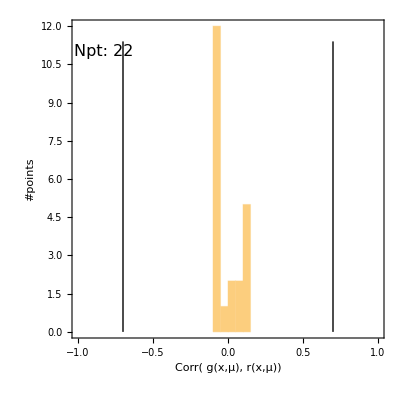
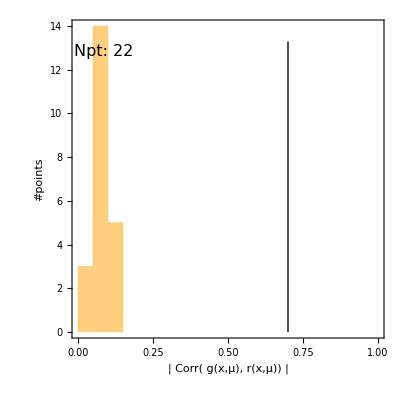
{{-Graphics-,Corr( g(x,μ), r(x,μ)) for dataset of CT14HERA2NNLO

 | 
Data Sets | 
None(225) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp6percentage[{corrdataclassfinal},readcorrconfigfile4[configDir,configfilename],6,0]
```

expts: {{240,241,281,266}}

can not find expt id = 240 in lisTable

can not find expt id = 241 in lisTable

can not find expt id = 281 in lisTable

can not find expt id = 266 in lisTable

making table of experiments included in plots

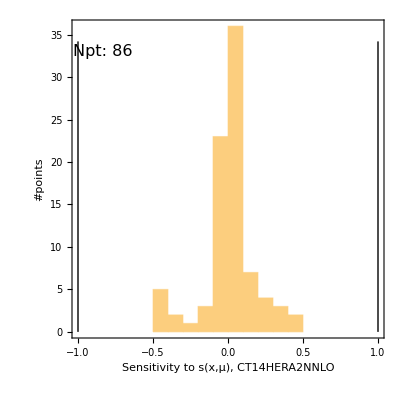
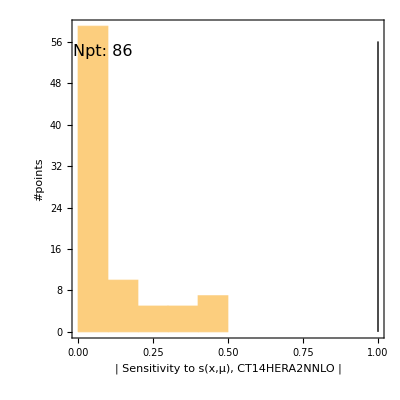
{{-Graphics-,Sensitivity to s(x,μ), CT14HERA2NNLO

 |  | 
Data Sets |  | 
None(240) | None(241) | None(281)
None(266) |  | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp6percentage[{dRcorrdataclassfinal},readcorrconfigfile4[configDir,configfilename],5,3]
```

```mathematica
residualdataclassfinal
```

```mathematica
{{<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-5|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-4|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-3|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-2|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-1|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->0|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->1|>|>,<|"label"->{"x","Q","residual"},"data"->{LF[0.17256153384559803,80.39,1.971732954545455],LF[0.1855112310794266,80.39,1.971732954545455],LF[0.19917645454180155,80.39,1.971732954545455],LF[0.21358308834796036,80.39,1.971732954545455],LF[0.22875747653402578,80.39,1.971732954545455],LF[0.2447264230570053,80.39,1.971732954545455],LF[0.261517191794792,80.39,1.971732954545455],LF[0.16030193864596357,80.39,-0.13771569433032135],LF[0.17256153384559803,80.39,-0.13771569433032135],LF[0.1855112310794266,80.39,-0.13771569433032135],LF[0.19917645454180155,80.39,-0.13771569433032135],LF[0.21358308834796036,80.39,-0.13771569433032135],LF[0.22875747653402578,80.39,-0.13771569433032135],LF[0.2447264230570053,80.39,-0.13771569433032135],LF[0.261517191794792,80.39,-0.13771569433032135],LF[0.2791575065461639,80.39,-0.13771569433032135],LF[0.29767555103078436,80.39,-0.13771569433032135],LF[0.3170999688892017,80.39,-0.13771569433032135],LF[0.33745986368284964,80.39,-0.13771569433032135],LF[0.17256153384559803,80.39,-0.433294117647059],LF[0.1855112310794266,80.39,-0.433294117647059],LF[0.19917645454180155,80.39,-0.433294117647059],LF[0.21358308834796036,80.39,-0.433294117647059],LF[0.22875747653402578,80.39,-0.433294117647059],LF[0.2447264230570053,80.39,-0.433294117647059],LF[0.261517191794792,80.39,-0.433294117647059],LF[0.2791575065461639,80.39,-0.433294117647059],LF[0.29767555103078436,80.39,-0.433294117647059],LF[0.3170999688892017,80.39,-0.433294117647059],LF[0.33745986368284964,80.39,-0.433294117647059],LF[0.35878479889404674,80.39,-0.433294117647059],LF[0.38110479792599694,80.39,-0.433294117647059],LF[0.17256153384559803,80.39,-0.8482809123649461],LF[0.1855112310794266,80.39,-0.8482809123649461],LF[0.19917645454180155,80.39,-0.8482809123649461],LF[0.21358308834796036,80.39,-0.8482809123649461],LF[0.22875747653402578,80.39,-0.8482809123649461],LF[0.2447264230570053,80.39,-0.8482809123649461],LF[0.261517191794792,80.39,-0.8482809123649461],LF[0.2791575065461639,80.39,-0.8482809123649461],LF[0.29767555103078436,80.39,-0.8482809123649461],LF[0.3170999688892017,80.39,-0.8482809123649461],LF[0.33745986368284964,80.39,-0.8482809123649461],LF[0.35878479889404674,80.39,-0.8482809123649461],LF[0.38110479792599694,80.39,-0.8482809123649461],LF[0.4044503441027893,80.39,-0.8482809123649461],LF[0.1855112310794266,80.39,0.0921636917718761],LF[0.19917645454180155,80.39,0.0921636917718761],LF[0.21358308834796036,80.39,0.0921636917718761],LF[0.22875747653402578,80.39,0.0921636917718761],LF[0.2447264230570053,80.39,0.0921636917718761],LF[0.261517191794792,80.39,0.0921636917718761],LF[0.2791575065461639,80.39,0.0921636917718761],LF[0.29767555103078436,80.39,0.0921636917718761],LF[0.3170999688892017,80.39,0.0921636917718761],LF[0.33745986368284964,80.39,0.0921636917718761],LF[0.35878479889404674,80.39,0.0921636917718761],LF[0.38110479792599694,80.39,0.0921636917718761],LF[0.4044503441027893,80.39,0.0921636917718761],LF[0.42885238066939807,80.39,0.0921636917718761]},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->2|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->3|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->4|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->5|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-5|>|>,<|"label"->{"x","Q","residual"},"data"->{LF[0.19917645454180155,80.39,1.971732954545455],LF[0.21358308834796036,80.39,1.971732954545455],LF[0.22875747653402578,80.39,1.971732954545455],LF[0.2447264230570053,80.39,1.971732954545455],LF[0.261517191794792,80.39,1.971732954545455],LF[0.1855112310794266,80.39,-0.13771569433032135],LF[0.19917645454180155,80.39,-0.13771569433032135],LF[0.21358308834796036,80.39,-0.13771569433032135],LF[0.22875747653402578,80.39,-0.13771569433032135],LF[0.2447264230570053,80.39,-0.13771569433032135],LF[0.261517191794792,80.39,-0.13771569433032135],LF[0.2791575065461639,80.39,-0.13771569433032135],LF[0.29767555103078436,80.39,-0.13771569433032135],LF[0.3170999688892017,80.39,-0.13771569433032135],LF[0.33745986368284964,80.39,-0.13771569433032135],LF[0.1855112310794266,80.39,-0.433294117647059],LF[0.19917645454180155,80.39,-0.433294117647059],LF[0.21358308834796036,80.39,-0.433294117647059],LF[0.22875747653402578,80.39,-0.433294117647059],LF[0.2447264230570053,80.39,-0.433294117647059],LF[0.261517191794792,80.39,-0.433294117647059],LF[0.2791575065461639,80.39,-0.433294117647059],LF[0.29767555103078436,80.39,-0.433294117647059],LF[0.3170999688892017,80.39,-0.433294117647059],LF[0.33745986368284964,80.39,-0.433294117647059],LF[0.35878479889404674,80.39,-0.433294117647059],LF[0.38110479792599694,80.39,-0.433294117647059],LF[0.1855112310794266,80.39,-0.8482809123649461],LF[0.19917645454180155,80.39,-0.8482809123649461],LF[0.21358308834796036,80.39,-0.8482809123649461],LF[0.22875747653402578,80.39,-0.8482809123649461],LF[0.2447264230570053,80.39,-0.8482809123649461],LF[0.261517191794792,80.39,-0.8482809123649461],LF[0.2791575065461639,80.39,-0.8482809123649461],LF[0.29767555103078436,80.39,-0.8482809123649461],LF[0.3170999688892017,80.39,-0.8482809123649461],LF[0.33745986368284964,80.39,-0.8482809123649461],LF[0.35878479889404674,80.39,-0.8482809123649461],LF[0.38110479792599694,80.39,-0.8482809123649461],LF[0.4044503441027893,80.39,-0.8482809123649461],LF[0.19917645454180155,80.39,0.0921636917718761],LF[0.21358308834796036,80.39,0.0921636917718761],LF[0.22875747653402578,80.39,0.0921636917718761],LF[0.2447264230570053,80.39,0.0921636917718761],LF[0.261517191794792,80.39,0.0921636917718761],LF[0.2791575065461639,80.39,0.0921636917718761],LF[0.29767555103078436,80.39,0.0921636917718761],LF[0.3170999688892017,80.39,0.0921636917718761],LF[0.33745986368284964,80.39,0.0921636917718761],LF[0.35878479889404674,80.39,0.0921636917718761],LF[0.38110479792599694,80.39,0.0921636917718761],LF[0.4044503441027893,80.39,0.0921636917718761],LF[0.42885238066939807,80.39,0.0921636917718761]},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-5|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-5|>|>}}
```

expts: {{225}}

can not find expt id = 225 in lisTable

making table of experiments included in plots

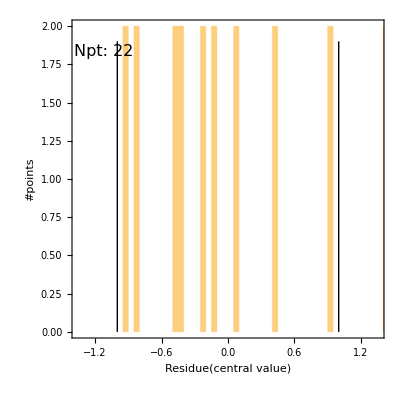
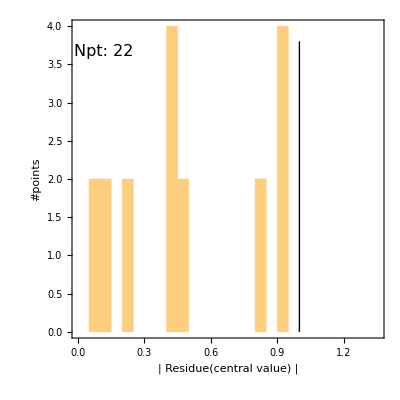
{{-Graphics-,Residue(central value) for dataset of CT14HERA2NNLO

 | 
Data Sets | 
None(225) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp6percentage[{residualdataclassfinal},readcorrconfigfile4[configDir,configfilename],3,1]
```

```mathematica
Show[p234[[1,1]] ]
```

-Graphics-

expts: {{225}}

can not find expt id = 225 in lisTable

making table of experiments included in plots

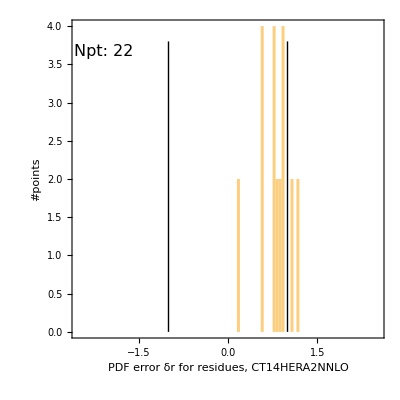
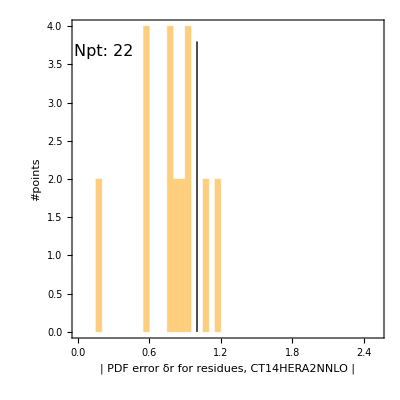
{{-Graphics-,PDF error δr for residues, CT14HERA2NNLO

 | 
Data Sets | 
None(225) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp6percentage[{dRdataclassfinal},readcorrconfigfile4[configDir,configfilename],4,1]
```

```mathematica
processdataplotsmultiexp6percentage[{expterrordataclassfinal},readcorrconfigfile4[configDir,configfilename],2,0]
```

ReadList::readn: Invalid real number found when reading from StringToStream[unset].

Read::readn: Invalid real number found when reading from StringToStream[unset].

Part::partw: Part 2 of {$Failed} does not exist.

Read::readn: Invalid real number found when reading from StringToStream[unset].

Part::partw: Part 2 of {$Failed} does not exist.

Read::readn: Invalid real number found when reading from StringToStream[unset].

General::stop: Further output of Read::readn will be suppressed during this calculation.

Part::partw: Part 2 of {$Failed} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReadList::readn: Invalid real number found when reading from StringToStream[unset].

General::stop: Further output of ReadList::readn will be suppressed during this calculation.

expts: {{101,125,126,127,225,227,261,268,240,241,281}}

error, highlight mode should be 0, 1, 2

$Aborted

```mathematica
Export["testreso.eps",processdataplotsmultiexp6percentage[{expterrordataclassfinal},readcorrconfigfile4[configDir,configfilename],2,0][[1,1]],ImageResolution->imgresol]
```

expts: {{240,241,281,266}}

can not find expt id = 240 in lisTable

can not find expt id = 241 in lisTable

can not find expt id = 281 in lisTable

can not find expt id = 266 in lisTable

making table of experiments included in plots

testreso.eps

```mathematica
imgresol=144
```

144

```mathematica
NotebookDirectory[]
```

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin/

```mathematica
Directory[]
```

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin

```mathematica
readcorrconfigfile4[configDir,configfilename]
```

{457,2017.0518.0238.-0500_ct14nn-new,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,542,544,249,250,565,566,567,568},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}, sigma_Higgs (pb),{0.012,0.012,0.012,0.014,0.012,0.012,0.012,0.032,0.012,0.012,0.012,0.015,0.012,0.012,0.052,0.012,0.012,0.022,0.012,0.0432,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.022,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012},{0.00001,1},{10.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,1,1,1,1,1},{0.5,0.75,0.,0.15,0.7,100.,0.7,100.,0.7,100.,0.7,1.,0.45,0.75},{50,86.55,85,100,85,100,85,100,50,85,50,85,50,85}}

```mathematica
readcorrconfigfile4[NotebookDirectory[],configfilename]
```

{457,2017.0518.0238.-0500_ct14nn-new,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,542,544,249,250,565,566,567,568},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}, sigma_Higgs (pb),{0.012,0.012,0.012,0.014,0.012,0.012,0.012,0.032,0.012,0.012,0.012,0.015,0.012,0.012,0.052,0.012,0.012,0.022,0.012,0.0432,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.022,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012},{0.00001,1},{10.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,1,1,1,1,1},{0.5,0.75,0.,0.15,0.7,100.,0.7,100.,0.7,100.,0.7,1.,0.45,0.75},{50,86.55,85,100,85,100,85,100,50,85,50,85,50,85}}

```mathematica
readcorrconfigfile4[Directory[]<>"/",configfilename]
```

{457,2017.0518.0238.-0500_ct14nn-new,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,542,544,249,250,565,566,567,568},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}, sigma_Higgs (pb),{0.012,0.012,0.012,0.014,0.012,0.012,0.012,0.032,0.012,0.012,0.012,0.015,0.012,0.012,0.052,0.012,0.012,0.022,0.012,0.0432,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.022,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012},{0.00001,1},{10.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,1,1,1,1,1},{0.5,0.75,0.,0.15,0.7,100.,0.7,100.,0.7,100.,0.7,1.,0.45,0.75},{50,86.55,85,100,85,100,85,100,50,85,50,85,50,85}}

```mathematica
FileNames[Directory[]]
FileNames[Directory[]<>"/"]
```

{/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin}

{/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin}

```mathematica
testnewindex=Import[CorrDataDir<>"expterror_"<>CorrDataFile,"ExpressionML"];
```

```mathematica
testnewindex[[1]]
```

<|label→{x,Q,expterror/exptcentral},data→{LF[0.101,2.328,0.123077],LF[0.167,2.994,0.113874],LF[0.326,4.182,0.123858],LF[0.057,2.295,0.100007],LF[0.101,3.055,0.0999652],LF[0.167,3.928,0.100094],LF[0.326,5.489,0.110615],LF[0.057,2.698,0.0965188],LF[0.101,3.592,0.106374],LF[0.167,4.618,0.118621],LF[0.326,6.452,0.130294],LF[0.057,2.457,0.104641],LF[0.101,3.271,0.0958001],LF[0.167,4.206,0.0989567],LF[0.326,5.877,0.107182],LF[0.057,3.225,0.098301],LF[0.101,4.293,0.100947],LF[0.167,5.52,0.102872],LF[0.326,7.712,0.118939],LF[0.021,2.301,0.0952787],LF[0.057,3.791,0.0903334],LF[0.101,5.046,0.100485],LF[0.167,6.488,0.11441],LF[0.326,9.065,0.132874],LF[0.057,2.925,0.108059],LF[0.101,3.894,0.102769],LF[0.167,5.007,0.102525],LF[0.326,6.996,0.115866],LF[0.021,2.33,0.117615],LF[0.057,3.839,0.115806],LF[0.101,5.11,0.112213],LF[0.167,6.571,0.116658],LF[0.326,9.181,0.131031],LF[0.021,2.739,0.119099],LF[0.057,4.512,0.103225],LF[0.101,6.007,0.102362],LF[0.167,7.724,0.130126],LF[0.326,10.79,0.161126]},exptinfo→<|exptid→124,exptname→NuTvNuChXN,feyndiagram→unset|>,PDFinfo→<|PDFname→CT14HERA2NNLO,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>,rawdata→{124,NuTvNuChXN,     Q          x         y          Exp      Th./Norm     TotErr     EXP/FIT  ERR/FIT    ChiSq  Shift    ShiftedData  UnCorErr  ReducedChi2  lob/lio,1.,38,R^2, r(k) =    0.000  -0.017,-2.27713,R^2, r(k) =    0.000  -0.017}|>

```mathematica
CorrDataDir
```

../quick_data/

```mathematica
Get["corr_proj_funcs.m"]
```

present directory: /home/botingw/Downloads/Sean_20171114/xqplotter_user_func_debug/xqplotter-master/bin

loading ../lib/pdfParsePDS2013.m

loading ../lib/dtareadbotingw2016.m

making table of experiments included in plots

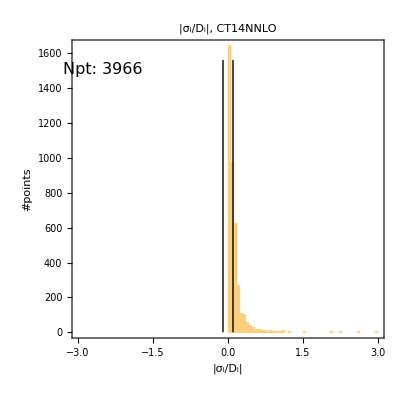
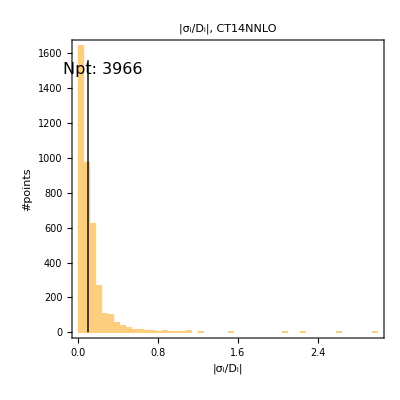
{{-Graphics-,|σ_i/D_i|, CT14NNLO

 |  | 
Data Sets |  | 
●BcdF2pCor(101) | ■BcdF2dCor(102) | ◆NmcRatCor(104)
▲cdhswf2(108) | ▼cdhswf3(109) | ○ccfrf2.mi(110)
□ccfrf3.md(111) | ◇NuTvNuChXN(124) | △NuTvNbChXN(125)
▽CcfrNuChXN(126) | ×CcfrNbChXN(127) | ⊖Hn1X0c(147)
★e605(201) | ●e866f(203) | ■e866ppxf(204)
◆cdfLasy(225) | ▲cdfLasy2(227) | ▼d02Masy1(234)
○ZyD02a(260) | □cdf2jtCor2(504) | ◇d02jtCor2(514)
△Hn+9900x0b(145) | ▽H1FL10(169) | ×ATL7_WZ(268)
⊖ATL7jtR6(535) | ★LHCb7_WZ1(240) | ●LHCb7Wasy1(241)
■d02Easy5(281) | ◆CMS7Masy2(266) | ▲CMS7jtR7v2(538)
▼LHCb7ZWrap(245) | ○LHCb8Zeer(246) | □ATL7ZW(248)
◇CMS7jtR7y6(542) | △ATL7jtR6u(544) | ▽CMS8Wxa(249)
×LHCb8WZ(250) | ⊖ATL8ttpt(565) | ★ATL8ttya(566)
●ATL8ttmtt(567) | ■ATL8ttytt(568) | 
 |  | },{-Graphics-,-Graphics-},{xQplotcorr2$4354591}}

```mathematica
processdataplotsmultiexp7percentage[{expterrordataclassfinal},readcorrconfigfile6[configDir,configfilename],2,flavour]
```

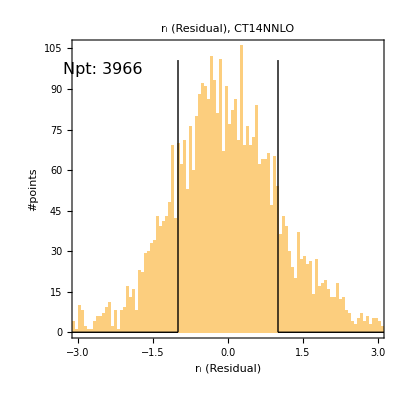
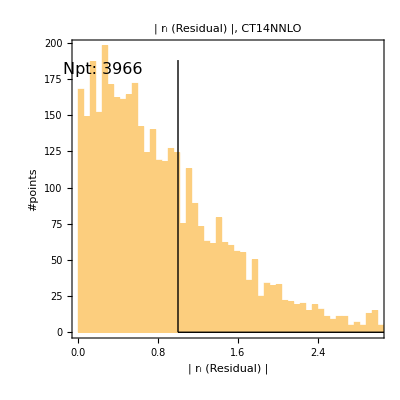
{{-Graphics-,r_i (Residual), CT14NNLO

 |  | 
Data Sets |  | 
●BcdF2pCor(101) | ■BcdF2dCor(102) | ◆NmcRatCor(104)
▲cdhswf2(108) | ▼cdhswf3(109) | ○ccfrf2.mi(110)
□ccfrf3.md(111) | ◇NuTvNuChXN(124) | △NuTvNbChXN(125)
▽CcfrNuChXN(126) | ×CcfrNbChXN(127) | ⊖Hn1X0c(147)
★e605(201) | ●e866f(203) | ■e866ppxf(204)
◆cdfLasy(225) | ▲cdfLasy2(227) | ▼d02Masy1(234)
○ZyD02a(260) | □cdf2jtCor2(504) | ◇d02jtCor2(514)
△Hn+9900x0b(145) | ▽H1FL10(169) | ×ATL7_WZ(268)
⊖ATL7jtR6(535) | ★LHCb7_WZ1(240) | ●LHCb7Wasy1(241)
■d02Easy5(281) | ◆CMS7Masy2(266) | ▲CMS7jtR7v2(538)
▼LHCb7ZWrap(245) | ○LHCb8Zeer(246) | □ATL7ZW(248)
◇CMS7jtR7y6(542) | △ATL7jtR6u(544) | ▽CMS8Wxa(249)
×LHCb8WZ(250) | ⊖ATL8ttpt(565) | ★ATL8ttya(566)
●ATL8ttmtt(567) | ■ATL8ttytt(568) | 
 |  | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp7percentage[{residualdataclassfinal},readcorrconfigfile6[configDir,configfilename],3,flavour]
```

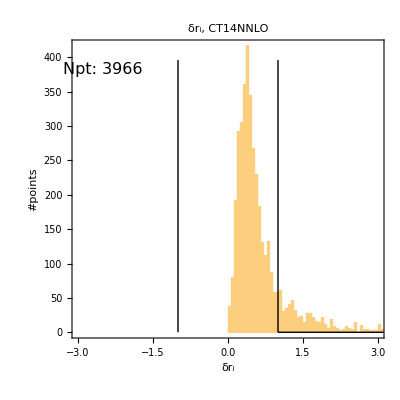
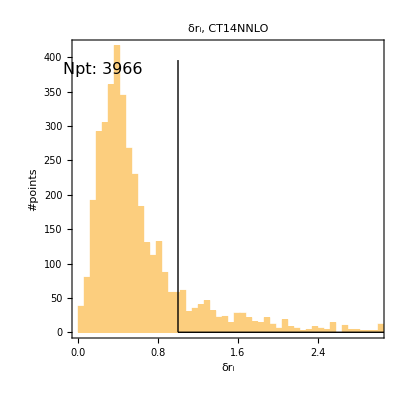
{{-Graphics-,δr_i, CT14NNLO

 |  | 
Data Sets |  | 
●BcdF2pCor(101) | ■BcdF2dCor(102) | ◆NmcRatCor(104)
▲cdhswf2(108) | ▼cdhswf3(109) | ○ccfrf2.mi(110)
□ccfrf3.md(111) | ◇NuTvNuChXN(124) | △NuTvNbChXN(125)
▽CcfrNuChXN(126) | ×CcfrNbChXN(127) | ⊖Hn1X0c(147)
★e605(201) | ●e866f(203) | ■e866ppxf(204)
◆cdfLasy(225) | ▲cdfLasy2(227) | ▼d02Masy1(234)
○ZyD02a(260) | □cdf2jtCor2(504) | ◇d02jtCor2(514)
△Hn+9900x0b(145) | ▽H1FL10(169) | ×ATL7_WZ(268)
⊖ATL7jtR6(535) | ★LHCb7_WZ1(240) | ●LHCb7Wasy1(241)
■d02Easy5(281) | ◆CMS7Masy2(266) | ▲CMS7jtR7v2(538)
▼LHCb7ZWrap(245) | ○LHCb8Zeer(246) | □ATL7ZW(248)
◇CMS7jtR7y6(542) | △ATL7jtR6u(544) | ▽CMS8Wxa(249)
×LHCb8WZ(250) | ⊖ATL8ttpt(565) | ★ATL8ttya(566)
●ATL8ttmtt(567) | ■ATL8ttytt(568) | 
 |  | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp7percentage[{dRdataclassfinal},readcorrconfigfile6[configDir,configfilename],4,flavour]
```

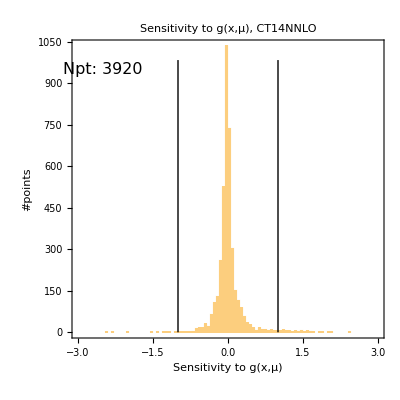
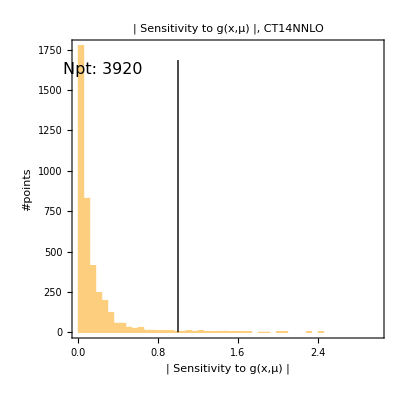
{{-Graphics-,Sensitivity to g(x,μ), CT14NNLO

 |  | 
Data Sets |  | 
●BcdF2pCor(101) | ■BcdF2dCor(102) | ◆NmcRatCor(104)
▲cdhswf2(108) | ▼cdhswf3(109) | ○ccfrf2.mi(110)
□ccfrf3.md(111) | ◇NuTvNuChXN(124) | △NuTvNbChXN(125)
▽CcfrNuChXN(126) | ×CcfrNbChXN(127) | ⊖Hn1X0c(147)
★e605(201) | ●e866f(203) | ■e866ppxf(204)
◆cdfLasy(225) | ▲cdfLasy2(227) | ▼d02Masy1(234)
○ZyD02a(260) | □cdf2jtCor2(504) | ◇d02jtCor2(514)
△Hn+9900x0b(145) | ▽H1FL10(169) | ×ATL7_WZ(268)
⊖ATL7jtR6(535) | ★LHCb7_WZ1(240) | ●LHCb7Wasy1(241)
■d02Easy5(281) | ◆CMS7Masy2(266) | ▲CMS7jtR7v2(538)
▼LHCb7ZWrap(245) | ○LHCb8Zeer(246) | □ATL7ZW(248)
◇CMS7jtR7y6(542) | △ATL7jtR6u(544) | ▽CMS8Wxa(249)
×LHCb8WZ(250) | ⊖ATL8ttpt(565) | ★ATL8ttya(566)
●ATL8ttmtt(567) | ■ATL8ttytt(568) | 
 |  | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp7percentage[{dRcorrdataclassfinal},readcorrconfigfile6[configDir,configfilename],5,0]
```

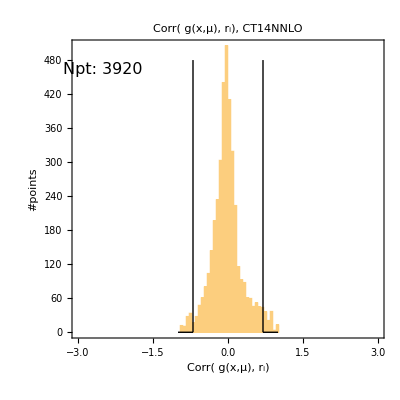
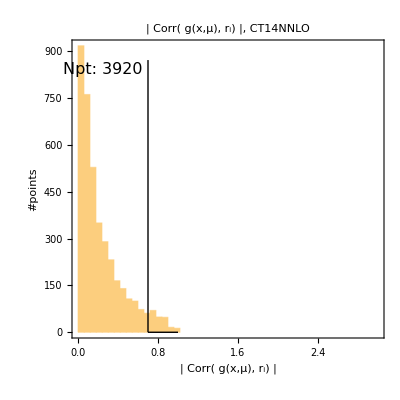
{{-Graphics-,| Corr( g(x,μ), r_i) |, CT14NNLO

 |  | 
Data Sets |  | 
●BcdF2pCor(101) | ■BcdF2dCor(102) | ◆NmcRatCor(104)
▲cdhswf2(108) | ▼cdhswf3(109) | ○ccfrf2.mi(110)
□ccfrf3.md(111) | ◇NuTvNuChXN(124) | △NuTvNbChXN(125)
▽CcfrNuChXN(126) | ×CcfrNbChXN(127) | ⊖Hn1X0c(147)
★e605(201) | ●e866f(203) | ■e866ppxf(204)
◆cdfLasy(225) | ▲cdfLasy2(227) | ▼d02Masy1(234)
○ZyD02a(260) | □cdf2jtCor2(504) | ◇d02jtCor2(514)
△Hn+9900x0b(145) | ▽H1FL10(169) | ×ATL7_WZ(268)
⊖ATL7jtR6(535) | ★LHCb7_WZ1(240) | ●LHCb7Wasy1(241)
■d02Easy5(281) | ◆CMS7Masy2(266) | ▲CMS7jtR7v2(538)
▼LHCb7ZWrap(245) | ○LHCb8Zeer(246) | □ATL7ZW(248)
◇CMS7jtR7y6(542) | △ATL7jtR6u(544) | ▽CMS8Wxa(249)
×LHCb8WZ(250) | ⊖ATL8ttpt(565) | ★ATL8ttya(566)
●ATL8ttmtt(567) | ■ATL8ttytt(568) | 
 |  | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp7percentage[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,0 ]
```

```mathematica
Get["corr_proj_funcs.m"]
ReadLisFile[datalistFile];
```

present directory: /home/botingw/Downloads/Sean_20171114/xqplotter_user_func_debug/xqplotter-master/bin

loading ../lib/pdfParsePDS2013.m

loading ../lib/dtareadbotingw2016.m

```mathematica
ReadUserFunction[Directory[]<>"/","user_define_func.txt"]
```

{ sigma_Higgs (pb),{0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012}}

```mathematica
(*{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,(*Hist1figureYrange*)dummy12,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=*)
readcorrconfigfile4[configDir,configfilename]
readcorrconfigfile5[configDir,configfilename][[-2]]
```

{70805,CT14NNLO,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}, ,{},{0.00001,1.},{1.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,2,2,2,2,1},{1.,5.,0.2,10,1.,5.,1.,5.,1.,5.,0.7,1.,1.,5.},{0.,0.,85,100,85,100,85,100,85,100,85,100,0.,0.}}

Read::readn: Invalid real number found when reading from StringToStream[unset].

Part::partw: Part 2 of {$Failed} does not exist.

Read::readn: Invalid real number found when reading from StringToStream[unset].

Part::partw: Part 2 of {$Failed} does not exist.

Read::readn: Invalid real number found when reading from StringToStream[unset].

General::stop: Further output of Read::readn will be suppressed during this calculation.

Part::partw: Part 2 of {$Failed} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReadList::readn: Invalid real number found when reading from StringToStream[unset].

{unset}

```mathematica
(*20171109: seperate user difine function/data IO and configure file*)
userfuncfilename="user_define_func.txt";
{UserArgName,UserArgValue}=ReadUserFunction["./",userfuncfilename]
```

{ sigma_Higgs (pb),{0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012}}

```mathematica
ReadUserFunctionV3["./",userfuncfilename]
```

```mathematica
fxQsamept2classfinal[[3,17]]
```

Part::partw: Part 3 of {{«1»},{«1»}} does not exist.

1⟦3,17⟧
 |  |  |  |

```mathematica
exptidDir
```

StringDrop[,-1]<>/

```mathematica
exptid
```

101

```mathematica
fxQDatabaseExptlist
```

{101,102,104,106,108,109,110,111,124,125,126,127,145,147,159,169,201,203,204,225,227,234,240,241,260,261,266,267,268,281,504,514,535,538}

```mathematica
((fxQDatabaselist[[1,iu+6,3]]/.LF->List)-(fxQDatabaselist[[1,iubar+6,3]]/.LF->List))/((fxQDatabaselist[[1,iu+6,3]]/.LF->List)+(fxQDatabaselist[[1,iubar+6,3]]/.LF->List))
fxQsamept2classfinal[[2,-1]][["data"]][[1]]
```

{0.,0.,0.73252,0.739896,0.737092,0.737801,0.732453,0.733104,0.733845,0.740846,0.727685,0.726688,0.737235,0.729246,0.739421,0.730101,0.733949,0.731093,0.738179,0.71995,0.746273,0.730365,0.735003,0.732212,0.732774,0.723387,0.742542,0.736026,0.729819,0.735491,0.727436,0.737356,0.729457,0.725302,0.743687,0.730909,0.733941,0.73306,0.732583,0.728924,0.736762,0.727223,0.740451,0.731621,0.732744,0.730706,0.733423,0.743015,0.727697,0.715237,0.748441,0.738931,0.724507,0.733199,0.729687,0.732723,0.735427,0.728392,0.72429}

LF[0.0457788,80.38,0.73252,0.739896,0.737092,0.737801,0.732453,0.733104,0.733845,0.740846,0.727685,0.726688,0.737235,0.729246,0.739421,0.730101,0.733949,0.731093,0.738179,0.71995,0.746273,0.730365,0.735003,0.732212,0.732774,0.723387,0.742542,0.736026,0.729819,0.735491,0.727436,0.737356,0.729457,0.725302,0.743687,0.730909,0.733941,0.73306,0.732583,0.728924,0.736762,0.727223,0.740451,0.731621,0.732744,0.730706,0.733423,0.743015,0.727697,0.715237,0.748441,0.738931,0.724507,0.733199,0.729687,0.732723,0.735427,0.728392,0.72429]

```mathematica
((fxQDatabaselist[[10,iu+6,1]]/.LF->List)-(fxQDatabaselist[[10,iubar+6,1]]/.LF->List))/((fxQDatabaselist[[10,iu+6,1]]/.LF->List)+(fxQDatabaselist[[10,iubar+6,1]]/.LF->List))
fxQsamept2classfinal[[1,-2]][["data"]][[1]]
fxQsamept2classfinal[[1,1]][["exptinfo","exptid"]]
```

{0.,0.,0.767313,0.774295,0.771563,0.770956,0.767449,0.768422,0.767628,0.774979,0.763023,0.762259,0.77139,0.764176,0.773848,0.764799,0.769074,0.765233,0.774406,0.755397,0.780305,0.765556,0.7694,0.767543,0.767253,0.758681,0.776735,0.772911,0.762984,0.769194,0.76411,0.772426,0.76408,0.760625,0.777586,0.765114,0.769266,0.767729,0.767396,0.76444,0.77077,0.762994,0.774419,0.765861,0.768338,0.766176,0.767648,0.776773,0.762919,0.750987,0.782312,0.773,0.75975,0.767026,0.765635,0.766226,0.768834,0.764391,0.757922}

LF[0.114,2.411,0.767313,0.774295,0.771563,0.770956,0.767449,0.768422,0.767628,0.774979,0.763023,0.762259,0.77139,0.764176,0.773848,0.764799,0.769074,0.765233,0.774406,0.755397,0.780305,0.765556,0.7694,0.767543,0.767253,0.758681,0.776735,0.772911,0.762984,0.769194,0.76411,0.772426,0.76408,0.760625,0.777586,0.765114,0.769266,0.767729,0.767396,0.76444,0.77077,0.762994,0.774419,0.765861,0.768338,0.766176,0.767648,0.776773,0.762919,0.750987,0.782312,0.773,0.75975,0.767026,0.765635,0.766226,0.768834,0.764391,0.757922]

125

dim of data: {41}

exptlist {101,102,104,108,109,110,111,124,125,126,127,147,201,203,204,225,227,234,260,504,514,145,169,268,535,240,241,281,266,538,245,246,248,542,544,249,250,565,566,567,568}

dim of data: {42}

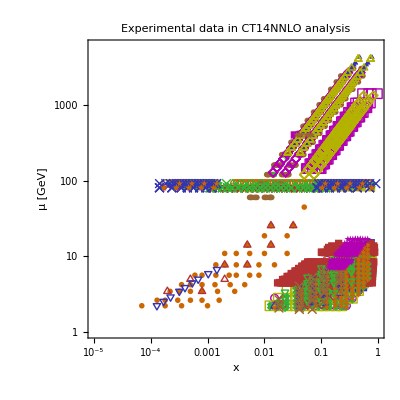

```mathematica
processdataplotsmultiexp7percentage[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],1,0 ]
```

```mathematica
Get["corr_proj_funcs.m"]
```

present directory: /home/botingw/Downloads/Sean_20171114/xqplotter_user_func_debug/xqplotter-master/bin

loading ../lib/pdfParsePDS2013.m

loading ../lib/dtareadbotingw2016.m

```mathematica
ReadLisFile[datalistFile];
```

```mathematica
lisTable
```

lisTable

```mathematica
readcorrconfigfile6[configDir,configfilename]//TableForm
```

aaaa |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
CT14HERA2NNLO |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 2 | 3 | 4 | 5 | 6 | 7 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 1 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
701 | 702 | 703 | 159 | 101 | 102 | 103 | 104 | 106 | 108 | 109 | 110 | 111 | 124 | 125 | 126 | 127 | 147 | 201 | 203 | 204 | 225 | 227 | 231 | 234 | 260 | 261 | 504 | 514 | 145 | 169 | 267 | 268 | 535 | 240 | 241 | 281 | 265 | 266 | 538 | 245 | 246 | 247 | 248 | 542 | 544 | 249 | 250 | 565 | 566 | 567 | 568 | 545 | 160
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
bb | cb | sb | db | ub | g | u | d | s | c | b | user |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
auto | auto |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 6000 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1. | 1. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
100 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
50 | 70 | 85 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
tiny |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 2 | 3 | 4 | 5 | 6 | 7 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -5. | -0.25
0.25 | 5. | -1. | -0.7
0.7 | 1. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
readcorrconfigfile6[configDir,configfilename]//TableForm
```

aaaa |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
CT14HERA2NNLO |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 2 | 3 | 4 | 5 | 6 | 7 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 1 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
701 | 702 | 703 | 159 | 101 | 102 | 103 | 104 | 106 | 108 | 109 | 110 | 111 | 124 | 125 | 126 | 127 | 147 | 201 | 203 | 204 | 225 | 227 | 231 | 234 | 260 | 261 | 504 | 514 | 145 | 169 | 267 | 268 | 535 | 240 | 241 | 281 | 265 | 266 | 538 | 245 | 246 | 247 | 248 | 542 | 544 | 249 | 250 | 565 | 566 | 567 | 568 | 545 | 160
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
bb | cb | sb | db | ub | g | u | d | s | c | b | user |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
auto | auto |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 6000 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1. | 1. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
100 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
tiny |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 2 | 3 | 4 | 5 | 6 | 7 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -5. | -0.25
0.25 | 5. | -1. | -0.7
0.7 | 1. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
readcorrconfigfile6[configDir,configfilename]//TableForm
```

CT14NNLOallIDs |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 CT14NNLO all Expts to Higgs fake data |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
CT14NNLO |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 2 | 3 | 4 | 5 | 6 | 7 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 1 | 1 | 1 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
701 | 702 | 703 | 159 | 101 | 102 | 103 | 104 | 106 | 108 | 109 | 110 | 111 | 124 | 125 | 126 | 127 | 147 | 201 | 203 | 204 | 225 | 227 | 231 | 234 | 260 | 261 | 504 | 514 | 145 | 169 | 267 | 268 | 535 | 240 | 241 | 281 | 265 | 266 | 538 | 245 | 246 | 247 | 248 | 542 | 544 | 249 | 250 | 565 | 566 | 567 | 568 | 545 | 160
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
bb | cb | sb | db | ub | g | u | d | s | c | b | user |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
auto | auto |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 6000 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-3. | 3. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
100 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
tiny |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 2 | 3 | 4 | 5 | 6 | 7 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 1 | 1 | 1 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | -100 | -1
1 | 100 | 1 | 100 | -5. | -0.25
0.25 | 5. | -1. | -0.7
0.7 | 1. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

### test run the info of data

```mathematica
(*20171126*)
(*
when call processdataplotsmultiexp7percentage,
if plot type = 1, call this function to draw data sets on (x,Q) plane
*)
PlotDataTypeOneTest[corrfxQdtaobsclassin_,pdfcorrin_,exptlistin_,xyrangein_,classifymodein_,configargumentsin_]:=
Module[{corrfxQdtaobsclass=corrfxQdtaobsclassin,pdfcorr=pdfcorrin,exptlist=exptlistin,classifymode=classifymodein,configarguments=configargumentsin,
plottype,expttype,
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
lgdpos,xyrangeplot1,plotrange,
myplotsetting,imgsize,title,xtitle,ytitle,lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,myplotstyle,myMarker,
plot1,
xyrange=xyrangein,
groupnames,groupExptIDs,
ColorPaletterange,JobDescription,
Ncolor},

(*read arguments in config file*)
(*==============================*)
{Jobid,JobDescription(*20171128*),PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,ColorPaletterange(*20171128*),Hist1figureNbin,(*Hist1figureXrange,Hist1figureYrange,*)
(*ColorSeperator,*)
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=configarguments;
(*20171128: set hist xrange determined by the range of color palette, yrange alway auto*)
Hist1figureXrange=ColorPaletterange;
Hist1figureYrange={"auto","auto"};
(*=============================================================================================================================*)
(*plot type 1: generate plots============================================================================================================*)
(*=============================================================================================================================*)
{myplotsetting,imgsize,title,xtitle,ytitle,lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,myplotstyle,myMarker};

(*plot1*)

expttype="multi";
(*20170515 groups of data, legend is exptids in all groups, using Flatten, PDFname should be took cared*)
myplotsetting=setplotsetting[Flatten[corrfxQdtaobsclassin,1],exptlist//Flatten,expttype,1,"test","test"];
imgsize=myplotsetting[["imgsize"]];
title=myplotsetting[["title"]];
xtitle=myplotsetting[["xtitle"]];
ytitle=myplotsetting[["ytitle"]];
lgdlabel=myplotsetting[["lgdlabel"]];
xrange=myplotsetting[["xrange"]];
yrange=myplotsetting[["yrange"]];
epilog=myplotsetting[["epilog"]];
titlesize=myplotsetting[["titlesize"]];
xtitlesize=myplotsetting[["xtitlesize"]];
ytitlesize=myplotsetting[["ytitlesize"]];
lgdlabelsize=myplotsetting[["lgdlabelsize"]];
ticklablesize=myplotsetting[["ticklablesize"]];

myplotstyle=myplotsetting[["plotstyle"]];
myMarker=myplotsetting[["marker"]];

title="Experimental data in "<>PDFname<>" analysis";
lgdpos={0.25,0.725};
(*xyrangeplot1=plotrange;*)(*20170307 change it's name, avoid duplicate*)
(*20170515: consider expts in all groups*)
(*20170515: consider expts of all groups, so use Flatten[data,1] *)

(*
Print["dim of p1: ",Dimensions[pdfcorr] ];
Print["dim of p1: ",Dimensions[Flatten[pdfcorr,1] ]];
Print["data of p1: ",Flatten[pdfcorr,1][[1]] ];
Print["data of p1: ",Flatten[pdfcorr,1][[2]] ];
Print["data of p1: ",Flatten[pdfcorr,1][[3]] ];
Print["data of p1: ",Flatten[pdfcorr,1][[4]] ];
PDFloglogplot[Flatten[pdfcorr,1]/.LF1->List,myMarker,myplotstyle,title,xtitle,ytitle,xyrangeplot1,lgdlabel,lgdpos,imgsize];
Abort[];
*)
(*20171126: use marker list*)
myMarker=PlotMarkerList[];
myMarker[[2]]=0.0075*myMarker[[2]];
myMarker=Transpose[myMarker,{2,1}];
(*20171130 set color for points, everytime the shape return to the first shape, change to another color*)
Ncolor={RGBColor[0.7, 0.2, 0.2], RGBColor[0.2, 0.2, 0.7], RGBColor[0.2, 0.7, 0.2], RGBColor[0.6, 0.4, 0.2], RGBColor[0.8, 0.4, 0.], 
 RGBColor[0.7, 0., 0.7], (*RGBColor[0.6, 0.6, 0.6],*) RGBColor[0.7, 0.7, 0.]};

(*myplotstyle=Table[Table[Ncolor[[icolor]],{imarker,Length[myMarker]}],{icolor,Length[Ncolor]}]//Flatten;*)
myplotstyle=Flatten[(Ncolor&/@Range[Length[myMarker] ])];(*20171201: color also rotation for every Expt ID*)
(*when all shapes are used out, return to the first one*)
myMarker=Flatten[(myMarker&/@Range[Length[Ncolor] ]),1];

Print["dim of data: ",Dimensions[pdfcorr] ];
Print["exptlist ",exptlist];
(*always don't show only one shape for all expt ID points*)
If[classifymode=="all",classifymode="single"];
{groupnames,groupExptIDs,(*groupdata*)pdfcorr}=ClassifyPlottedData[pdfcorr,exptlist,classifymode];
pdfcorr=Table[Flatten[pdfcorr[[igroup]],1],{igroup,Length[pdfcorr]}];
lgdlabel=
Switch[classifymode,"single",lgdlabel,"all",groupnames];

Print["dim of data: ",Dimensions[pdfcorr] ];

plot1=PDFloglogplot[(*Flatten[pdfcorr,1]*)pdfcorr,myMarker,myplotstyle,title,xtitle,ytitle,xyrange(*plot1*),lgdlabel,lgdpos,imgsize];

(*return*)

{plot1}

(*
{myMarker,myplotstyle,title,xtitle,ytitle,xyrange,lgdlabel,lgdpos,imgsize}
*)
]
```

```mathematica
(*modify of 3: when plottype = 5, 6, extract data of that flavour*)
(*modify of 4: don't set local variable of corrfxQdtaobsclassin, avoiding time to copy large data to local variable, for mode 5,6 only deal with 
corresponding flavour data (by flavourin)*)

(*20170515 this version corrfxQdtaobsclassin structure is {class1, class2,...}
it is for plotting different group of data in different point shapes
*)

(*20171108: reorganize the function*)
(*use the new highlight range convention*)
getcorrinfo[corrfxQdtaobsclassin_,configargumentsin_,plottypein_,flavourin_]:=
Module[{(*corrfxQdtaobsclass=corrfxQdtaobsclassin,*)configarguments=configargumentsin,
plottype=plottypein,(*flavour=flavourin,*)flavour,
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,pdfnamelable,PDFsetlabel,pdffile,corrfile,pdfcorr,pdfcorrdr,deltaR,textsize,Npttext,maxtext,maxmarker,mintext,minmarker,cuttext,epilogxQ,epilogxQcorr,corrtitle1,corrdrtitle1,deltaRtitle1,title2,obsname,title3,title4,title,xtitle,ytitle,xhisttitle,xhistabstitle,yhisttitle,plotrange,stretchx,stretchy,legendlabel,barseperator,binset,lineelement,plotrangex,SM,SM1,SM2,SM3,xQplotcorr ,histplotcorr1,histplotcorr2,xQplotcorrdr,histplotcorrdr1,histplotcorrdr2,xQplotdr,histplotdr2,myexpids,fmax,fmax2,
imgsize,(*title,xtitle,ytitle,*)lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
myplotstyle,myMarker,
lgdpos,xyrangeplot1,
myplotsetting,plot1data,plot1,processesplot1order,
dummy1,dummy2,percentagetext,hist1plotrangex,histautoxrange,hist2autoxrange,hist2plotrangex,xQautorange,unhighlightsize,highlightrange,highlighttext,
exptlist,expttype,
rows,exptnames,exptnamestable,
lineelement2,maxdata,
barlegend,
histtitle,histabstitle,yhistabstitle,HistAutoMode,userdifinefuncfilename,
hist1plotrangey,hist2plotrangey,BinWidth,hist1plotrange,hist2plotrange,highlightlines,
xmintmp,xmaxtmp,ymintmp,hist1epilogtext,hist2epilogtext,hist1standardlines,hist2standardlines,LineWidth,HistAutoFixXrangeBool,
datemode,HistDataList,HistAbsDataList,DataMax,DataMin,AbsDataMax,AbsDataMin,DataMean,AbsDataMean,DataMedian,AbsDataMedian,DataSD,AbsDataSD,
ColorPaletteMode,PaletteMax,PaletteMin,
groupnames,groupExptIDs,classifymode,
ColorPaletterange,JobDescription,
shapeslist,abstitle,absPaletteMax,absbarseperator,absbarlegend,xQplotcorr2,exptnamestitle,
safewidth,datatype,output},

(*read arguments in config file*)
(*==============================*)
{Jobid,JobDescription(*20171128*),PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,ColorPaletterange(*20171128*),Hist1figureNbin,(*Hist1figureXrange,Hist1figureYrange,*)
(*ColorSeperator,*)
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=configarguments;
(*20171128: set hist xrange determined by the range of color palette, yrange alway auto*)
Hist1figureXrange=ColorPaletterange;
Hist1figureYrange={"auto","auto"};
(*should be three numbers, representing percentage, and from small to large, ex: 30, 50, 70*)
ColorSeperator={50,70,85};

(*20171109: seperate user difine function/data IO and configure file*)(*20171116: ->ReadUserFunctionV2, which read Expression from the file*)
(*20171119 new user function format: {{user name 1, user function 1}, {user name 2, user function 2}...}*)
userdifinefuncfilename="user_func.txt";
(*
{UserArgName,UserArgValue}=ReadUserFunctionV2["./",userdifinefuncfilename];
*)
(*20171127*)
If[
CorrelationArgFlag[[-1]]==1,
UserArgName=ReadUserFunctionV3["./",userdifinefuncfilename];
UserArgName=#[[1]]&/@UserArgName;
"dummy"
];

(*20171109: shorten the tiles of figures*)
If[PDFname=="2017.1008.0954.-0500_CT14HERA2-jet.ev",PDFname="CT14HERA2-jet.ev"];
(*=============================================================================================================================*)
(*Data organization============================================================================================================*)
(*=============================================================================================================================*)
(*read exptlist*)
exptlist={};
If[plottype==1  || plottype==5  || plottype==6,exptlist=Table[#[[iexpt,6]][["exptinfo","exptid"]],{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin ];
If[plottype==2  || plottype==3  || plottype==4,
exptlist=Table[#[[iexpt]][["exptinfo","exptid"]],{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin ];
(*test*)(*Print["expts: ",exptlist];*)

(*20171126 classify mode for data -> different shape for each group*)
classifymode=ClassifyMode;

(*********************************)
(*prepare for data input to processdataplotsmultiexp*)
(*********************************)
(*transf format from LF to LF1, since plot functions use LF1*)

(*if dr*corr or corr, data is [[iexpt,flavour]]*)
(*20170515: pdfcorr = {group1data, group2data, ...}, groupNdata = {LF1[x,Q,obs],...}*)
If[
plottype==5  || plottype==6,
fmax=Length[corrfxQdtaobsclassin[[1,1]] ];

(*data format == {LF[x,Q,obs],...,...}, to LF1*)
pdfcorr=Table[#[[iexpt,flavourin+6]][["data"]]/.LF->LF1,{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin;
Print[Length[exptlist[[1]] ],"  ",Length[pdfcorr[[1]] ] ];(*test length data*)

(*20171126: classify exptid by defined groups with classifymode*)
{groupnames,groupExptIDs,(*groupdata*)pdfcorr}=ClassifyPlottedData[pdfcorr[[1]],exptlist[[1]],classifymode];
Print[Length[exptlist[[1]] ],"  ",Length[pdfcorr] ];(*test length data*)
(*pdfcorr=Table[Flatten[pdfcorr[[igroup]],1],{igroup,Length[pdfcorr]}];*)

(*merge all experimental data into one, for all flavours*)
(*ex: corrdataforplot[[iexpt,flavour,Npt]] -> orrdataforplot[[flavour,Npt]]*)
(*{pdfcorr ,dummy1,dummy2}=mergeplotdata[{pdfcorr ,pdfcorr,pdfcorr}];*)
pdfcorr=Flatten[#,1]&/@pdfcorr;
Print[Length[exptlist[[1]] ],"  ",Length[pdfcorr]," ",Length[groupnames]," ",Length[groupExptIDs] ];(*test length data*)

(* deletezerovalue: delete data with 0 value (0 value usually from mb, mc cut)*)
(*{pdfcorr ,dummy1,dummy2}=deletezerovalue[{pdfcorr ,pdfcorr,pdfcorr}];*)
pdfcorr=Table[Select[pdfcorr[[igroup]],#[[3]]!=0&],{igroup,1,Length[pdfcorr]}];
"dummy"
];

(*data of [[iexpt]]*)
If[
plottype==2 || plottype==3 || plottype==4,
(*take data, and format from LF to LF1 (LF1 is format to input to plot functions)*)
pdfcorr=Table[#[[iexpt]][["data"]]/.LF->LF1,{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin;
(*20171108 expt error ratio values should be absolute value*)
If[plottype==2,pdfcorr=pdfcorr/.LF1[a__]:>LF1[{a}[[1]],{a}[[2]],Abs[{a}[[3]] ] ] ];

(*20171126: classify exptid by defined groups with classifymode*)
{groupnames,groupExptIDs,(*groupdata*)pdfcorr}=ClassifyPlottedData[pdfcorr[[1]],exptlist[[1]],classifymode];

(*merge all data into one*)
pdfcorr=Flatten[#,1]&/@pdfcorr;
"dummy"
];
(*test print*)(*Print[pdfcorr ];Print[pdfcorr/.LF1->LF2 ];Print[pdfcorr/.LF1[a__]:>{a}[[2]] ];*)

If[
plottype==1,
fmax=Length[corrfxQdtaobsclassin[[1,1]] ];

(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
pdfcorr=Table[Datamethods[["take"]][#[[iexpt,flavourin+6]],2][["data"]]/.LF->LF1,{iexpt,1,Length[#]}]&/@corrfxQdtaobsclassin;
];

(*20171202: if the "other" type has no expt ID, delete it*)
If[Length[groupExptIDs[[-1]] ]==0,{groupnames,groupExptIDs,(*groupdata*)pdfcorr}=Drop[#,-1]&/@{groupnames,groupExptIDs,(*groupdata*)pdfcorr}];

Print[Length[exptlist[[1]] ],"  ",Length[pdfcorr] ];(*test length data*)
(*=============================================================================================================================*)
(*Statistical quantities of data============================================================================================================*)
(*=============================================================================================================================*)
(*20171115*)
{HistDataList,HistAbsDataList,DataMax,DataMin,AbsDataMax,AbsDataMin,DataMean,AbsDataMean,DataMedian,AbsDataMedian,DataSD,AbsDataSD};
If[
plottype==2 || plottype==3 || plottype==4 || plottype==5 || plottype==6,
HistDataList=Flatten[pdfcorr]/.LF1[a__]:>{a}[[3]];
HistAbsDataList=Flatten[pdfcorr]/.LF1[a__]:>Abs[{a}[[3]] ];
DataMax=Max[HistDataList];
DataMin=Min[HistDataList];
AbsDataMax=Max[HistAbsDataList];
AbsDataMin=Min[HistAbsDataList];
DataMean=Mean[HistDataList];
AbsDataMean=Mean[HistAbsDataList];
DataMedian=Median[HistDataList];
AbsDataMedian=Median[HistAbsDataList];
DataSD=StandardDeviation[HistDataList];
AbsDataSD=StandardDeviation[HistAbsDataList];
"dummy"
];
(*=============================================================================================================================*)
(*Highlight range setting============================================================================================================*)
(*=============================================================================================================================*)

(*for no highlight mode, choose size of data point in plot by Size
for highlight mode, set size of unhighlighted data as Size, size of highlighted data is larger than Size*)
(*==============================*)

highlightrange=
Switch[
HighlightMode[[plottype]],
0,{{0.0,0.0}},
(*20171109: use new highlight range convention*)
1,(*{HighlightMode1[[2*plottype-1]],HighlightMode1[[2*plottype]]}*)HighlightMode1[[plottype]],
(*20171111: percentage highlight: don't take absolute values for data*)
(*20171201: percentage highlight depends on drawing data, if draw |data|, use percentage of |data|*)
2,Switch[
FigureFlag[[plottype]],
-1,
GetDataPercentage[(*Flatten[pdfcorr]/.LF1[a__]:>{a}[[3]]*)HistDataList,(*{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}*)#]&/@HighlightMode2[[plottype]],
1,
GetDataPercentage[(*Flatten[pdfcorr]/.LF1[a__]:>{a}[[3]]*)HistAbsDataList,(*{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}*)#]&/@HighlightMode2[[plottype]],
_,
Print["error, figure flag should be 1 or -1"];Abort[]
]
(*
Which[
plottype==5  || plottype==6,
GetDataPercentage[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
 plottype==2 || plottype==3 || plottype==4,
GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
True,Print["presently plottype is only 2~6 "];Abort[]
]*),
_,Print["error, highlight mode should be 0, 1, 2"];Abort[]
];
(*20171201 for percentage highlight the largest one should have a range of width to include the highest percentage point*)
If[
HighlightMode[[plottype]]==2,
Table[
safewidth=0.000001*(highlightrange[[iHL,2]]-highlightrange[[iHL,1]]);
highlightrange[[iHL,1]]=highlightrange[[iHL,1]]-safewidth;
highlightrange[[iHL,2]]=highlightrange[[iHL,2]]+safewidth,
{iHL,Length[highlightrange]}
];
"dummy" 
];
(*******************************************************************************)
pdfnamelable={"bbar(x,Q)","cbar(x,Q)","sbar(x,Q)","dbar(x,Q)","ubar(x,Q)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)"};
(*20171127: only add new string when user function is mode on*)
If[
CorrelationArgFlag[[-1]]==1,
pdfnamelable=pdfnamelable~Join~{Sequence@@UserArgName(*20171119 change to multi-user functions*)};
"dummy"
];
(*20171202 select highlighted points*)
(*20171202 if plot type flag = -1, show statistics of |data|*)
datatype={"xQ plot","|sigma/D|","r (residuals)","deltaR (uncertainties of residuals)","Sens(r, f(x,Q))","Corr(r, f(x,Q))"};
datatype=datatype[[plottype]];

If[
FigureFlag[[plottype]]==1,
pdfcorr=pdfcorr/.LF1[a__]:>LF1[{a}[[1]],{a}[[2]],Abs[{a}[[3]] ] ];
If[plottype==3 || plottype==5 || plottype==6,datatype="|"<>datatype<>"|"];
"dummy"
];

Table[
pdfcorr[[iexpt]]=
Select[
pdfcorr[[iexpt]],
Length[Intersection[Table[If[(#[[3]]>=highlightrange[[i,1]] && #[[3]]<highlightrange[[i,2]]),True,False],{i,Length[highlightrange]}],{True}] ]>0&
],
{iexpt,Length[pdfcorr]}
];

Print[Length[exptlist[[1]] ]," ",Length[pdfcorr] ];
(*output*)

(*if |data|, define get statistical quantities of |data|*)
If[FigureFlag[[plottype]]==1,DataMax=AbsDataMax;DataMin=AbsDataMin;DataMean=AbsDataMean;DataMedian=AbsDataMedian;DataSD=AbsDataSD];
(*output {{labels},{values or descriptions}}*)

If[
(plottype==5 || plottype==6),
output=
{
{"datatype","flavour","Expts","DataMax","DataMin","DataMean","DataMedian","DataSD","highlightrange","highlighted data"},
{datatype,pdfnamelable[[flavourin+6]],{#[[1]],ExptIDtoName[#[[1]] ]}&/@groupExptIDs,DataMax,DataMin,DataMean,DataMedian,DataSD,highlightrange,Transpose[{{#[[1]],ExptIDtoName[#[[1]] ]}&/@groupExptIDs,pdfcorr},{2,1}]}
}
];
If[
(plottype==2 || plottype==3 || plottype==4),
output=
{
{"datatype",(*"flavour",*)"Expts","DataMax","DataMin","DataMean","DataMedian","DataSD","highlightrange","highlighted data"},
{datatype,(*pdfnamelable[[flavourin+6]],*){#[[1]],ExptIDtoName[#[[1]] ]}&/@groupExptIDs,DataMax,DataMin,DataMean,DataMedian,DataSD,highlightrange,Transpose[{{#[[1]],ExptIDtoName[#[[1]] ]}&/@groupExptIDs,pdfcorr},{2,1}]}
}

];

output
(*
groupExptIDs
*)
(*
{exptlist,highlightrange,pdfcorr}
*)
]
```

```mathematica
getcorrinfo[{dRdataclassfinal},readcorrconfigfile6[configDir,configfilename],4,flavour];
getcorrinfo[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,0 ];
```

41  41

41 41

41  41

41  42

41  42 42 42

41  41

41 41

```mathematica
Select[getcorrinfo[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,0 ][[3,25]],(#[[3]]>0.7 || #[[3]]<-0.7)&]
```

{LF1[0.009958,60.,-0.920452],LF1[0.01991,120.,0.752923],LF1[0.06971,420.,0.70962],LF1[0.0863,520.,0.818724],LF1[0.011,60.,0.861669],LF1[0.02093,120.,-0.770349],LF1[0.07328,420.,0.770767],LF1[0.1395,800.,0.745724],LF1[0.3584,1600.,-0.711321],LF1[0.448,2000.,-0.793913],LF1[0.5377,2400.,-0.776612],LF1[0.007377,60.,-0.906253],LF1[0.01475,120.,0.847083],LF1[0.05164,420.,0.724224],LF1[0.09836,800.,0.795971],LF1[0.006675,60.,0.824985],LF1[0.04672,420.,0.710665],LF1[0.01403,120.,-0.71674],LF1[0.02573,220.,0.773972],LF1[0.04912,420.,0.789323],LF1[0.3508,3000.,-0.746913],LF1[0.1457,1600.,-0.77037],LF1[0.1821,2000.,-0.758868],LF1[0.2186,2400.,-0.769159],LF1[0.00906,90.,0.702211]}

```mathematica
Export["../plots/"<>jobpath<>"test_data_info.txt",(getcorrinfo[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,0 ]//TableForm)//OutputForm]
```

41  41

41  42

41  41 41 41

41  41

41 41

../plots/Jobs/CT14NNLOallIDs/test_data_info.txt

```mathematica
DirectoryQ["../plots/"<>jobpath]
```

True

```mathematica
jobpath
```

Jobs/CT14NNLOallIDs/

```mathematica
Directory[]
```

/home/botingw/Downloads/Sean_20171114/xqplotter_user_func_debug/xqplotter-master/bin

```mathematica
getdatainfotext[corrfxQdtaobsclassin_,configargumentsin_,plottypein_]:=
Module[{configarguments=configargumentsin,
plottype=plottypein,
Jobid,JobDescription(*20171128*),PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,ColorPaletterange(*20171128*),Hist1figureNbin,(*Hist1figureXrange,Hist1figureYrange,*)
(*ColorSeperator,*)
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
alldatainfo,fmax,userdifinefuncfilename,UserArgName},

(*read arguments in config file*)
(*==============================*)
{Jobid,JobDescription(*20171128*),PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,ColorPaletterange(*20171128*),Hist1figureNbin,(*Hist1figureXrange,Hist1figureYrange,*)
(*ColorSeperator,*)
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=configarguments;
(*==============================*)
userdifinefuncfilename="user_func.txt";
(*20171127*)
If[
CorrelationArgFlag[[-1]]==1,
UserArgName=ReadUserFunctionV3["./",userdifinefuncfilename];
UserArgName=#[[1]]&/@UserArgName;
"dummy"
];

fmax=Length[corrfxQdtaobsclassin[[1,1]] ];

alldatainfo={};

Table[
If[
CorrelationArgFlag[[iflavour+6]]==1,
alldatainfo=Append[alldatainfo,getcorrinfo[corrfxQdtaobsclassin,configarguments,plottype,iflavour] ]
];
"dummy"
,{iflavour,-5,-5+fmax-1}
];

alldatainfo
]

datainfototext[corrfxQdtaobsclassin_,configargumentsin_,plottypein_,flavourin_]:=
Module[{(*corrfxQdtaobsclass=corrfxQdtaobsclassin,*)configarguments=configargumentsin,
plottype=plottypein,(*flavour=flavourin,*)flavour,
input,Nlabel,infostring,Nexpt,exptID,exptdata,xqvaluestr
},

input=getcorrinfo[corrfxQdtaobsclassin,configarguments,plottype,flavourin];
Nlabel=Length[input[[1]] ];

infostring="";
(*only show the meta data part*)
Table[
infostring=infostring<>ToString[input[[1,ilabel]] ]<>": "<>ToString[input[[2,ilabel]] ]<>"\n",
{ilabel,Nlabel-1}
];
(*show the data part, format: {{exptname, data with in the highlight range},...}*)
infostring=infostring<>ToString[input[[1,-1]] ]<>"\n";

Nexpt=Length[input[[2,-1]] ];
Table[
exptID=input[[2,-1,iexpt,1]]//ToString;
xqvaluestr="{x, Q, value}";
exptdata=(ToString[#]<>"\n")&/@(input[[2,-1,iexpt,2]]/.LF1->List);
infostring=infostring<>exptID<>"\n"<>xqvaluestr<>"\n"<>exptdata<>"\n";
"dummy",
{iexpt,Nexpt}
];

infostring
]
```

```mathematica
getcorrinfo[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,0 ][[2,-1,1,1]]
```

41  41

41  42

41  41 41 41

41  41

41 41

{101}

```mathematica
ReadLisFile[datalistFile];
```

```mathematica
ExptIDtoName[101]
```

BcdF2pCor

```mathematica
getcorrinfo[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,-5][[2,2,1]]
```

41  41

41  42

41  41 41 41

41  41

41 41

can not find expt id = {101} in lisTable

can not find expt id = {102} in lisTable

can not find expt id = {104} in lisTable

can not find expt id = {108} in lisTable

can not find expt id = {109} in lisTable

can not find expt id = {110} in lisTable

can not find expt id = {111} in lisTable

can not find expt id = {124} in lisTable

can not find expt id = {125} in lisTable

can not find expt id = {126} in lisTable

can not find expt id = {127} in lisTable

can not find expt id = {147} in lisTable

can not find expt id = {201} in lisTable

can not find expt id = {203} in lisTable

can not find expt id = {204} in lisTable

can not find expt id = {225} in lisTable

can not find expt id = {227} in lisTable

can not find expt id = {234} in lisTable

can not find expt id = {260} in lisTable

can not find expt id = {504} in lisTable

can not find expt id = {514} in lisTable

can not find expt id = {145} in lisTable

can not find expt id = {169} in lisTable

can not find expt id = {268} in lisTable

can not find expt id = {535} in lisTable

can not find expt id = {240} in lisTable

can not find expt id = {241} in lisTable

can not find expt id = {281} in lisTable

can not find expt id = {266} in lisTable

can not find expt id = {538} in lisTable

can not find expt id = {245} in lisTable

can not find expt id = {246} in lisTable

can not find expt id = {248} in lisTable

can not find expt id = {542} in lisTable

can not find expt id = {544} in lisTable

can not find expt id = {249} in lisTable

can not find expt id = {250} in lisTable

can not find expt id = {565} in lisTable

can not find expt id = {566} in lisTable

can not find expt id = {567} in lisTable

can not find expt id = {568} in lisTable

{{101},None}

```mathematica
Export[
"../plots/"<>jobpath<>"test_data_info.txt",
datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,-5]
]
```

41  41

41  42

41  41 41 41

41  41

41 41

../plots/Jobs/CT14NNLOallIDs/test_data_info.txt

```mathematica
Export[
"../plots/"<>jobpath<>"test_data_info.txt",
Table[datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,iflavour],{iflavour,-5,5}]//StringJoin
]
```

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

../plots/Jobs/CT14NNLOallIDs/test_data_info.txt

```mathematica
getdatainfotext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6]//Length
```

41  41

41  42

41  41 41 41

41  41

41 41

41  41

41  42

41  41 41 41

41  41

41 41

Part::partw: Part 13 of {0,0,0,0,0,1,0,0,0,0,0,1} does not exist.

Part::partw: Part 14 of {0,0,0,0,0,1,0,0,0,0,0,1} does not exist.

Part::partw: Part 15 of {0,0,0,0,0,1,0,0,0,0,0,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

2

```mathematica
corrdataclassfinal//Dimensions
```

{41,17}

```mathematica
corrdataclassfinal[[2,8]]
```

<|label→{x,Q,corr},data→{LF[0.07,2.958,0.580394],LF[0.07,3.202,0.507344],LF[0.1,3.202,0.351361],LF[0.1,3.428,0.32808],LF[0.1,3.64,0.437279],LF[0.14,3.428,0.0571648],LF[0.14,3.64,0.0545099],LF[0.14,3.873,0.0100655],LF[0.14,4.123,0.0937688],LF[0.14,4.359,0.321425],LF[0.18,3.428,-0.0173257],LF[0.18,3.64,-0.13245],LF[0.18,3.873,-0.0635048],LF[0.18,4.123,-0.161273],LF[0.18,4.359,-0.187017],LF[0.18,4.636,-0.00299667],LF[0.18,4.95,0.0399558],LF[0.225,3.428,-0.120213],LF[0.225,3.64,-0.137177],LF[0.225,3.873,0.0222942],LF[0.225,4.123,-0.0544929],LF[0.225,4.359,-0.0840876],LF[0.225,4.636,-0.0982551],LF[0.225,4.95,-0.00659832],LF[0.225,5.292,0.576201],LF[0.225,5.701,0.588192],LF[0.275,3.64,0.0538865],LF[0.275,3.873,-0.0252077],LF[0.275,4.123,-0.0353958],LF[0.275,4.359,-0.0505973],LF[0.275,4.636,0.102501],LF[0.275,4.95,0.498973],LF[0.275,5.292,0.429146],LF[0.275,5.701,0.530265],LF[0.275,6.124,0.56119],LF[0.275,6.557,0.52898],LF[0.35,3.64,0.109148],LF[0.35,3.873,0.0741157],LF[0.35,4.123,0.0620524],LF[0.35,4.359,0.0762867],LF[0.35,4.636,0.0750106],LF[0.35,4.95,0.358084],LF[0.35,5.292,0.392495],LF[0.35,5.701,0.468452],LF[0.35,6.124,0.589403],LF[0.35,6.557,0.548405],LF[0.35,7.036,0.591206],LF[0.35,7.55,0.574383],LF[0.45,3.64,-0.138051],LF[0.45,3.873,-0.175273],LF[0.45,4.123,-0.141323],LF[0.45,4.359,-0.0218467],LF[0.45,4.636,0.0926032],LF[0.45,4.95,0.339841],LF[0.45,5.292,0.33727],LF[0.45,5.701,0.477576],LF[0.45,6.124,0.532731],LF[0.45,6.557,0.44778],LF[0.45,7.036,0.476039],LF[0.45,7.55,0.397655],LF[0.45,8.093,0.500303],LF[0.45,8.66,0.526069],LF[0.55,3.873,-0.455264],LF[0.55,4.123,-0.454428],LF[0.55,4.359,-0.390743],LF[0.55,4.636,-0.373262],LF[0.55,4.95,0.0097425],LF[0.55,5.292,0.325303],LF[0.55,5.701,0.440434],LF[0.55,6.124,0.461437],LF[0.55,6.557,0.467879],LF[0.55,7.036,0.478958],LF[0.55,7.55,0.489599],LF[0.55,8.093,0.496058],LF[0.55,8.66,0.48626],LF[0.55,9.273,0.479379],LF[0.65,4.95,-0.312953],LF[0.65,5.292,-0.115103],LF[0.65,5.701,0.319108],LF[0.65,6.124,0.432326],LF[0.65,6.557,0.454362],LF[0.65,7.036,0.459197],LF[0.65,7.55,0.470961],LF[0.65,8.093,0.470537],LF[0.65,8.66,0.474356],LF[0.65,9.273,0.465092],LF[0.65,9.95,0.468187],LF[0.75,6.124,0.134241],LF[0.75,6.557,0.288501],LF[0.75,7.036,0.346698],LF[0.75,7.55,0.380935],LF[0.75,8.093,0.400602],LF[0.75,8.66,0.408687],LF[0.75,9.273,0.419294],LF[0.75,9.95,0.42133],LF[0.07,4.123,0.725343],LF[0.07,4.359,0.669546],LF[0.1,4.359,0.550482],LF[0.1,4.636,0.548435],LF[0.1,4.95,0.592446],LF[0.14,4.636,0.415646],LF[0.14,4.95,0.318122],LF[0.14,5.292,0.438197],LF[0.14,5.701,0.510705],LF[0.18,4.636,0.0953055],LF[0.18,4.95,0.389891],LF[0.18,5.292,0.310771],LF[0.18,5.701,0.439452],LF[0.18,6.124,0.523537],LF[0.18,6.557,0.527945],LF[0.225,5.292,0.405913],LF[0.225,5.701,0.324174],LF[0.225,6.124,0.447798],LF[0.225,6.557,0.535175],LF[0.225,7.036,0.50483],LF[0.225,7.55,0.514894],LF[0.275,5.292,0.224507],LF[0.275,5.701,0.486378],LF[0.275,6.124,0.481605],LF[0.275,6.557,0.511547],LF[0.275,7.036,0.477953],LF[0.275,7.55,0.542614],LF[0.275,8.093,0.577157],LF[0.275,8.66,0.50432],LF[0.35,5.701,0.4167],LF[0.35,6.124,0.459254],LF[0.35,6.557,0.461249],LF[0.35,7.036,0.47246],LF[0.35,7.55,0.43653],LF[0.35,8.093,0.531489],LF[0.35,8.66,0.573311],LF[0.35,9.273,0.470736],LF[0.35,9.95,0.543724],LF[0.45,5.701,0.170893],LF[0.45,6.124,0.258136],LF[0.45,6.557,0.422798],LF[0.45,7.036,0.47938],LF[0.45,7.55,0.52891],LF[0.45,8.093,0.441332],LF[0.45,8.66,0.510399],LF[0.45,9.273,0.452862],LF[0.45,9.95,0.521967],LF[0.45,10.75,0.467711],LF[0.55,5.701,-0.295198],LF[0.55,6.124,-0.0220772],LF[0.55,6.557,0.220941],LF[0.55,7.036,0.373415],LF[0.55,7.55,0.452637],LF[0.55,8.093,0.477405],LF[0.55,8.66,0.48818],LF[0.55,9.273,0.477922],LF[0.55,9.95,0.491803],LF[0.55,10.75,0.49332],LF[0.55,11.73,0.47053],LF[0.65,5.701,-0.467922],LF[0.65,6.124,-0.475014],LF[0.65,6.557,-0.185174],LF[0.65,7.036,0.277296],LF[0.65,7.55,0.414785],LF[0.65,8.093,0.446833],LF[0.65,8.66,0.426435],LF[0.65,9.273,0.459908],LF[0.65,9.95,0.465355],LF[0.65,10.75,0.468026],LF[0.65,11.73,0.469564],LF[0.75,6.557,-0.448885],LF[0.75,7.036,-0.326914],LF[0.75,7.55,-0.0739898],LF[0.75,8.093,0.173416],LF[0.75,8.66,0.291674],LF[0.75,9.273,0.349586],LF[0.75,9.95,0.376879],LF[0.75,10.75,0.402243],LF[0.75,11.73,0.410645],LF[0.1,5.701,0.10334],LF[0.1,6.124,0.30231],LF[0.14,6.124,-0.317733],LF[0.14,6.557,-0.157414],LF[0.14,7.036,-0.154924],LF[0.14,7.55,-0.19001],LF[0.18,6.124,-0.135626],LF[0.18,6.557,-0.187583],LF[0.18,7.036,-0.141102],LF[0.18,7.55,0.426594],LF[0.18,8.093,0.387352],LF[0.225,6.124,-0.0851365],LF[0.225,6.557,-0.175776],LF[0.225,7.036,-0.0793869],LF[0.225,7.55,0.435477],LF[0.225,8.093,0.430858],LF[0.225,8.66,0.391075],LF[0.225,9.273,0.420518],LF[0.275,6.124,-0.122036],LF[0.275,6.557,0.0784913],LF[0.275,7.036,-0.0666839],LF[0.275,7.55,0.357325],LF[0.275,8.093,0.339902],LF[0.275,8.66,0.320105],LF[0.275,9.273,0.447631],LF[0.275,9.95,0.551817],LF[0.275,10.75,0.426711],LF[0.35,6.557,-0.110366],LF[0.35,7.036,0.0295904],LF[0.35,7.55,0.468847],LF[0.35,8.093,0.483226],LF[0.35,8.66,0.465613],LF[0.35,9.273,0.504394],LF[0.35,9.95,0.499963],LF[0.35,10.75,0.564991],LF[0.35,11.73,0.525705],LF[0.45,6.557,-0.0731957],LF[0.45,7.036,-0.131901],LF[0.45,7.55,0.32133],LF[0.45,8.093,0.519925],LF[0.45,8.66,0.485609],LF[0.45,9.273,0.557721],LF[0.45,9.95,0.490174],LF[0.45,10.75,0.554103],LF[0.45,11.73,0.52875],LF[0.45,13.23,0.53196],LF[0.55,6.557,-0.181824],LF[0.55,7.036,-0.103103],LF[0.55,7.55,0.0668798],LF[0.55,8.093,0.240458],LF[0.55,8.66,0.396789],LF[0.55,9.273,0.469002],LF[0.55,9.95,0.475733],LF[0.55,10.75,0.480035],LF[0.55,11.73,0.375892],LF[0.55,13.23,0.483362],LF[0.55,15.17,0.481667],LF[0.65,7.036,-0.330511],LF[0.65,7.55,-0.123318],LF[0.65,8.093,0.0321227],LF[0.65,8.66,0.190161],LF[0.65,9.273,0.291069],LF[0.65,9.95,0.368093],LF[0.65,10.75,0.432755],LF[0.65,11.73,0.454795],LF[0.65,13.23,0.473548],LF[0.65,15.17,0.465366],LF[0.75,7.55,-0.471983],LF[0.75,8.093,-0.382755],LF[0.75,8.66,-0.157751],LF[0.75,9.273,0.108964],LF[0.75,9.95,0.239575],LF[0.75,10.75,0.322868],LF[0.75,11.73,0.375141],LF[0.75,13.23,0.406617],LF[0.75,15.17,0.414062]},exptinfo→<|exptid→102,exptname→BcdF2dCor,feyndiagram→unset|>,PDFinfo→<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>|>

```mathematica
{Jobid,JobDescription(*20171128*),PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,ColorPaletterange(*20171128*),Hist1figureNbin,(*Hist1figureXrange,(*Hist1figureYrange*)dummy12,*)
(*ColorSeperator,*)
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=
(*readcorrconfigfile4*)readcorrconfigfile6[configDir,configfilename];
If[
FigureFlag[[3]]==1 || FigureFlag[[3]]==-1,
Print["making plot of figure type ",FigureType[[3]],", flavour = ",flavour];
p234=processdataplotsmultiexp7percentage[{residualdataclassfinal},readcorrconfigfile6[configDir,configfilename],3,flavour];
(*20171202 add important data info*)
datainfostr=datainfototext[{residualdataclassfinal},readcorrconfigfile6[configDir,configfilename],3,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
Table[

filename=obsname[[3]]<>"_"<>representationname[[5]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
(*20171201 for +1: absolute values of data, for -1: sign data*)
If[
FigureFlag[[3]]==-1,
filename=obsname[[3]]<>"_"<>representationname[[1]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol ];
"dummy"
];
If[
FigureFlag[[3]]==1,
filename=obsname[[3]]<>"_"<>representationname[[2]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[4]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol ];
"dummy"
];

"dummy",
{i,Length[iext]}
];

(*20171103: add files storing mathematica expressions so that users can change details of every figure*)

filename=obsname[[3]]<>"_"<>representationname[[5]]<>"_samept"<>".m";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]]  ];
(*20171201 for +1: absolute values of data, for -1: sign data*)
If[
FigureFlag[[3]]==-1,
filename=obsname[[3]]<>"_"<>representationname[[1]]<>"_samept"<>".m";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]]  ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>"_samept"<>".m";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]] ];
(*20171202 add important data info*)
filename=obsname[[3]]<>"_"<>representationname[[7]]<>"_samept"<>".txt";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,datainfostr  ];
"dummy"
];
If[
FigureFlag[[3]]==1,
filename=obsname[[3]]<>"_"<>representationname[[2]]<>"_samept"<>".m";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]]  ];
filename=obsname[[3]]<>"_"<>representationname[[4]]<>"_samept"<>".m";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]] ];
(*20171202 add important data info*)
filename=obsname[[3]]<>"_"<>representationname[[8]]<>"_samept"<>".txt";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,datainfostr  ];
"dummy"
];


];
```

making plot of figure type 3, flavour = flavour

41  41

41 41

```mathematica
representationname
```

{xQ-1,xQ+1,hist-1,hist+1,legend,xQ}

```mathematica
representationname={"xQ-1","xQ+1","hist-1","hist+1","legend","xQ","info-1","info+1"};
```

```mathematica
(*20171202 for plot type = 5 or 6, write data info into files, if flavour flag = 1, record the info*)
If[
FigureFlag[[6]]==1 || FigureFlag[[6]]==-1,
(*filename*)
filename=
Switch[
FigureFlag[[6]],
-1,
obsname[[6]]<>"_"<>representationname[[7]]<>"_"<>"_samept_info"<>".txt",
1,
obsname[[6]]<>"_"<>representationname[[8]]<>"_"<>"_samept_info"<>".txt"
];
(*info string*)
datainfostr=
Table[
If[
CorrelationArgFlag[[flavour+6]]==1,
datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],
""
],
{flavour,-5,-5+fmax-1}
];
(*export the info file*)
(*20171202 add important data info*)
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,datainfostr//StringJoin  ];

"dummy"
];
```

41  41

41  42

41  42 42 42

41  41

41 41

41  41

41  42

41  42 42 42

41  41

41 41

Part::partw: Part 13 of {0,0,0,0,0,1,0,0,0,0,0,1} does not exist.

Part::partw: Part 14 of {0,0,0,0,0,1,0,0,0,0,0,1} does not exist.

Part::partw: Part 15 of {0,0,0,0,0,1,0,0,0,0,0,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in «10881»<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦13⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦14⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦15⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[«1»],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦16⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦17⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],].

StringJoin::string: String expected at position 3 in «10881»<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦13⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦14⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦15⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[«1»],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦16⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦17⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],].

StringJoin::string: String expected at position 4 in «10881»<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦13⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦14⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦15⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[«1»],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦16⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],]<>If[{0,0,0,0,0,1,0,0,0,0,0,1}⟦17⟧==1,datainfototext[{corrdataclassfinal},readcorrconfigfile6[configDir,configfilename],6,flavour],].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

```mathematica
saveparentpath<>jobpath
PDFxQSelectMethod
".pdf"
```

../plots/Jobs/test_running/

samept

.pdf

search figures under../plots/Jobs/test_running/, extension = .pdf, total #flavour for check = 100

{../plots/Jobs/test_running/corr_xQ-1_f-1_samept.pdf,../plots/Jobs/test_running/corr_hist-1_f-1_samept.pdf,../plots/Jobs/test_running/corr_legend_f-1_samept.pdf,../plots/Jobs/test_running/corrdr_xQ+1_f-1_samept.pdf,../plots/Jobs/test_running/corrdr_hist+1_f-1_samept.pdf,../plots/Jobs/test_running/corrdr_legend_f-1_samept.pdf,../plots/Jobs/test_running/corr_xQ-1_f0_samept.pdf,../plots/Jobs/test_running/corr_hist-1_f0_samept.pdf,../plots/Jobs/test_running/corr_legend_f0_samept.pdf,../plots/Jobs/test_running/corrdr_xQ+1_f0_samept.pdf,../plots/Jobs/test_running/corrdr_hist+1_f0_samept.pdf,../plots/Jobs/test_running/corrdr_legend_f0_samept.pdf,../plots/Jobs/test_running/corr_xQ-1_f1_samept.pdf,../plots/Jobs/test_running/corr_hist-1_f1_samept.pdf,../plots/Jobs/test_running/corr_legend_f1_samept.pdf,../plots/Jobs/test_running/corrdr_xQ+1_f1_samept.pdf,../plots/Jobs/test_running/corrdr_hist+1_f1_samept.pdf,../plots/Jobs/test_running/corrdr_legend_f1_samept.pdf,../plots/Jobs/test_running/corr_xQ-1_f3_samept.pdf,../plots/Jobs/test_running/corr_hist-1_f3_samept.pdf,../plots/Jobs/test_running/corr_legend_f3_samept.pdf,../plots/Jobs/test_running/corrdr_xQ+1_f3_samept.pdf,../plots/Jobs/test_running/corrdr_hist+1_f3_samept.pdf,../plots/Jobs/test_running/corrdr_legend_f3_samept.pdf,../plots/Jobs/test_running/corr_xQ-1_f5_samept.pdf,../plots/Jobs/test_running/corr_hist-1_f5_samept.pdf,../plots/Jobs/test_running/corr_legend_f5_samept.pdf,../plots/Jobs/test_running/corrdr_xQ+1_f5_samept.pdf,../plots/Jobs/test_running/corrdr_hist+1_f5_samept.pdf,../plots/Jobs/test_running/corrdr_legend_f5_samept.pdf,../plots/Jobs/test_running/expt_error_ratio_xQ+1_samept.pdf,../plots/Jobs/test_running/expt_error_ratio_hist+1_samept.pdf,../plots/Jobs/test_running/expt_error_ratio_legend_samept.pdf,../plots/Jobs/test_running/residual_xQ-1_samept.pdf,../plots/Jobs/test_running/residual_hist-1_samept.pdf,../plots/Jobs/test_running/residual_legend_samept.pdf,../plots/Jobs/test_running/dr_xQ+1_samept.pdf,../plots/Jobs/test_running/dr_hist+1_samept.pdf,../plots/Jobs/test_running/dr_legend_samept.pdf}

generate merge file: ../plots/Jobs/test_running/allfigs.pdf

```mathematica
BranchMode
```

2

```mathematica
dRcorrdataclassfinal[[1,-2+6]][["data"]]
```

Part::pkspec1: The expression iexpt cannot be used as a part specification.

Part::pspec1: Part specification data is not applicable.

Part::pkspec1: The expression ipt cannot be used as a part specification.

Part::pkspec1: The expression iexpt cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pspec1: Part specification data is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

{LF[0.008,17.32,0.0107389/{<|label→{x,Q,1},3,rawdata→{160,6,R^2, r(k) =   87.490   0.108   0.441  -1.258  -0.807   0.918  -0.600  -0.115  -0.063  -…  -0.060  -0.976  -0.523  -0.259   2.056   1.414   0.408   0.731   0.192  -0.762   0.983}|>,47,<|1|>}⟦iexpt⟧⟦data⟧⟦ipt,3⟧],LF[0.013,17.32,0.0106436/({1}⟦iexpt⟧⟦data⟧⟦ipt,3⟧)],1116,LF[0.4,173.2,0.0566669/1],LF[0.65,173.2,0.0102373/({<|label→{x,Q,1},3,rawdata→{160,6,R^2, … 0.983}|>,47,<|1|>}⟦iexpt⟧⟦data⟧⟦ipt,3⟧)]}
 |  |  |  |

```mathematica
(*20171213 redefine sensitivity as (δr/r)*Corr(Subscript[r, i],f Subscript[(x,Q), i])*)
testupdatesens=
Table[
Npt=dRcorrdataclassfinal[[iexpt,flavour+6]][["data"]]//Length;
tmpdata=dRcorrdataclassfinal[[iexpt,flavour+6]];
Table[

tmpdata[["data"]][[ipt,3]]=(dRcorrdataclassfinal[[iexpt,flavour+6]][["data"]][[ipt,3]]/
(*prevent the dr/r blow up when r = 0*)
If[residualdataclassfinal[[iexpt]][["data"]][[ipt,3]]≠0.0,residualdataclassfinal[[iexpt]][["data"]][[ipt,3]],10.0^-8]);
"dummy",
{ipt,Npt}
];
tmpdata ,
{iexpt,1,Length[residualNsetclassfinal]},{flavour,-5,-5+fmax-1}
]
```

{{<|label→{x,Q,corr},data→{LF[0.008,17.32,0.0231501],LF[0.013,17.32,0.0167493],LF[0.032,17.32,0.0241463],LF[0.08,17.32,-0.0576282],LF[0.13,17.32,-0.0128073],1110,LF[0.25,141.4,-0.603386],LF[0.4,141.4,0.657119],LF[0.65,141.4,-0.0220315],LF[0.4,173.2,-0.171682],LF[0.65,173.2,0.0492477]},exptinfo→<|1|>,PDFinfo→<|PDFname→2017.1014.1041.-0500_CT14HERA2.ev02,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>|>,19,<|1|>},47,{1}}
 |  |  |  |

```mathematica
dRcorrdataclassfinal[[1,0+6]][["data"]][[5,3]]
```

-0.00353794

```mathematica
Table[
testupdatesens[[iexpt,6]],
{iexpt,1,(*Length[residualNsetclassfinal]*)1}
]
dRcorrdataclassfinal[[1,6]][["data"]]/.LF[a__]:>{a}[[3]]
```

```mathematica
testupdatesens[[10,5]]
```

```mathematica
dRcorrdataclassfinal[[2,1+6]]
```

```mathematica
dtacentralclassfinal[[3]][[1]]
dtacentralclassfinal[[3]][[2]];
dtacentralclassfinal[[3]][[3]]
dtacentralclassfinal[[3]][[4]]
dtacentralclassfinal[[3]][[5]]
dtacentralclassfinal[[#]][[5,5]]&/@Range[1,49]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,lob/lio,x,Q,residual}

<|exptid→102,exptname→BcdF2dCor,feyndiagram→unset|>

<|PDFname→2017.1014.1041.-0500_CT14HERA2.ev02,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>

{102,BcdF2dCor,     Q          x         y          Exp      Th./Norm     TotErr     EXP/FIT  ERR/FIT    ChiSq  Shift    ShiftedData  UnCorErr  ReducedChi2  lob/lio,0.9694,250,R^2, r(k) =   11.468  -0.030  -3.115   1.158   0.150  -0.635,1.4856,R^2, r(k) =   11.468  -0.030  -3.115   1.158   0.150  -0.635}

{1120,337,250,123,85,96,69,86,38,33,40,38,47,119,15,184,11,11,9,28,72,110,10,9,11,41,90,14,5,13,11,133,33,17,8,46,66,60,33,42,8,5,7,5,185,48,45,20,9}

```mathematica
dtacentralclassfinal[[3]][[2]]//Length
```

250

```mathematica
Position[dtacentralclassfinal[[5]],"ReducedChi2"][[]]
```

{{Key[label],13}}

```mathematica
dtacentralclassfinal[[1]][["label"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,lob/lio,x,Q,residual}

```mathematica
Position[dtacentralclassfinal[[1]][["label"]],"ReducedChi2"][[1,1]]//Head
```

Integer

```mathematica
dtacentralclassfinal[[1]][["data"]]
```

{LF[17.32,0.008,0.3705,1.93442,1.30153,0.7883,1.486,0.606,-0.644,-0.02306,1.957,0.7708,-0.72,21,0.008,17.32,-0.850376],LF[17.32,0.013,0.228,1.18842,1.26829,0.106,0.937,0.084,0.568,-0.03271,1.221,0.102,0.21,21,0.013,17.32,0.463627],1116,LF[173.2,0.4,0.7411,0.059638,0.0506171,0.01489,1.178,0.294,-0.367,0.001681,0.05796,0.01465,-0.25,-22,0.4,173.2,-0.501222],LF[173.2,0.65,0.4561,0.0085041,0.0100307,0.005932,0.848,0.591,0.066,0.00007813,0.008426,0.00593,0.07,-22,0.65,173.2,0.270607]}
 |  |  |  |

```mathematica
NormalizeIDs
```

{1.08346,1.04464,1.04393,1.01437,0.954679,0.878386,1.00333,0.578993,0.743038,0.985655,0.85557,0.725113,0.986505,0.903216,1.04211,1.13413,0.905036,1.1497,0.935117,0.736546,1.18078,1.00882,0.773951,1.35154,0.989949,0.938473,0.672508,0.837087,1.13754,1.30943,1.00363,0.853767,1.404,1.72252,4.78814,7.80042,1.36698,1.21027,7.68203,1.95393,0.509902,1.22882,0.417475,1.3274,0.944465,1.12515,1.29065,1.02494,1.58325}

```mathematica
Table[
{residualNsetclassfinal[[iexpt]][["exptinfo","exptid"]],NormalizeIDs[[iexpt]]},
{iexpt,1,Length[residualNsetclassfinal]}
]
```

{{160,1.08346},{101,1.04464},{102,1.04393},{104,1.01437},{108,0.954679},{109,0.878386},{110,1.00333},{111,0.578993},{124,0.743038},{125,0.985655},{126,0.85557},{127,0.725113},{147,0.986505},{201,0.903216},{203,1.04211},{204,1.13413},{225,0.905036},{227,1.1497},{234,0.935117},{260,0.736546},{504,1.18078},{514,1.00882},{145,0.773951},{169,1.35154},{267,0.989949},{268,0.938473},{535,0.672508},{240,0.837087},{241,1.13754},{281,1.30943},{266,1.00363},{538,0.853767},{245,1.404},{246,1.72252},{247,4.78814},{248,7.80042},{542,1.36698},{544,1.21027},{249,7.68203},{250,1.95393},{565,0.509902},{566,1.22882},{567,0.417475},{568,1.3274},{545,0.944465},{252,1.12515},{253,1.29065},{254,1.02494},{255,1.58325}}

```mathematica
fxQsamept2classfinal[[#,1]][["exptinfo","exptid"]]&/@Range[49]
```

{160,101,102,104,108,109,110,111,124,125,126,127,147,201,203,204,225,227,234,260,504,514,145,169,267,268,535,240,241,281,266,538,245,246,247,248,542,544,249,250,565,566,567,568,545,252,253,254,255}

```mathematica
fxQsamept2classfinal[[21,5]][["data"]]
```

{LF[0.07723,144.,1.53,1.554,1.517,1.529,1.533,1.54,1.514,1.495,1.54,1.53,1.524,1.518,1.539,1.524,1.529,1.465,1.59,1.493,1.56,1.547,1.514,1.548,1.514,1.541,1.513,1.515,1.542,1.537,1.523,1.518,1.536,1.562,1.489,1.549,1.512,1.56,1.494,1.516,1.54,1.542,1.513,1.519,1.522,1.555,1.486,1.436,1.601,1.517,1.529,1.507,1.513,1.531,1.535,1.509,1.513,1.525,1.534],LF[0.08903,166.,1.113,1.127,1.108,1.112,1.116,1.119,1.101,1.086,1.121,1.114,1.106,1.104,1.117,1.107,1.113,1.063,1.158,1.087,1.133,1.129,1.097,1.123,1.103,1.125,1.095,1.1,1.123,1.124,1.101,1.106,1.116,1.137,1.082,1.129,1.097,1.141,1.078,1.105,1.118,1.122,1.099,1.104,1.107,1.136,1.074,1.042,1.166,1.102,1.119,1.096,1.1,1.121,1.119,1.098,1.099,1.109,1.115],LF[0.1029,192.,0.7863,0.7946,0.7869,0.7861,0.7886,0.7904,0.7784,0.7667,0.793,0.7897,0.7787,0.7818,0.7862,0.7807,0.788,0.7505,0.8187,0.7698,0.7989,0.8015,0.7721,0.7915,0.7804,0.8009,0.7695,0.7744,0.7966,0.7993,0.7728,0.7829,0.7878,0.8035,0.7644,0.7997,0.7733,0.8095,0.7576,0.7831,0.7883,0.7933,0.7765,0.7792,0.7833,0.8091,0.7523,0.737,0.8228,0.7778,0.7971,0.7744,0.7777,0.7979,0.7929,0.7755,0.7769,0.7836,0.7879],LF[0.1179,220.,0.5601,0.5645,0.5634,0.5603,0.5614,0.5627,0.5547,0.546,0.5659,0.566,0.5514,0.5585,0.557,0.5546,0.5629,0.5342,0.5834,0.5498,0.5677,0.5737,0.5475,0.563,0.5563,0.5756,0.544,0.5489,0.5704,0.5721,0.5476,0.559,0.5605,0.5722,0.5447,0.5703,0.5502,0.5777,0.5383,0.5597,0.5601,0.5654,0.5528,0.5539,0.5599,0.5819,0.53,0.5272,0.5838,0.5538,0.5719,0.5513,0.5546,0.5725,0.5664,0.5521,0.5537,0.5581,0.5612],LF[0.1362,254.,0.3823,0.3843,0.3865,0.3828,0.3828,0.3839,0.3788,0.3728,0.3872,0.3901,0.3731,0.3829,0.3774,0.3773,0.3858,0.3644,0.3984,0.3766,0.3864,0.3939,0.3718,0.384,0.3799,0.3976,0.3676,0.372,0.3924,0.3919,0.3724,0.3826,0.3821,0.3904,0.3721,0.3893,0.3757,0.3941,0.3679,0.3838,0.3811,0.3863,0.3772,0.3771,0.3844,0.4026,0.3564,0.363,0.3957,0.3786,0.393,0.3759,0.3794,0.3935,0.388,0.3764,0.3785,0.381,0.383],LF[0.1566,292.,0.2559,0.2568,0.2598,0.2565,0.2559,0.2568,0.2537,0.2498,0.26,0.2644,0.2471,0.2577,0.2504,0.2515,0.2595,0.2439,0.2667,0.2531,0.2578,0.2653,0.2475,0.2568,0.2544,0.2696,0.2434,0.2468,0.2652,0.2628,0.2488,0.2566,0.2556,0.2612,0.2494,0.2603,0.2519,0.263,0.2474,0.2584,0.2542,0.2588,0.2523,0.2517,0.259,0.274,0.2343,0.2461,0.2623,0.2546,0.2643,0.251,0.2549,0.2648,0.2608,0.2515,0.2539,0.2551,0.2564],LF[0.1812,338.,0.1618,0.1622,0.1647,0.1623,0.1616,0.1622,0.1605,0.1581,0.1652,0.1697,0.1542,0.1638,0.1567,0.1582,0.1651,0.1542,0.1686,0.1608,0.1624,0.1689,0.1555,0.162,0.161,0.1728,0.152,0.1543,0.1697,0.1661,0.1574,0.1624,0.1615,0.1651,0.1577,0.1641,0.1598,0.1653,0.1578,0.1646,0.1599,0.1639,0.1594,0.1588,0.165,0.1769,0.145,0.1583,0.1636,0.1626,0.1673,0.1581,0.162,0.168,0.1657,0.1586,0.161,0.1613,0.1621],LF[0.2091,390.,0.09871,0.09899,0.1004,0.09891,0.09868,0.09883,0.09798,0.0966,0.1013,0.1052,0.09268,0.1004,0.09466,0.09592,0.1013,0.09405,0.1028,0.0985,0.0987,0.1038,0.09426,0.09841,0.0984,0.1066,0.09163,0.09295,0.1048,0.1011,0.09631,0.099,0.09854,0.1007,0.09617,0.09959,0.09799,0.09994,0.09736,0.1012,0.097,0.1002,0.09707,0.09672,0.1013,0.1104,0.08637,0.09857,0.09815,0.1007,0.1016,0.09597,0.09958,0.1026,0.1016,0.09648,0.09856,0.09836,0.09889],LF[0.2402,448.,0.0579,0.05821,0.05872,0.05788,0.05817,0.05786,0.05756,0.05671,0.05995,0.06273,0.0536,0.05908,0.05508,0.05593,0.05989,0.05519,0.06028,0.05802,0.05771,0.06136,0.05493,0.0573,0.05799,0.06308,0.05328,0.05381,0.0624,0.05913,0.05674,0.05794,0.05787,0.05923,0.05629,0.05807,0.05785,0.05804,0.05787,0.06001,0.05652,0.05901,0.05681,0.05678,0.05976,0.0665,0.0495,0.05916,0.05656,0.06058,0.05902,0.05595,0.05896,0.06035,0.05992,0.05647,0.05801,0.05769,0.05802],LF[0.2778,518.,0.03079,0.03111,0.03099,0.03059,0.03132,0.03066,0.03069,0.03012,0.0323,0.0339,0.0281,0.03144,0.02913,0.02955,0.0321,0.02935,0.03205,0.03097,0.03059,0.03292,0.02899,0.0301,0.03111,0.03366,0.02819,0.02819,0.03372,0.03131,0.03033,0.03067,0.03084,0.03161,0.02979,0.03065,0.031,0.03052,0.03121,0.03232,0.0298,0.03155,0.0301,0.0303,0.03186,0.03641,0.02572,0.03228,0.02947,0.03343,0.03081,0.02951,0.03173,0.03227,0.03198,0.02999,0.03093,0.03067,0.03085],LF[0.3196,596.,0.01528,0.01556,0.0152,0.01502,0.01593,0.01512,0.0153,0.01488,0.01635,0.01707,0.01378,0.01556,0.01444,0.01457,0.01605,0.01457,0.01591,0.01542,0.01514,0.0165,0.01427,0.0147,0.01564,0.01666,0.014,0.01377,0.01703,0.01549,0.01512,0.01512,0.01535,0.01578,0.01468,0.0151,0.0155,0.01498,0.0157,0.01628,0.01465,0.01578,0.01486,0.01513,0.0158,0.01861,0.01253,0.01645,0.01434,0.01744,0.01488,0.01452,0.01597,0.01627,0.01588,0.01491,0.01536,0.01522,0.01531],LF[0.369,688.,0.006631,0.006831,0.006479,0.006397,0.007228,0.006497,0.006695,0.006389,0.007324,0.007513,0.005923,0.006709,0.006292,0.006278,0.007027,0.00632,0.006908,0.006713,0.006558,0.007253,0.006128,0.006252,0.006918,0.007156,0.006123,0.005873,0.007553,0.006707,0.006584,0.006501,0.006691,0.006906,0.006303,0.006508,0.006774,0.006441,0.006893,0.007194,0.006283,0.006923,0.006402,0.006632,0.006822,0.00833,0.005374,0.007335,0.006099,0.008117,0.006206,0.006238,0.007051,0.007358,0.006857,0.006513,0.00665,0.0066,0.006647],LF[0.4247,792.,0.002503,0.002618,0.002388,0.002344,0.002939,0.002411,0.002563,0.002362,0.002907,0.002873,0.00222,0.002504,0.002399,0.002351,0.002678,0.002383,0.002612,0.002541,0.00247,0.002784,0.002282,0.002311,0.002674,0.002655,0.002345,0.002172,0.002929,0.002531,0.002488,0.002426,0.002539,0.002635,0.002346,0.002447,0.002567,0.002412,0.002625,0.002772,0.00234,0.002652,0.002391,0.002534,0.002553,0.00324,0.002027,0.002842,0.00226,0.003359,0.002222,0.00233,0.002713,0.003028,0.002551,0.002495,0.002487,0.002489,0.002509],LF[0.4902,914.,0.0007466,0.0007971,0.0006901,0.0006677,0.0009916,0.0006989,0.0007835,0.0006789,0.0009433,0.0008697,0.0006595,0.0007345,0.0007286,0.000695,0.0008082,0.0007097,0.0007816,0.0007611,0.0007348,0.0008505,0.0006685,0.0006778,0.000821,0.0007737,0.0007147,0.000631,0.0009075,0.0007566,0.0007413,0.0007141,0.0007623,0.0007971,0.0006883,0.0007313,0.0007652,0.0007162,0.0007876,0.0008471,0.0006877,0.0008081,0.0007032,0.0007664,0.0007539,0.0009955,0.0006136,0.0008697,0.0006641,0.001137,0.0006166,0.0006882,0.0008276,0.001072,0.0007391,0.0007669,0.0007276,0.0007421,0.0007487],LF[0.5653,1054.,0.0001637,0.0001794,0.0001454,0.0001368,0.0002632,0.0001464,0.000179,0.0001398,0.0002374,0.0001941,0.0001442,0.0001576,0.0001638,0.0001506,0.0001799,0.0001551,0.0001723,0.0001679,0.0001604,0.000193,0.0001428,0.0001479,0.0001857,0.0001653,0.0001607,0.0001336,0.0002101,0.0001665,0.0001621,0.0001543,0.0001684,0.0001775,0.0001482,0.0001625,0.0001661,0.0001569,0.0001729,0.0001908,0.0001484,0.0001822,0.0001513,0.0001698,0.000164,0.0002243,0.0001391,0.0001949,0.0001442,0.000296,0.0001229,0.0001495,0.0001861,0.0003176,0.0001545,0.0001772,0.0001539,0.0001626,0.0001642],LF[0.7509,1400.,1.016×10^-6,1.194×10^-6,8.149×10^-7,7.41×10^-7,3.345×10^-6,8.036×10^-7,1.298×10^-6,7.051×10^-7,2.702×10^-6,1.26×10^-6,8.923×10^-7,9.223×10^-7,1.087×10^-6,9.014×10^-7,1.174×10^-6,9.546×10^-7,1.086×10^-6,1.073×10^-6,9.753×10^-7,1.337×10^-6,8.229×10^-7,9.586×10^-7,1.263×10^-6,9.849×10^-7,1.047×10^-6,7.851×10^-7,1.543×10^-6,1.024×10^-6,1.015×10^-6,9.317×10^-7,1.061×10^-6,1.134×10^-6,8.965×10^-7,1.107×10^-6,9.639×10^-7,9.948×10^-7,1.045×10^-6,1.263×10^-6,8.932×10^-7,1.206×10^-6,9.057×10^-7,1.018×10^-6,1.06×10^-6,1.544×10^-6,9.28×10^-7,1.253×10^-6,9.017×10^-7,3.477×10^-6,5.889×10^-7,9.066×10^-7,1.25×10^-6,7.205×10^-6,9.442×10^-7,1.364×10^-6,8.326×10^-7,1.009×10^-6,1.019×10^-6],LF[0.1096,144.,0.6886,0.6953,0.6905,0.6887,0.6903,0.6921,0.6817,0.6715,0.6947,0.6929,0.6806,0.6854,0.6872,0.683,0.6908,0.6566,0.7176,0.6745,0.6993,0.7031,0.6751,0.693,0.6835,0.7035,0.6722,0.6769,0.6989,0.7014,0.6753,0.6862,0.6896,0.7038,0.6693,0.7011,0.6765,0.7101,0.6621,0.6867,0.6897,0.6948,0.6799,0.6819,0.6867,0.7111,0.6557,0.6456,0.7202,0.6806,0.7001,0.678,0.6812,0.7005,0.6949,0.6789,0.6803,0.6863,0.6899],LF[0.1263,166.,0.4774,0.4806,0.4813,0.4778,0.4781,0.4795,0.4727,0.4655,0.4826,0.4841,0.4684,0.4769,0.4733,0.472,0.4805,0.4548,0.4976,0.4691,0.4834,0.4901,0.4657,0.4798,0.4742,0.4929,0.4618,0.4665,0.4876,0.4885,0.4657,0.477,0.4775,0.4878,0.4643,0.4865,0.4686,0.4929,0.4582,0.478,0.4768,0.4819,0.4711,0.4716,0.4783,0.4988,0.4486,0.4503,0.4967,0.4719,0.4891,0.4696,0.4729,0.4893,0.4833,0.4702,0.472,0.4757,0.4783],LF[0.1461,192.,0.3209,0.3223,0.3251,0.3215,0.3209,0.3221,0.3179,0.3131,0.3253,0.3291,0.3117,0.3222,0.3154,0.316,0.3245,0.3056,0.3345,0.3165,0.3239,0.3315,0.3113,0.3222,0.3188,0.3356,0.307,0.311,0.3306,0.3293,0.3121,0.3214,0.3206,0.3277,0.3124,0.3268,0.3153,0.3307,0.3089,0.3229,0.3193,0.3242,0.3165,0.316,0.3236,0.3404,0.2965,0.306,0.3309,0.3181,0.3307,0.3151,0.3188,0.331,0.3261,0.3155,0.3179,0.3198,0.3215],LF[0.1674,220.,0.2141,0.2147,0.2177,0.2147,0.2138,0.2148,0.2122,0.2091,0.2178,0.2225,0.2056,0.2161,0.2085,0.2099,0.2176,0.2039,0.2231,0.2121,0.2154,0.2225,0.2065,0.2147,0.2128,0.2269,0.2024,0.2055,0.2228,0.2199,0.2081,0.2148,0.2137,0.2185,0.2086,0.2176,0.2108,0.2196,0.2074,0.2168,0.2122,0.2166,0.211,0.2103,0.2174,0.2312,0.194,0.207,0.2183,0.2135,0.2213,0.2096,0.2136,0.2218,0.2186,0.2101,0.2126,0.2134,0.2145],LF[0.1933,254.,0.1342,0.1345,0.1366,0.1346,0.1339,0.1345,0.1331,0.1312,0.1372,0.1417,0.127,0.1361,0.1293,0.1308,0.1373,0.1278,0.1398,0.1335,0.1345,0.1405,0.1286,0.1342,0.1335,0.1441,0.1253,0.1273,0.1414,0.1376,0.1306,0.1347,0.1339,0.1369,0.1308,0.1358,0.1327,0.1366,0.1313,0.1369,0.1323,0.136,0.1321,0.1315,0.1373,0.1482,0.1188,0.1322,0.1348,0.1355,0.1386,0.1308,0.1347,0.1394,0.1377,0.1313,0.1337,0.1337,0.1344],LF[0.2222,292.,0.08129,0.08158,0.08266,0.08144,0.08129,0.08135,0.0807,0.0796,0.08366,0.08724,0.07585,0.08284,0.07764,0.07879,0.08374,0.07743,0.08467,0.08124,0.08118,0.08573,0.07743,0.08084,0.08114,0.08821,0.07511,0.07614,0.08684,0.08317,0.07944,0.08148,0.08117,0.08305,0.07915,0.08186,0.08086,0.08202,0.08054,0.08372,0.07966,0.08261,0.07989,0.07961,0.08371,0.09201,0.07032,0.08188,0.08027,0.08367,0.08345,0.07882,0.08229,0.08456,0.08389,0.07934,0.08128,0.081,0.08144],LF[0.2572,338.,0.04502,0.04535,0.04555,0.04494,0.04536,0.04494,0.04478,0.04409,0.04682,0.04915,0.04138,0.04599,0.04267,0.04336,0.04673,0.0429,0.04688,0.04519,0.04481,0.04788,0.04257,0.04434,0.04524,0.0492,0.04127,0.04156,0.04885,0.04588,0.04422,0.04498,0.04503,0.04612,0.0437,0.04502,0.04512,0.04492,0.04526,0.04692,0.04378,0.04596,0.04412,0.04417,0.04657,0.05243,0.03799,0.04652,0.04359,0.04778,0.04558,0.04333,0.04608,0.04695,0.0467,0.04385,0.04518,0.04485,0.04511],LF[0.2968,390.,0.02327,0.02359,0.02332,0.02305,0.02385,0.02313,0.02323,0.02274,0.02458,0.02581,0.02111,0.02376,0.02197,0.02226,0.02435,0.02218,0.02423,0.02345,0.02309,0.02498,0.02183,0.0226,0.02364,0.02545,0.02128,0.02116,0.02568,0.02362,0.02298,0.02312,0.02334,0.02395,0.02245,0.02309,0.02351,0.02296,0.02373,0.02459,0.02243,0.02391,0.02271,0.02294,0.0241,0.02792,0.01922,0.02469,0.02207,0.02578,0.02304,0.02221,0.02414,0.02448,0.02421,0.02266,0.02341,0.02318,0.02332],LF[0.3409,448.,0.01113,0.01139,0.011,0.01088,0.01177,0.01098,0.01117,0.0108,0.01204,0.01252,0.00999,0.01131,0.01052,0.01058,0.01174,0.01061,0.01159,0.01125,0.01102,0.01208,0.01035,0.01061,0.01148,0.0121,0.01021,0.009964,0.01251,0.01127,0.01104,0.01097,0.0112,0.01153,0.01065,0.01096,0.01133,0.01087,0.01149,0.01195,0.01062,0.01154,0.0108,0.01106,0.0115,0.01376,0.009048,0.01213,0.01035,0.01306,0.01067,0.01052,0.01172,0.01199,0.01156,0.01087,0.01119,0.01108,0.01116],LF[0.3942,518.,0.004488,0.004653,0.004344,0.004285,0.005026,0.004371,0.004554,0.004293,0.005051,0.005118,0.003993,0.004522,0.004272,0.004234,0.004777,0.004276,0.004679,0.00455,0.004434,0.004942,0.004126,0.004188,0.004733,0.004814,0.004165,0.003941,0.005169,0.004537,0.004462,0.004379,0.004539,0.004697,0.004241,0.004395,0.004596,0.004344,0.004686,0.004915,0.004227,0.004713,0.004316,0.004511,0.004605,0.005727,0.00362,0.005028,0.004091,0.005708,0.00411,0.0042,0.004815,0.005125,0.004624,0.004429,0.00449,0.004467,0.0045],LF[0.4536,596.,0.00156,0.001646,0.00147,0.001437,0.001917,0.001487,0.001612,0.001453,0.001869,0.001803,0.00138,0.001551,0.001505,0.00146,0.001678,0.001485,0.00163,0.001587,0.001538,0.001751,0.001413,0.001427,0.001689,0.00164,0.001474,0.001339,0.001853,0.001578,0.001551,0.001504,0.001587,0.001653,0.001452,0.001525,0.001602,0.0015,0.001641,0.001747,0.001449,0.001667,0.001482,0.001589,0.001586,0.002051,0.001265,0.001794,0.001398,0.002205,0.001344,0.001445,0.001709,0.002003,0.001576,0.001571,0.001541,0.001552,0.001564],LF[0.5236,688.,0.00041,0.0004426,0.0003726,0.000357,0.0005864,0.0003772,0.000437,0.000364,0.000546,0.0004813,0.0003614,0.0003998,0.0004041,0.0003797,0.0004468,0.0003892,0.0004302,0.000419,0.0004028,0.0004735,0.0003634,0.0003701,0.0004576,0.0004201,0.0003967,0.0003414,0.0005093,0.000416,0.0004068,0.0003896,0.00042,0.0004409,0.0003748,0.0004032,0.0004191,0.0003928,0.0004331,0.0004711,0.0003748,0.0004488,0.0003831,0.0004231,0.0004124,0.0005549,0.0003402,0.0004831,0.0003625,0.0006705,0.0003252,0.0003759,0.0004599,0.0006588,0.0003989,0.0004293,0.0003945,0.0004074,0.0004112],LF[0.6028,792.,0.00007551,0.0000839,0.00006563,0.00006074,0.0001359,0.00006574,0.00008464,0.00006203,0.0001193,0.00009043,0.00006638,0.00007183,0.00007653,0.00006898,0.00008372,0.00007135,0.00007975,0.00007779,0.00007374,0.00009078,0.00006491,0.00006839,0.00008699,0.0000754,0.00007497,0.00006043,0.00009998,0.0000769,0.00007466,0.00007066,0.00007792,0.00008249,0.00006777,0.00007578,0.00007594,0.00007241,0.00007964,0.00008924,0.00006788,0.00008528,0.00006907,0.00007844,0.00007561,0.0001049,0.00006529,0.00009078,0.00006631,0.0001506,0.00005377,0.00006859,0.00008698,0.0001767,0.00006953,0.0000844,0.00006938,0.00007496,0.00007575],LF[0.6956,914.,6.789×10^-6,7.825×10^-6,5.583×10^-6,4.967×10^-6,0.00001739,5.475×10^-6,8.249×10^-6,4.956×10^-6,0.00001437,8.345×10^-6,5.948×10^-6,6.26×10^-6,7.128×10^-6,6.083×10^-6,7.721×10^-6,6.374×10^-6,7.237×10^-6,7.096×10^-6,6.556×10^-6,8.65×10^-6,5.594×10^-6,6.304×10^-6,8.124×10^-6,6.637×10^-6,6.906×10^-6,5.199×10^-6,9.848×10^-6,6.909×10^-6,6.716×10^-6,6.254×10^-6,7.061×10^-6,7.535×10^-6,5.995×10^-6,7.131×10^-6,6.591×10^-6,6.565×10^-6,7.082×10^-6,8.289×10^-6,5.998×10^-6,7.962×10^-6,6.061×10^-6,6.97×10^-6,6.899×10^-6,9.797×10^-6,6.171×10^-6,8.293×10^-6,5.976×10^-6,0.00001833,4.194×10^-6,6.099×10^-6,8.105×10^-6,0.00002958,5.97×10^-6,8.457×10^-6,5.788×10^-6,6.736×10^-6,6.809×10^-6],LF[0.8022,1054.,1.131×10^-7,1.328×10^-7,9.158×10^-8,1.006×10^-7,4.668×10^-7,1.004×10^-7,1.439×10^-7,8.577×10^-8,3.811×10^-7,1.355×10^-7,1.01×10^-7,1.024×10^-7,1.211×10^-7,1.004×10^-7,1.314×10^-7,1.082×10^-7,1.186×10^-7,1.192×10^-7,1.089×10^-7,1.469×10^-7,9.476×10^-8,1.018×10^-7,1.591×10^-7,1.068×10^-7,1.194×10^-7,1.005×10^-7,1.632×10^-7,1.095×10^-7,1.176×10^-7,1.039×10^-7,1.182×10^-7,1.26×10^-7,1.011×10^-7,1.251×10^-7,1.084×10^-7,1.132×10^-7,1.129×10^-7,1.434×10^-7,9.964×10^-8,1.28×10^-7,1.057×10^-7,1.072×10^-7,1.231×10^-7,2.056×10^-7,9.03×10^-8,1.446×10^-7,1.003×10^-7,5.262×10^-7,6.837×10^-8,9.895×10^-8,1.489×10^-7,1.449×10^-6,1.434×10^-7,1.569×10^-7,9.673×10^-8,1.128×10^-7,1.132×10^-7],LF[0.1807,144.,0.175,0.1754,0.1782,0.1756,0.1744,0.1755,0.1734,0.171,0.1782,0.1832,0.1669,0.1771,0.1695,0.171,0.1784,0.1665,0.1825,0.1736,0.1757,0.1824,0.1683,0.1753,0.1739,0.1867,0.1644,0.1671,0.1831,0.1797,0.1702,0.1756,0.1746,0.1786,0.1705,0.1777,0.1725,0.1791,0.17,0.1778,0.173,0.177,0.1724,0.1716,0.1784,0.1911,0.1565,0.1705,0.1773,0.1752,0.1811,0.171,0.175,0.1815,0.179,0.1714,0.174,0.1744,0.1753],LF[0.2083,166.,0.108,0.1083,0.11,0.1084,0.1077,0.1082,0.1071,0.1057,0.1106,0.1149,0.1015,0.1099,0.1035,0.105,0.1109,0.1028,0.1126,0.1077,0.1081,0.1134,0.1032,0.1078,0.1076,0.1167,0.1002,0.1018,0.1145,0.1107,0.1053,0.1084,0.1078,0.1103,0.1052,0.1091,0.107,0.1096,0.1062,0.1107,0.1062,0.1095,0.1063,0.1057,0.1109,0.1208,0.09435,0.1075,0.1076,0.1098,0.1114,0.105,0.1088,0.1122,0.1111,0.1055,0.1078,0.1076,0.1082],LF[0.2409,192.,0.06222,0.06253,0.06319,0.06231,0.06228,0.06223,0.0618,0.06097,0.06428,0.06739,0.05758,0.06355,0.05912,0.0601,0.06436,0.05924,0.06483,0.06232,0.06203,0.06587,0.05907,0.06162,0.06227,0.06788,0.05716,0.05786,0.06697,0.06352,0.06097,0.06229,0.06217,0.06364,0.0605,0.06248,0.06208,0.06248,0.06204,0.06447,0.06074,0.06332,0.06109,0.06092,0.0643,0.07156,0.05296,0.06346,0.06084,0.06489,0.06354,0.06008,0.06333,0.06469,0.06441,0.0606,0.06235,0.062,0.06234],LF[0.276,220.,0.03473,0.03507,0.03504,0.03461,0.03513,0.03463,0.03458,0.03401,0.03631,0.03822,0.0317,0.03551,0.03281,0.03334,0.03619,0.03308,0.03618,0.03492,0.03452,0.03708,0.03274,0.034,0.03505,0.03805,0.03174,0.03185,0.03796,0.03532,0.03421,0.03463,0.03477,0.03564,0.03364,0.03463,0.03492,0.0345,0.03512,0.03643,0.03364,0.03553,0.034,0.0341,0.036,0.04108,0.0289,0.03632,0.03331,0.03749,0.03487,0.03328,0.03576,0.03624,0.03612,0.03378,0.03491,0.0346,0.03481],LF[0.3187,254.,0.01715,0.01745,0.01709,0.01691,0.01775,0.017,0.01714,0.01672,0.01827,0.01916,0.01545,0.01749,0.01617,0.01635,0.01801,0.01634,0.01786,0.0173,0.017,0.01849,0.01603,0.01651,0.01754,0.01874,0.01567,0.01548,0.01908,0.01737,0.01698,0.01698,0.01722,0.0177,0.01649,0.01696,0.01738,0.01684,0.01759,0.01826,0.01644,0.01767,0.0167,0.01694,0.01777,0.02092,0.01398,0.01843,0.0161,0.01947,0.01675,0.01628,0.01792,0.01814,0.01786,0.0167,0.01726,0.01708,0.01719],LF[0.3664,292.,0.007727,0.007949,0.007572,0.007492,0.008331,0.007591,0.007783,0.007461,0.00848,0.008752,0.006895,0.007832,0.007312,0.007316,0.008185,0.007361,0.008052,0.00782,0.007642,0.008433,0.007153,0.007288,0.008051,0.008367,0.00711,0.006857,0.008775,0.00781,0.007677,0.007583,0.007793,0.00804,0.007352,0.007587,0.007889,0.007513,0.008021,0.008375,0.007325,0.008048,0.007471,0.007707,0.007969,0.009723,0.006219,0.008535,0.00711,0.009381,0.007266,0.007263,0.008211,0.008466,0.00802,0.007565,0.007764,0.007692,0.007745],LF[0.4241,338.,0.002853,0.002981,0.002728,0.002685,0.003313,0.002755,0.002914,0.002699,0.003293,0.003276,0.002527,0.002858,0.002728,0.002679,0.003052,0.002716,0.002977,0.002896,0.002815,0.003167,0.002606,0.00263,0.003048,0.003035,0.002665,0.002478,0.00333,0.002882,0.002838,0.002767,0.002893,0.003003,0.002676,0.002788,0.002927,0.002751,0.002991,0.003159,0.002667,0.003017,0.002729,0.002883,0.002917,0.003707,0.002291,0.003241,0.002574,0.003808,0.00254,0.002652,0.003094,0.0034,0.002922,0.002834,0.002842,0.002838,0.00286],LF[0.4894,390.,0.0008647,0.0009225,0.0008009,0.0007776,0.001133,0.0008122,0.0009049,0.0007888,0.001083,0.001007,0.0007626,0.0008521,0.0008417,0.0008047,0.0009361,0.0008217,0.0009052,0.0008814,0.000851,0.0009828,0.0007756,0.0007828,0.0009517,0.0008982,0.0008256,0.0007317,0.001048,0.0008754,0.0008595,0.0008273,0.0008827,0.000923,0.0007973,0.0008461,0.0008871,0.0008294,0.0009122,0.0009815,0.0007962,0.0009341,0.0008154,0.0008862,0.0008746,0.001158,0.0007044,0.001008,0.0007679,0.001309,0.0007159,0.0007955,0.0009595,0.001216,0.0008613,0.0008842,0.0008456,0.0008596,0.0008672],LF[0.5621,448.,0.0002022,0.0002212,0.00018,0.0001702,0.0003186,0.0001818,0.00022,0.0001737,0.0002891,0.0002396,0.0001778,0.000195,0.0002016,0.000186,0.0002221,0.0001915,0.0002127,0.0002073,0.0001981,0.0002375,0.0001768,0.0001819,0.0002296,0.0002046,0.0001979,0.0001653,0.0002582,0.0002054,0.0002004,0.0001906,0.0002079,0.0002192,0.000183,0.0002002,0.0002055,0.0001936,0.0002136,0.0002357,0.0001832,0.0002244,0.0001871,0.0002095,0.0002027,0.0002783,0.00017,0.0002411,0.0001777,0.0003615,0.0001525,0.0001842,0.00023,0.0003791,0.0001925,0.0002173,0.0001911,0.0002008,0.0002028],LF[0.65,518.,0.00002633,0.00002981,0.00002224,0.00002015,0.00005579,0.00002207,0.00003063,0.00002042,0.00004745,0.00003197,0.00002308,0.00002466,0.00002714,0.00002381,0.00002956,0.00002479,0.00002794,0.0000273,0.00002558,0.00003254,0.00002217,0.00002402,0.00003096,0.00002598,0.00002648,0.00002054,0.00003645,0.00002683,0.00002602,0.00002442,0.00002729,0.00002903,0.00002339,0.00002693,0.00002609,0.00002531,0.00002767,0.00003168,0.00002342,0.00003032,0.00002377,0.00002728,0.00002647,0.00003735,0.00002329,0.000032,0.00002307,0.00006053,0.00001742,0.00002374,0.0000309,0.00008155,0.00002357,0.0000309,0.00002339,0.00002612,0.00002641],LF[0.7479,596.,1.361×10^-6,1.602×10^-6,1.088×10^-6,9.853×10^-7,4.422×10^-6,1.072×10^-6,1.736×10^-6,9.397×10^-7,3.575×10^-6,1.692×10^-6,1.191×10^-6,1.234×10^-6,1.455×10^-6,1.204×10^-6,1.574×10^-6,1.276×10^-6,1.455×10^-6,1.437×10^-6,1.304×10^-6,1.79×10^-6,1.101×10^-6,1.276×10^-6,1.697×10^-6,1.318×10^-6,1.401×10^-6,1.042×10^-6,2.071×10^-6,1.373×10^-6,1.359×10^-6,1.244×10^-6,1.421×10^-6,1.522×10^-6,1.195×10^-6,1.478×10^-6,1.292×10^-6,1.329×10^-6,1.402×10^-6,1.698×10^-6,1.191×10^-6,1.618×10^-6,1.209×10^-6,1.366×10^-6,1.417×10^-6,2.077×10^-6,1.238×10^-6,1.685×10^-6,1.201×10^-6,4.618×10^-6,7.794×10^-7,1.208×10^-6,1.679×10^-6,9.317×10^-6,1.256×10^-6,1.818×10^-6,1.119×10^-6,1.351×10^-6,1.364×10^-6],LF[0.8633,688.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.],LF[0.9938,792.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.],LF[0.2834,144.,0.03243,0.03277,0.03269,0.03232,0.0328,0.03234,0.03228,0.03176,0.03394,0.03578,0.02952,0.03318,0.03058,0.03109,0.03384,0.03088,0.03379,0.03263,0.03222,0.03465,0.03055,0.03167,0.03278,0.03558,0.02958,0.02967,0.03552,0.03295,0.03198,0.03231,0.03248,0.0333,0.03138,0.03231,0.03263,0.03217,0.03284,0.0341,0.03136,0.03318,0.03174,0.03183,0.03366,0.03862,0.02679,0.03405,0.031,0.0352,0.03247,0.03101,0.03347,0.0338,0.03376,0.03151,0.03263,0.03231,0.0325],LF[0.3267,166.,0.01591,0.01621,0.01584,0.01569,0.0165,0.01578,0.01591,0.01551,0.01699,0.01783,0.0143,0.01624,0.01499,0.01515,0.01674,0.01516,0.01658,0.01607,0.01577,0.01718,0.01486,0.01527,0.01632,0.0174,0.01453,0.01433,0.01775,0.01611,0.01577,0.01574,0.01599,0.01644,0.01528,0.01572,0.01615,0.01561,0.01635,0.017,0.01523,0.01641,0.01549,0.01573,0.0165,0.01956,0.01288,0.01718,0.01489,0.01822,0.01548,0.01507,0.01668,0.01683,0.0166,0.01548,0.01603,0.01585,0.01595],LF[0.3778,192.,0.006772,0.006984,0.006614,0.006548,0.007355,0.006642,0.00683,0.006525,0.007475,0.007695,0.006027,0.006857,0.006409,0.0064,0.007188,0.006449,0.007059,0.006858,0.006694,0.007407,0.006258,0.006354,0.007089,0.007322,0.006236,0.005988,0.007721,0.006838,0.006735,0.006633,0.006836,0.00706,0.006428,0.006641,0.006922,0.006574,0.007043,0.007372,0.006401,0.007065,0.006539,0.006763,0.006983,0.008598,0.005416,0.007526,0.006202,0.008348,0.006312,0.006345,0.007228,0.007467,0.007031,0.006633,0.006804,0.006741,0.006788],LF[0.4329,220.,0.002611,0.002735,0.002489,0.002451,0.003057,0.002518,0.002671,0.002464,0.003032,0.003005,0.002309,0.002613,0.002498,0.002449,0.002798,0.002484,0.002726,0.002652,0.002576,0.002904,0.002381,0.002397,0.002802,0.002773,0.002441,0.002262,0.003058,0.002637,0.0026,0.002528,0.00265,0.002753,0.002444,0.00255,0.002681,0.002516,0.00274,0.002902,0.002435,0.002766,0.002495,0.002641,0.002669,0.003418,0.002088,0.00298,0.002348,0.003533,0.002306,0.002421,0.002842,0.00314,0.002674,0.002597,0.002601,0.002597,0.002618],LF[0.4998,254.,0.0007625,0.0008161,0.0007029,0.0006819,0.001016,0.0007136,0.0008005,0.0006915,0.0009675,0.0008908,0.0006715,0.0007497,0.0007436,0.0007083,0.0008272,0.0007242,0.0007987,0.0007777,0.00075,0.0008694,0.0006823,0.0006874,0.000844,0.0007898,0.0007296,0.0006425,0.0009293,0.0007718,0.0007581,0.000728,0.0007791,0.0008158,0.000701,0.0007463,0.0007822,0.0007309,0.0008049,0.0008693,0.0007,0.0008258,0.0007176,0.0007823,0.0007707,0.001029,0.0006199,0.0008935,0.0006749,0.001178,0.0006237,0.0006994,0.0008499,0.001098,0.000758,0.0007824,0.0007441,0.0007579,0.0007647],LF[0.5746,292.,0.000168,0.0001847,0.0001486,0.00014,0.0002729,0.00015,0.000184,0.0001427,0.0002458,0.0001998,0.0001475,0.0001614,0.0001681,0.0001542,0.0001851,0.000159,0.0001769,0.0001725,0.0001644,0.0001984,0.0001464,0.0001508,0.000192,0.0001694,0.000165,0.0001365,0.0002165,0.0001707,0.0001665,0.000158,0.0001729,0.0001826,0.0001516,0.0001667,0.0001705,0.0001609,0.0001775,0.0001969,0.0001517,0.0001872,0.000155,0.0001741,0.0001684,0.0002332,0.0001415,0.0002013,0.0001472,0.0003097,0.0001245,0.0001526,0.0001921,0.0003309,0.0001592,0.000182,0.000158,0.0001668,0.0001685],LF[0.6652,338.,0.0000194,0.00002211,0.00001623,0.00001463,0.00004342,0.00001607,0.00002285,0.00001476,0.0000366,0.00002368,0.00001697,0.00001808,0.0000201,0.00001748,0.00002188,0.00001824,0.00002062,0.00002017,0.00001881,0.00002419,0.00001623,0.00001772,0.00002302,0.00001908,0.00001958,0.00001501,0.00002726,0.00001976,0.00001918,0.00001793,0.00002014,0.00002146,0.00001717,0.00001997,0.00001913,0.00001867,0.00002035,0.0000235,0.00001719,0.00002248,0.00001744,0.00002006,0.00001956,0.00002782,0.00001723,0.0000237,0.00001697,0.00004693,0.0000125,0.00001742,0.00002295,0.00006608,0.0000173,0.00002313,0.00001706,0.00001925,0.00001946],LF[0.7675,390.,7.07×10^-7,8.385×10^-7,5.599×10^-7,5.244×10^-7,2.533×10^-6,5.616×10^-7,9.156×10^-7,4.845×10^-7,2.04×10^-6,8.797×10^-7,6.186×10^-7,6.373×10^-7,7.597×10^-7,6.227×10^-7,8.235×10^-7,6.636×10^-7,7.553×10^-7,7.491×10^-7,6.76×10^-7,9.372×10^-7,5.715×10^-7,6.591×10^-7,9.092×10^-7,6.813×10^-7,7.319×10^-7,5.497×10^-7,1.087×10^-6,7.072×10^-7,7.118×10^-7,6.445×10^-7,7.397×10^-7,7.932×10^-7,6.199×10^-7,7.773×10^-7,6.678×10^-7,6.943×10^-7,7.23×10^-7,8.92×10^-7,6.161×10^-7,8.398×10^-7,6.304×10^-7,6.99×10^-7,7.466×10^-7,1.128×10^-6,6.311×10^-7,8.857×10^-7,6.225×10^-7,2.673×10^-6,3.952×10^-7,6.216×10^-7,8.91×10^-7,5.919×10^-6,6.941×10^-7,9.678×10^-7,5.795×10^-7,7.023×10^-7,7.086×10^-7],LF[0.8816,448.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.],LF[0.4672,144.,0.00153,0.001619,0.001436,0.001409,0.001888,0.001458,0.001581,0.00142,0.001842,0.001775,0.001348,0.00152,0.001474,0.001428,0.00165,0.001454,0.0016,0.001557,0.001507,0.001719,0.001384,0.001387,0.00167,0.001607,0.001444,0.001309,0.001823,0.001545,0.001524,0.001471,0.001558,0.001625,0.001419,0.001493,0.001572,0.00147,0.001611,0.001724,0.001415,0.001636,0.001452,0.001557,0.001557,0.002044,0.001222,0.001773,0.001362,0.002204,0.001303,0.001408,0.001687,0.001971,0.001553,0.001538,0.001514,0.001521,0.001534],LF[0.5386,166.,0.0003905,0.0004235,0.0003528,0.0003388,0.0005676,0.0003582,0.0004174,0.0003441,0.0005271,0.0004605,0.0003429,0.0003799,0.0003851,0.0003604,0.000427,0.0003702,0.0004101,0.0003995,0.0003832,0.0004522,0.0003453,0.0003493,0.0004404,0.0003992,0.0003783,0.0003234,0.0004882,0.0003957,0.000388,0.0003698,0.0004006,0.0004214,0.0003553,0.0003839,0.0003993,0.0003739,0.0004127,0.000452,0.0003551,0.0004285,0.0003642,0.0004028,0.0003931,0.0005377,0.0003205,0.0004641,0.0003429,0.000657,0.0003042,0.0003556,0.0004418,0.0006423,0.0003812,0.0004096,0.0003756,0.000388,0.0003916],LF[0.623,192.,0.00006222,0.00006972,0.00005347,0.00004937,0.0001176,0.0000536,0.0000705,0.00005013,0.0001024,0.00007504,0.00005448,0.00005887,0.00006335,0.00005656,0.0000694,0.00005869,0.00006585,0.00006427,0.00006063,0.00007543,0.00005317,0.000056,0.00007275,0.00006186,0.00006201,0.00004926,0.00008368,0.00006331,0.0000616,0.00005794,0.00006436,0.00006835,0.00005547,0.0000627,0.00006241,0.00005968,0.00006561,0.00007434,0.00005555,0.00007073,0.00005664,0.00006457,0.00006242,0.0000883,0.00005358,0.00007559,0.00005429,0.0001312,0.00004285,0.00005606,0.00007257,0.000158,0.00005725,0.00007041,0.0000568,0.00006176,0.00006242],LF[0.7138,220.,5.343×10^-6,6.223×10^-6,4.334×10^-6,3.87×10^-6,0.0000147,4.263×10^-6,6.595×10^-6,3.804×10^-6,0.00001205,6.621×10^-6,4.66×10^-6,4.895×10^-6,5.642×10^-6,4.756×10^-6,6.125×10^-6,5.006×10^-6,5.709×10^-6,5.608×10^-6,5.143×10^-6,6.88×10^-6,4.374×10^-6,4.935×10^-6,6.53×10^-6,5.205×10^-6,5.455×10^-6,4.051×10^-6,7.907×10^-6,5.423×10^-6,5.303×10^-6,4.896×10^-6,5.572×10^-6,5.967×10^-6,4.686×10^-6,5.66×10^-6,5.161×10^-6,5.175×10^-6,5.563×10^-6,6.612×10^-6,4.683×10^-6,6.311×10^-6,4.748×10^-6,5.455×10^-6,5.468×10^-6,7.946×10^-6,4.824×10^-6,6.61×10^-6,4.673×10^-6,0.00001559,3.163×10^-6,4.748×10^-6,6.49×10^-6,0.00002637,4.766×10^-6,6.783×10^-6,4.522×10^-6,5.301×10^-6,5.359×10^-6],LF[0.8241,254.,3.904×10^-8,4.494×10^-8,3.306×10^-8,4.925×10^-8,1.763×10^-7,4.46×10^-8,4.433×10^-8,3.726×10^-8,1.51×10^-7,4.259×10^-8,3.586×10^-8,3.589×10^-8,4.062×10^-8,3.511×10^-8,4.502×10^-8,3.884×10^-8,3.908×10^-8,4.028×10^-8,3.83×10^-8,4.577×10^-8,3.641×10^-8,2.899×10^-8,6.926×10^-8,3.464×10^-8,4.312×10^-8,4.428×10^-8,4.467×10^-8,3.476×10^-8,4.374×10^-8,3.592×10^-8,4.084×10^-8,4.355×10^-8,3.541×10^-8,4.139×10^-8,4.039×10^-8,4.021×10^-8,3.745×10^-8,5.157×10^-8,3.429×10^-8,3.851×10^-8,4.035×10^-8,3.417×10^-8,4.444×10^-8,9.699×10^-8,1.967×10^-8,5.523×10^-8,3.33×10^-8,2.434×10^-7,2.684×10^-8,3.217×10^-8,5.833×10^-8,7.854×10^-7,7.801×10^-8,5.006×10^-8,3.985×10^-8,3.926×10^-8,3.895×10^-8],LF[0.9474,292.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.],LF[0.06988,144.,1.89,1.921,1.87,1.888,1.893,1.903,1.869,1.849,1.902,1.89,1.884,1.876,1.901,1.883,1.888,1.811,1.962,1.844,1.927,1.906,1.874,1.916,1.867,1.899,1.871,1.872,1.903,1.892,1.888,1.875,1.897,1.928,1.841,1.909,1.871,1.918,1.855,1.871,1.904,1.903,1.869,1.876,1.881,1.916,1.841,1.779,1.974,1.876,1.881,1.861,1.869,1.884,1.893,1.864,1.869,1.883,1.894],LF[0.08056,166.,1.388,1.408,1.377,1.386,1.391,1.396,1.373,1.355,1.397,1.387,1.381,1.376,1.394,1.381,1.387,1.327,1.442,1.354,1.413,1.404,1.371,1.402,1.373,1.399,1.37,1.373,1.398,1.396,1.378,1.377,1.392,1.417,1.35,1.405,1.37,1.417,1.351,1.376,1.396,1.398,1.371,1.377,1.38,1.412,1.345,1.301,1.452,1.375,1.389,1.366,1.372,1.391,1.393,1.369,1.371,1.382,1.39],LF[0.09318,192.,0.9976,1.009,0.9948,0.9969,1.,1.003,0.9873,0.9732,1.005,0.9992,0.9906,0.9906,1.,0.9917,0.9982,0.9532,1.037,0.9753,1.014,1.013,0.9824,1.005,0.9891,1.011,0.9803,0.9849,1.007,1.009,0.9846,0.9918,1.,1.019,0.97,1.012,0.9826,1.023,0.965,0.9914,1.001,1.006,0.9855,0.9895,0.9924,1.02,0.9605,0.9346,1.044,0.9875,1.005,0.9826,0.9864,1.007,1.004,0.9841,0.9856,0.994,0.9996],LF[0.1067,220.,0.7173,0.7242,0.7188,0.7172,0.7193,0.7209,0.7101,0.6992,0.7237,0.7214,0.7092,0.7137,0.7161,0.7116,0.7193,0.6846,0.7468,0.7027,0.7282,0.7321,0.7034,0.7216,0.7121,0.7323,0.7005,0.7055,0.7276,0.7301,0.7038,0.7146,0.7184,0.7329,0.6974,0.7296,0.7052,0.7388,0.6906,0.7149,0.7186,0.7238,0.7082,0.7104,0.7151,0.7397,0.6844,0.6731,0.7497,0.7094,0.7286,0.7064,0.7096,0.7294,0.7238,0.7074,0.7088,0.7147,0.7186],LF[0.1232,254.,0.4965,0.5,0.5003,0.4969,0.4976,0.4987,0.4918,0.484,0.5021,0.5032,0.4876,0.4958,0.4927,0.4912,0.4996,0.4735,0.5172,0.488,0.5028,0.5095,0.4846,0.4989,0.4933,0.5121,0.4808,0.4856,0.5068,0.5079,0.4847,0.496,0.4967,0.5072,0.483,0.5056,0.4878,0.5122,0.4773,0.4969,0.4961,0.5014,0.49,0.4906,0.4972,0.5178,0.4678,0.4686,0.5165,0.4912,0.5082,0.4886,0.492,0.5088,0.5027,0.4893,0.4911,0.4948,0.4975],LF[0.1417,292.,0.3402,0.3418,0.3444,0.3408,0.3405,0.3415,0.3371,0.3318,0.3449,0.3483,0.3311,0.3413,0.335,0.3353,0.3438,0.3243,0.3545,0.3355,0.3435,0.3511,0.3303,0.3416,0.3381,0.3551,0.3261,0.3302,0.3501,0.349,0.3311,0.3407,0.3399,0.3474,0.3313,0.3463,0.3344,0.3504,0.3277,0.3421,0.3388,0.3438,0.3356,0.3353,0.3427,0.3598,0.3157,0.3242,0.3511,0.3373,0.3502,0.3343,0.338,0.3508,0.3457,0.3348,0.337,0.339,0.3408],LF[0.164,338.,0.2208,0.2215,0.2244,0.2214,0.2207,0.2215,0.2189,0.2156,0.2247,0.2292,0.2123,0.2227,0.2154,0.2166,0.2244,0.2104,0.2301,0.2187,0.2222,0.2295,0.2131,0.2214,0.2195,0.2336,0.2091,0.2122,0.2297,0.2268,0.2147,0.2215,0.2205,0.2254,0.2152,0.2244,0.2176,0.2265,0.214,0.2234,0.219,0.2235,0.2177,0.217,0.224,0.2379,0.2009,0.2135,0.2253,0.2203,0.2282,0.2164,0.2203,0.2288,0.2254,0.2168,0.2193,0.2201,0.2212],LF[0.1892,390.,0.1391,0.1394,0.1415,0.1394,0.1389,0.1394,0.1379,0.1359,0.1422,0.1466,0.1319,0.141,0.1343,0.1357,0.1422,0.1325,0.1448,0.1383,0.1394,0.1455,0.1334,0.1391,0.1384,0.149,0.1301,0.1321,0.1464,0.1427,0.1354,0.1395,0.1388,0.1419,0.1355,0.1408,0.1375,0.1416,0.1361,0.1418,0.1372,0.141,0.1369,0.1364,0.1421,0.153,0.1237,0.1369,0.1399,0.1403,0.1436,0.1357,0.1395,0.1445,0.1427,0.1362,0.1385,0.1386,0.1393],LF[0.2174,448.,0.08486,0.08515,0.08627,0.08498,0.08493,0.08492,0.08427,0.08307,0.08733,0.09087,0.07936,0.0864,0.08119,0.08233,0.08733,0.08087,0.08836,0.08478,0.08477,0.08943,0.08088,0.08445,0.08468,0.09191,0.07857,0.07961,0.09052,0.08687,0.08289,0.08507,0.08474,0.08668,0.08264,0.08547,0.0844,0.08567,0.08402,0.08728,0.08324,0.08626,0.0834,0.08316,0.08727,0.09564,0.07379,0.08528,0.08396,0.08718,0.08716,0.08238,0.08581,0.08834,0.08751,0.08289,0.08481,0.08456,0.08502],LF[0.2513,518.,0.04753,0.04785,0.0481,0.04743,0.04791,0.04745,0.04729,0.04654,0.0494,0.05176,0.0438,0.04852,0.04513,0.04582,0.04928,0.04531,0.04948,0.04769,0.04733,0.05051,0.04498,0.04688,0.04772,0.05186,0.04365,0.04397,0.05148,0.04848,0.04665,0.0475,0.04753,0.04867,0.04616,0.04756,0.04761,0.04747,0.04773,0.04945,0.04628,0.04852,0.04659,0.04665,0.04911,0.05507,0.04035,0.04896,0.04614,0.05026,0.04821,0.04582,0.04857,0.04961,0.04926,0.04634,0.04767,0.04736,0.04763],LF[0.2892,596.,0.02516,0.02548,0.02524,0.02493,0.02575,0.02502,0.02511,0.02459,0.02653,0.02783,0.02288,0.02568,0.02379,0.0241,0.02629,0.02399,0.02619,0.02534,0.02498,0.02698,0.02363,0.02449,0.02551,0.0275,0.02303,0.02293,0.0277,0.02556,0.02482,0.02502,0.02522,0.02587,0.0243,0.02499,0.02539,0.02486,0.02561,0.02652,0.02429,0.02584,0.02456,0.0248,0.02604,0.03,0.0209,0.02658,0.02395,0.02769,0.025,0.02406,0.02603,0.02646,0.02615,0.02452,0.02529,0.02506,0.02521],LF[0.3339,688.,0.01189,0.01215,0.01177,0.01163,0.01254,0.01174,0.01193,0.01155,0.01283,0.01335,0.01069,0.01209,0.01124,0.01131,0.01252,0.01134,0.01238,0.01201,0.01178,0.01289,0.01107,0.01137,0.01224,0.01293,0.01091,0.01066,0.01334,0.01204,0.01178,0.01173,0.01196,0.01231,0.01139,0.01172,0.01209,0.01162,0.01226,0.01274,0.01136,0.01232,0.01154,0.01181,0.01228,0.01462,0.009716,0.01291,0.01109,0.01384,0.01145,0.01126,0.01249,0.01279,0.01235,0.01162,0.01195,0.01184,0.01192],LF[0.3843,792.,0.005024,0.005197,0.004878,0.00481,0.005581,0.004901,0.00509,0.004817,0.005621,0.005715,0.004478,0.005068,0.004779,0.004746,0.005339,0.004788,0.005236,0.005091,0.004966,0.005521,0.004626,0.004708,0.005276,0.005398,0.004657,0.004425,0.005765,0.005081,0.004991,0.00491,0.005077,0.005248,0.004758,0.004923,0.005141,0.004868,0.005238,0.005482,0.004743,0.005267,0.004837,0.005043,0.005157,0.006366,0.004069,0.005601,0.004596,0.006303,0.004637,0.004713,0.005371,0.005689,0.005178,0.004953,0.005028,0.005,0.005037],LF[0.4435,914.,0.001758,0.00185,0.001663,0.001627,0.002133,0.001681,0.001812,0.001644,0.002087,0.002027,0.001558,0.001751,0.001694,0.001648,0.001888,0.001674,0.001836,0.001787,0.001734,0.001969,0.001596,0.001614,0.001894,0.001853,0.001658,0.001515,0.002079,0.001779,0.001748,0.001698,0.001787,0.001859,0.001641,0.001719,0.001805,0.001692,0.001848,0.001961,0.001637,0.001875,0.001673,0.001788,0.001788,0.002296,0.001429,0.002013,0.00158,0.002443,0.00153,0.001633,0.001918,0.00222,0.001779,0.001767,0.001739,0.001749,0.001763],LF[0.5115,1054.,0.000487,0.0005237,0.0004452,0.0004277,0.0006797,0.0004506,0.0005164,0.000436,0.000637,0.00057,0.0004299,0.0004763,0.0004785,0.0004519,0.0005294,0.0004626,0.0005106,0.0004972,0.0004788,0.0005598,0.0004331,0.0004409,0.0005403,0.0005008,0.0004697,0.0004078,0.0006004,0.0004941,0.0004832,0.0004639,0.0004983,0.0005223,0.0004467,0.0004783,0.0004982,0.0004668,0.0005142,0.0005568,0.0004466,0.0005311,0.0004563,0.0005018,0.0004903,0.0006544,0.0004038,0.0005711,0.0004318,0.0007762,0.0003921,0.0004477,0.0005436,0.0007539,0.000476,0.0005068,0.0004704,0.000484,0.0004885],LF[0.6794,1400.,9.95×10^-6,0.00001138,8.265×10^-6,7.376×10^-6,0.00002388,8.122×10^-6,0.00001191,7.42×10^-6,0.00001989,0.00001216,8.73×10^-6,9.224×10^-6,0.00001038,8.952×10^-6,0.00001125,9.353×10^-6,0.00001058,0.00001036,9.631×10^-6,0.00001254,8.257×10^-6,9.214×10^-6,0.00001179,9.756×10^-6,0.00001008,7.673×10^-6,0.00001419,0.00001013,9.832×10^-6,9.195×10^-6,0.00001033,0.000011,8.815×10^-6,0.00001036,9.722×10^-6,9.604×10^-6,0.0000104,0.00001206,8.825×10^-6,0.00001159,8.917×10^-6,0.00001025,0.00001006,0.00001418,9.008×10^-6,0.0000121,8.764×10^-6,0.00002529,6.318×10^-6,8.974×10^-6,0.00001177,0.00003857,8.749×10^-6,0.00001215,8.587×10^-6,9.872×10^-6,9.981×10^-6],LF[0.04924,144.,3.816,3.883,3.761,3.81,3.812,3.849,3.77,3.746,3.843,3.832,3.8,3.799,3.832,3.8,3.815,3.674,3.944,3.727,3.887,3.825,3.804,3.887,3.756,3.827,3.789,3.781,3.842,3.792,3.84,3.794,3.826,3.879,3.734,3.83,3.8,3.819,3.812,3.771,3.849,3.836,3.781,3.783,3.824,3.849,3.739,3.645,3.942,3.793,3.765,3.759,3.778,3.778,3.804,3.762,3.78,3.802,3.825],LF[0.05677,166.,2.88,2.929,2.84,2.875,2.88,2.902,2.846,2.822,2.898,2.885,2.869,2.862,2.894,2.868,2.877,2.768,2.981,2.81,2.934,2.892,2.865,2.927,2.838,2.889,2.856,2.853,2.898,2.867,2.891,2.858,2.889,2.931,2.812,2.897,2.861,2.897,2.857,2.846,2.903,2.897,2.851,2.856,2.876,2.909,2.816,2.733,2.988,2.861,2.848,2.836,2.849,2.857,2.876,2.839,2.85,2.869,2.886],LF[0.06566,192.,2.137,2.172,2.112,2.134,2.14,2.152,2.113,2.091,2.151,2.138,2.13,2.122,2.149,2.129,2.134,2.05,2.216,2.085,2.178,2.153,2.121,2.167,2.11,2.147,2.117,2.118,2.151,2.136,2.138,2.12,2.145,2.178,2.084,2.155,2.118,2.163,2.104,2.114,2.153,2.152,2.114,2.121,2.129,2.163,2.085,2.017,2.227,2.122,2.123,2.105,2.114,2.128,2.139,2.108,2.114,2.129,2.142],LF[0.07524,220.,1.601,1.625,1.587,1.599,1.604,1.611,1.584,1.564,1.611,1.601,1.594,1.588,1.609,1.594,1.599,1.534,1.662,1.563,1.63,1.617,1.584,1.619,1.584,1.612,1.582,1.585,1.612,1.607,1.594,1.589,1.606,1.633,1.559,1.619,1.583,1.629,1.565,1.586,1.611,1.613,1.583,1.589,1.593,1.625,1.556,1.505,1.673,1.588,1.598,1.577,1.583,1.602,1.606,1.579,1.583,1.595,1.604],LF[0.08686,254.,1.156,1.171,1.151,1.155,1.16,1.163,1.144,1.128,1.165,1.157,1.149,1.147,1.16,1.15,1.156,1.106,1.201,1.13,1.176,1.172,1.14,1.166,1.146,1.169,1.138,1.143,1.166,1.167,1.144,1.149,1.159,1.18,1.125,1.172,1.14,1.183,1.122,1.148,1.162,1.166,1.142,1.147,1.15,1.18,1.117,1.084,1.21,1.145,1.162,1.139,1.143,1.164,1.163,1.141,1.143,1.152,1.158],LF[0.09986,292.,0.8305,0.8392,0.8305,0.8301,0.8332,0.8348,0.8223,0.8096,0.8377,0.8338,0.8227,0.8255,0.8307,0.8248,0.8319,0.7935,0.8639,0.8132,0.8436,0.846,0.8159,0.8359,0.8243,0.8452,0.8132,0.8184,0.8408,0.8435,0.8169,0.8267,0.8321,0.8483,0.8077,0.8439,0.8175,0.8538,0.8016,0.8267,0.8328,0.8379,0.8202,0.823,0.8271,0.8532,0.7963,0.7793,0.8684,0.822,0.8409,0.8181,0.8216,0.8422,0.8374,0.8194,0.8207,0.8275,0.8321],LF[0.1155,338.,0.5774,0.582,0.5805,0.5776,0.5791,0.5801,0.572,0.5628,0.5835,0.5834,0.5687,0.5757,0.5745,0.572,0.5801,0.5512,0.6011,0.567,0.5852,0.5913,0.5647,0.5803,0.5737,0.5931,0.5611,0.5661,0.5878,0.5895,0.5648,0.5763,0.5779,0.5898,0.5618,0.5876,0.5677,0.595,0.5558,0.5769,0.5776,0.583,0.57,0.5711,0.5771,0.5992,0.5475,0.5441,0.6016,0.5713,0.5891,0.5686,0.5719,0.5901,0.584,0.5694,0.571,0.5754,0.5786],LF[0.1333,390.,0.3945,0.3966,0.3985,0.3949,0.3952,0.396,0.3909,0.3845,0.3996,0.4022,0.3853,0.3949,0.3897,0.3894,0.3979,0.3763,0.4108,0.3886,0.3986,0.4062,0.3838,0.3961,0.3921,0.4097,0.3797,0.3841,0.4046,0.4043,0.3843,0.3946,0.3943,0.4028,0.384,0.4015,0.3878,0.4064,0.3799,0.3958,0.3934,0.3986,0.3892,0.3892,0.3963,0.4146,0.3687,0.3746,0.4083,0.3908,0.4051,0.388,0.3915,0.4059,0.4003,0.3885,0.3905,0.3931,0.3952],LF[0.1532,448.,0.2652,0.2662,0.2691,0.2657,0.2654,0.2661,0.263,0.2588,0.2695,0.2736,0.2564,0.2668,0.2598,0.2608,0.2688,0.2529,0.2762,0.2623,0.2672,0.2748,0.2567,0.2661,0.2637,0.2789,0.2526,0.256,0.2746,0.2724,0.2579,0.2659,0.2649,0.2707,0.2585,0.2697,0.2612,0.2725,0.2565,0.2676,0.2636,0.2683,0.2615,0.261,0.2682,0.2832,0.2437,0.2549,0.272,0.2639,0.2737,0.2603,0.2641,0.2744,0.2703,0.2608,0.2631,0.2643,0.2657],LF[0.1771,518.,0.1688,0.1692,0.1716,0.1691,0.1687,0.1692,0.1674,0.1649,0.1722,0.1767,0.1611,0.1707,0.1637,0.1651,0.172,0.1609,0.1757,0.1676,0.1694,0.1761,0.1623,0.169,0.1679,0.1798,0.1588,0.1611,0.1767,0.1733,0.1642,0.1693,0.1685,0.1722,0.1645,0.1711,0.1667,0.1724,0.1645,0.1714,0.1669,0.171,0.1662,0.1657,0.1719,0.1839,0.1518,0.1649,0.1708,0.1694,0.1744,0.1651,0.1689,0.1753,0.1728,0.1655,0.1679,0.1682,0.1691],LF[0.2038,596.,0.1044,0.1047,0.1062,0.1046,0.1045,0.1045,0.1037,0.1021,0.1072,0.111,0.09832,0.1061,0.1003,0.1016,0.1071,0.09958,0.1087,0.1041,0.1044,0.1097,0.09983,0.1042,0.1041,0.1126,0.09719,0.09854,0.1107,0.107,0.1018,0.1047,0.1042,0.1066,0.1017,0.1054,0.1036,0.1058,0.1029,0.1069,0.1027,0.106,0.1027,0.1024,0.1071,0.1163,0.0919,0.104,0.1041,0.1064,0.1075,0.1016,0.1052,0.1087,0.1074,0.1021,0.1042,0.104,0.1046],LF[0.2352,688.,0.06052,0.06082,0.06137,0.06047,0.06083,0.06047,0.06017,0.05925,0.06264,0.06542,0.05614,0.06171,0.05766,0.05851,0.06254,0.0577,0.06299,0.06062,0.06034,0.06409,0.05745,0.05995,0.06058,0.06582,0.05578,0.05633,0.06512,0.06183,0.05926,0.06057,0.06048,0.06189,0.05886,0.06071,0.06045,0.06071,0.06043,0.06263,0.05913,0.06168,0.05938,0.05937,0.06239,0.0692,0.052,0.06168,0.05924,0.06315,0.06174,0.05854,0.06155,0.06312,0.06258,0.05907,0.0606,0.0603,0.06064],LF[0.2708,792.,0.03309,0.03341,0.03333,0.03289,0.03364,0.03296,0.03298,0.03237,0.03467,0.03634,0.03027,0.03378,0.03135,0.03179,0.03445,0.03155,0.03443,0.03327,0.03289,0.03534,0.03118,0.03242,0.03338,0.03613,0.03034,0.03036,0.03616,0.03368,0.03256,0.03298,0.03313,0.03395,0.03205,0.03297,0.03329,0.03284,0.03349,0.03466,0.03207,0.03389,0.03236,0.03256,0.03421,0.0389,0.0278,0.03456,0.03178,0.03573,0.0332,0.03177,0.03403,0.03469,0.03434,0.03226,0.03322,0.03296,0.03316],LF[0.3125,914.,0.01638,0.01666,0.01631,0.01611,0.01704,0.01622,0.0164,0.01596,0.01749,0.01826,0.0148,0.01668,0.01549,0.01563,0.01719,0.01562,0.01705,0.01653,0.01624,0.01767,0.01531,0.0158,0.01673,0.01785,0.01502,0.0148,0.01822,0.01661,0.0162,0.01622,0.01645,0.0169,0.01575,0.0162,0.01661,0.01608,0.0168,0.01741,0.01573,0.0169,0.01594,0.01622,0.01693,0.01984,0.0135,0.01757,0.01542,0.01857,0.01601,0.01559,0.01708,0.01743,0.01701,0.01599,0.01646,0.01631,0.01642],LF[0.3604,1054.,0.00727,0.007476,0.007121,0.007028,0.007883,0.007131,0.007333,0.007016,0.007997,0.008219,0.006506,0.007361,0.006898,0.006892,0.007693,0.006932,0.007572,0.007357,0.007192,0.00794,0.006727,0.006879,0.007561,0.007854,0.00671,0.006457,0.008257,0.007358,0.007213,0.007137,0.007332,0.007562,0.006922,0.007141,0.007421,0.00707,0.007547,0.007864,0.006902,0.007581,0.007025,0.007266,0.007481,0.009076,0.005918,0.008008,0.006709,0.008805,0.006846,0.006854,0.007708,0.008029,0.007518,0.007139,0.007291,0.007237,0.007288],LF[0.02987,144.,9.458,9.597,9.356,9.427,9.432,9.565,9.329,9.331,9.546,9.538,9.413,9.463,9.46,9.4,9.484,9.172,9.711,9.279,9.601,9.434,9.468,9.629,9.313,9.479,9.416,9.379,9.515,9.425,9.486,9.476,9.449,9.568,9.309,9.447,9.461,9.372,9.562,9.364,9.529,9.484,9.39,9.356,9.569,9.504,9.312,9.229,9.604,9.391,9.319,9.337,9.37,9.374,9.369,9.335,9.375,9.421,9.482],LF[0.03443,166.,7.385,7.501,7.293,7.364,7.367,7.461,7.288,7.275,7.447,7.441,7.348,7.379,7.393,7.344,7.398,7.149,7.594,7.236,7.503,7.374,7.385,7.523,7.268,7.404,7.344,7.32,7.432,7.345,7.422,7.381,7.386,7.478,7.259,7.383,7.38,7.33,7.451,7.305,7.444,7.409,7.328,7.308,7.453,7.428,7.261,7.165,7.533,7.336,7.274,7.285,7.315,7.313,7.328,7.286,7.32,7.356,7.403],LF[0.03982,192.,5.673,5.767,5.596,5.66,5.663,5.727,5.603,5.58,5.716,5.71,5.646,5.661,5.686,5.646,5.678,5.482,5.844,5.552,5.77,5.673,5.667,5.78,5.583,5.69,5.637,5.623,5.71,5.637,5.709,5.657,5.68,5.752,5.568,5.68,5.663,5.647,5.705,5.608,5.721,5.696,5.626,5.617,5.709,5.713,5.571,5.471,5.816,5.638,5.59,5.593,5.619,5.617,5.64,5.596,5.623,5.651,5.687],LF[0.04563,220.,4.387,4.461,4.326,4.379,4.382,4.425,4.334,4.308,4.417,4.408,4.368,4.371,4.402,4.369,4.386,4.232,4.526,4.289,4.465,4.394,4.376,4.466,4.32,4.401,4.356,4.348,4.415,4.359,4.415,4.366,4.396,4.454,4.298,4.399,4.373,4.382,4.392,4.335,4.424,4.408,4.348,4.346,4.402,4.422,4.303,4.206,4.518,4.361,4.327,4.323,4.344,4.345,4.37,4.327,4.347,4.37,4.397],LF[0.05268,254.,3.319,3.375,3.274,3.314,3.319,3.345,3.281,3.254,3.341,3.329,3.306,3.302,3.334,3.307,3.316,3.196,3.43,3.243,3.38,3.331,3.305,3.374,3.272,3.331,3.292,3.29,3.339,3.303,3.335,3.298,3.329,3.375,3.246,3.335,3.302,3.332,3.304,3.281,3.347,3.338,3.288,3.291,3.32,3.35,3.25,3.163,3.435,3.299,3.281,3.27,3.286,3.293,3.313,3.274,3.287,3.306,3.327],LF[0.06057,292.,2.508,2.549,2.477,2.504,2.511,2.526,2.48,2.455,2.524,2.511,2.499,2.491,2.521,2.499,2.505,2.411,2.596,2.449,2.554,2.523,2.492,2.544,2.476,2.519,2.485,2.486,2.523,2.503,2.512,2.489,2.516,2.553,2.449,2.525,2.49,2.531,2.48,2.48,2.527,2.524,2.482,2.488,2.502,2.536,2.451,2.377,2.606,2.492,2.487,2.471,2.482,2.495,2.509,2.474,2.482,2.498,2.513],LF[0.07011,338.,1.835,1.863,1.817,1.832,1.839,1.847,1.815,1.793,1.847,1.835,1.828,1.821,1.844,1.828,1.832,1.761,1.902,1.792,1.868,1.851,1.818,1.856,1.815,1.846,1.814,1.818,1.847,1.839,1.83,1.821,1.841,1.87,1.789,1.853,1.817,1.863,1.8,1.817,1.847,1.848,1.815,1.821,1.827,1.86,1.787,1.73,1.913,1.821,1.828,1.808,1.815,1.833,1.84,1.811,1.815,1.828,1.839],LF[0.08089,390.,1.336,1.353,1.327,1.334,1.34,1.343,1.322,1.304,1.345,1.336,1.329,1.325,1.341,1.33,1.335,1.28,1.386,1.306,1.359,1.352,1.319,1.348,1.323,1.349,1.316,1.321,1.346,1.346,1.325,1.327,1.34,1.363,1.3,1.352,1.319,1.363,1.301,1.325,1.343,1.346,1.32,1.325,1.328,1.36,1.295,1.255,1.396,1.324,1.339,1.316,1.321,1.342,1.342,1.318,1.321,1.331,1.338],LF[0.09293,448.,0.9705,0.9814,0.9685,0.9697,0.974,0.9756,0.9609,0.9462,0.9786,0.9731,0.9628,0.964,0.9721,0.9648,0.9712,0.9286,1.008,0.95,0.986,0.9866,0.9552,0.9772,0.963,0.985,0.9524,0.9578,0.9809,0.9832,0.9571,0.9654,0.9726,0.9908,0.9444,0.9846,0.9566,0.9951,0.94,0.9648,0.9741,0.979,0.9587,0.9621,0.966,0.9936,0.9347,0.9116,1.014,0.9613,0.9794,0.9564,0.9602,0.9816,0.9777,0.9579,0.9594,0.9669,0.9724],LF[0.1074,518.,0.6786,0.6845,0.6806,0.6784,0.681,0.6818,0.6722,0.6612,0.6854,0.6837,0.6701,0.6756,0.6768,0.6731,0.6808,0.6485,0.7057,0.6658,0.6881,0.6933,0.665,0.6821,0.6742,0.6942,0.6616,0.6669,0.6891,0.6913,0.6653,0.6765,0.6794,0.693,0.6603,0.6897,0.6678,0.6981,0.6545,0.6768,0.6796,0.6851,0.67,0.6718,0.6771,0.7007,0.6473,0.6388,0.7077,0.6718,0.69,0.6686,0.6719,0.6915,0.6856,0.6695,0.671,0.6761,0.6799],LF[0.1236,596.,0.4707,0.4736,0.4744,0.4709,0.472,0.4726,0.4664,0.4586,0.4764,0.4778,0.4616,0.4702,0.4666,0.4655,0.4738,0.4494,0.4897,0.4631,0.4761,0.4834,0.459,0.4726,0.4679,0.4862,0.4551,0.4598,0.481,0.4816,0.4593,0.4704,0.4707,0.4806,0.4582,0.4788,0.4629,0.4847,0.4535,0.4712,0.4701,0.4756,0.4644,0.4649,0.4716,0.4914,0.4434,0.4456,0.4884,0.4662,0.4819,0.4633,0.4667,0.483,0.477,0.464,0.4658,0.469,0.4716],LF[0.1427,688.,0.3167,0.318,0.3206,0.3171,0.3173,0.3178,0.314,0.3088,0.3215,0.325,0.3077,0.3179,0.3115,0.312,0.3202,0.3023,0.3297,0.3128,0.3195,0.3273,0.3072,0.3178,0.3149,0.3311,0.3032,0.307,0.3265,0.325,0.3082,0.3172,0.3164,0.3233,0.3086,0.322,0.3118,0.3256,0.306,0.3187,0.3153,0.3203,0.3123,0.3121,0.3193,0.3355,0.2938,0.3029,0.326,0.3146,0.3261,0.3113,0.3149,0.327,0.3222,0.3118,0.3139,0.3156,0.3173],LF[0.1642,792.,0.2074,0.208,0.2107,0.2078,0.2076,0.208,0.2058,0.2025,0.2114,0.2156,0.1993,0.2092,0.2022,0.2034,0.2109,0.1979,0.2159,0.2057,0.2086,0.2157,0.2001,0.2079,0.2063,0.2196,0.1964,0.1991,0.216,0.2131,0.2017,0.2081,0.2071,0.2117,0.2022,0.2105,0.2047,0.2123,0.2016,0.21,0.2057,0.2101,0.2044,0.2039,0.2105,0.2236,0.1888,0.2012,0.2112,0.2074,0.2142,0.2033,0.2071,0.2152,0.2119,0.2038,0.2061,0.2067,0.2078],LF[0.01904,144.,20.19,20.39,20.11,20.07,20.15,20.47,19.88,20.01,20.4,20.35,20.13,20.24,20.17,20.04,20.29,19.69,20.61,19.89,20.42,20.08,20.26,20.43,19.97,20.19,20.17,20.1,20.23,20.28,20.07,20.33,20.12,20.38,19.93,20.12,20.23,20.01,20.39,20.07,20.28,20.21,20.07,19.99,20.5,20.21,19.98,19.99,20.25,20.02,19.97,19.98,20.01,20.08,19.93,19.97,20.,20.11,20.24],LF[0.02195,166.,16.03,16.22,15.93,15.96,16.,16.24,15.8,15.87,16.19,16.17,15.97,16.07,16.02,15.92,16.1,15.62,16.39,15.78,16.24,15.96,16.08,16.25,15.84,16.05,16.,15.94,16.09,16.07,15.99,16.13,15.99,16.19,15.82,15.99,16.06,15.89,16.21,15.92,16.12,16.06,15.93,15.87,16.27,16.07,15.84,15.81,16.14,15.9,15.84,15.86,15.89,15.93,15.85,15.85,15.89,15.97,16.07],LF[0.02539,192.,12.56,12.72,12.46,12.51,12.53,12.71,12.39,12.41,12.68,12.67,12.51,12.58,12.55,12.48,12.6,12.21,12.86,12.35,12.73,12.52,12.59,12.76,12.39,12.58,12.52,12.47,12.62,12.55,12.56,12.61,12.54,12.69,12.38,12.54,12.57,12.44,12.7,12.45,12.64,12.59,12.48,12.43,12.73,12.61,12.39,12.33,12.7,12.47,12.39,12.41,12.45,12.47,12.43,12.41,12.45,12.51,12.59],LF[0.02909,220.,9.957,10.09,9.855,9.922,9.934,10.06,9.824,9.826,10.04,10.03,9.91,9.962,9.958,9.9,9.981,9.667,10.21,9.775,10.1,9.931,9.968,10.12,9.813,9.98,9.911,9.88,10.01,9.926,9.983,9.977,9.947,10.06,9.806,9.944,9.961,9.87,10.06,9.861,10.02,9.983,9.888,9.852,10.07,10.,9.808,9.725,10.1,9.886,9.817,9.834,9.867,9.874,9.865,9.832,9.872,9.918,9.982],LF[0.03359,254.,7.743,7.861,7.651,7.721,7.728,7.822,7.644,7.63,7.805,7.802,7.705,7.738,7.751,7.704,7.755,7.505,7.955,7.593,7.863,7.732,7.744,7.88,7.627,7.765,7.7,7.68,7.787,7.705,7.779,7.741,7.743,7.838,7.616,7.741,7.74,7.688,7.81,7.662,7.803,7.769,7.685,7.663,7.813,7.787,7.618,7.522,7.892,7.692,7.632,7.642,7.673,7.673,7.685,7.643,7.677,7.712,7.762],LF[0.03862,292.,5.994,6.089,5.915,5.979,5.985,6.049,5.92,5.896,6.037,6.033,5.965,5.981,6.005,5.966,5.997,5.798,6.168,5.87,6.091,5.993,5.987,6.1,5.903,6.012,5.954,5.943,6.029,5.957,6.028,5.979,6.,6.074,5.886,5.999,5.984,5.965,6.028,5.926,6.042,6.017,5.945,5.934,6.032,6.034,5.889,5.788,6.137,5.957,5.908,5.912,5.938,5.937,5.959,5.914,5.942,5.97,6.008],LF[0.0447,338.,4.547,4.622,4.486,4.538,4.544,4.586,4.494,4.466,4.578,4.57,4.527,4.531,4.562,4.529,4.546,4.391,4.687,4.449,4.625,4.554,4.536,4.625,4.48,4.563,4.513,4.509,4.574,4.52,4.574,4.526,4.556,4.615,4.458,4.558,4.533,4.542,4.553,4.495,4.585,4.569,4.508,4.505,4.562,4.583,4.462,4.364,4.679,4.52,4.487,4.483,4.504,4.507,4.53,4.486,4.507,4.529,4.558],LF[0.05158,390.,3.442,3.499,3.397,3.436,3.444,3.469,3.404,3.375,3.465,3.454,3.428,3.425,3.457,3.43,3.439,3.318,3.554,3.365,3.503,3.454,3.428,3.496,3.395,3.456,3.414,3.414,3.462,3.427,3.458,3.421,3.452,3.498,3.369,3.457,3.426,3.454,3.428,3.403,3.47,3.462,3.41,3.413,3.444,3.474,3.373,3.285,3.559,3.422,3.404,3.393,3.409,3.417,3.437,3.397,3.41,3.429,3.45],LF[0.05925,448.,2.596,2.638,2.565,2.592,2.6,2.615,2.568,2.542,2.613,2.601,2.586,2.58,2.609,2.588,2.593,2.498,2.685,2.537,2.643,2.611,2.58,2.632,2.564,2.609,2.572,2.574,2.611,2.591,2.601,2.578,2.604,2.642,2.536,2.613,2.578,2.618,2.569,2.568,2.616,2.613,2.57,2.575,2.591,2.625,2.539,2.464,2.695,2.58,2.575,2.559,2.57,2.584,2.597,2.562,2.571,2.586,2.602],LF[0.01155,144.,44.85,45.11,44.99,44.51,44.84,45.62,44.12,44.69,45.33,45.12,44.82,44.98,44.81,44.48,45.14,43.99,45.56,44.36,45.24,44.55,45.07,45.05,44.63,44.78,44.96,44.9,44.72,45.31,44.34,45.19,44.69,45.23,44.34,44.64,45.02,44.66,45.05,44.84,44.88,44.88,44.62,44.57,45.54,44.76,44.6,44.92,44.57,44.46,44.57,44.49,44.51,44.64,44.26,44.46,44.41,44.72,44.96],LF[0.01331,166.,36.09,36.34,36.14,35.84,36.07,36.67,35.52,35.91,36.47,36.33,36.05,36.2,36.06,35.81,36.3,35.36,36.71,35.67,36.43,35.86,36.26,36.32,35.87,36.05,36.15,36.08,36.04,36.42,35.73,36.38,35.96,36.4,35.67,35.94,36.21,35.9,36.31,36.03,36.16,36.12,35.9,35.83,36.65,36.05,35.85,36.05,35.96,35.78,35.82,35.79,35.81,35.93,35.62,35.76,35.75,35.98,36.18],LF[0.0154,192.,28.8,29.04,28.78,28.62,28.77,29.24,28.36,28.62,29.1,29.01,28.75,28.88,28.77,28.59,28.96,28.18,29.33,28.44,29.1,28.64,28.92,29.04,28.58,28.79,28.82,28.75,28.8,29.02,28.56,29.03,28.7,29.05,28.46,28.7,28.88,28.61,29.02,28.71,28.89,28.83,28.65,28.57,29.25,28.8,28.57,28.67,28.78,28.56,28.55,28.55,28.57,28.67,28.44,28.52,28.54,28.71,28.88],LF[0.01764,220.,23.17,23.39,23.11,23.04,23.14,23.5,22.83,22.99,23.4,23.35,23.11,23.23,23.15,23.01,23.28,22.64,23.63,22.86,23.42,23.05,23.26,23.41,22.96,23.17,23.16,23.09,23.2,23.3,23.03,23.34,23.09,23.38,22.89,23.1,23.23,22.99,23.38,23.06,23.26,23.2,23.04,22.96,23.52,23.19,22.95,22.99,23.22,22.98,22.94,22.95,22.98,23.05,22.89,22.93,22.96,23.09,23.23],LF[0.02037,254.,18.32,18.52,18.23,18.23,18.29,18.57,18.06,18.15,18.5,18.47,18.26,18.36,18.31,18.2,18.4,17.88,18.71,18.05,18.54,18.24,18.38,18.55,18.13,18.34,18.29,18.24,18.37,18.38,18.26,18.44,18.27,18.49,18.09,18.27,18.36,18.17,18.51,18.21,18.41,18.35,18.22,18.15,18.59,18.36,18.12,18.11,18.42,18.18,18.12,18.14,18.17,18.22,18.11,18.13,18.17,18.25,18.37],LF[0.02342,292.,14.54,14.71,14.43,14.47,14.51,14.72,14.34,14.38,14.67,14.66,14.48,14.56,14.53,14.45,14.59,14.16,14.87,14.31,14.72,14.48,14.57,14.74,14.36,14.56,14.49,14.45,14.59,14.55,14.52,14.61,14.51,14.68,14.34,14.51,14.56,14.41,14.69,14.43,14.62,14.57,14.45,14.39,14.73,14.58,14.36,14.3,14.67,14.43,14.36,14.38,14.41,14.44,14.38,14.37,14.42,14.48,14.58]}

```mathematica
corrdataclassfinal;
dRcorrdataclassfinal;
{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal};
```

```mathematica
Table[corrdataclassfinal[[iexpt,flavour]][["data"]]//Length,{iexpt,49},{flavour,17}]
```

{{1120,1120,1120,1120,1120,1120,1120,1120,1120,1120,1120,1120,1120,1120,1120,1120,1120},{337,337,337,337,337,337,337,337,337,337,337,337,337,337,337,337,337},{250,250,250,250,250,250,250,250,250,250,250,250,250,250,250,250,250},{123,123,123,123,123,123,123,123,123,123,123,123,123,123,123,123,123},{85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85},{96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96},{69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69},{86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86},{38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38},{33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33},{40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40},{38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38},{47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47},{238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238,238},{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30},{368,368,368,368,368,368,368,368,368,368,368,368,368,368,368,368,368},{22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22},{22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22},{18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18},{56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56},{118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118},{176,176,176,176,176,176,176,176,176,176,176,176,176,176,176,176,176},{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10},{9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9},{22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22},{82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82},{150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150},{28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28},{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10},{26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26},{22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22},{222,222,222,222,222,222,222,222,222,222,222,222,222,222,222,222,222},{66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66},{34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8},{92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92},{132,132,132,132,132,132,132,132,132,132,132,132,132,132,132,132,132},{118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118},{66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66},{84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8},{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10},{7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7},{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10},{288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288},{94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94},{45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45},{40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40},{9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}}

```mathematica
corrdataclassfinal[[-14,14]][["data"]]
```

{LF[1.269×10^8,91.19,0.0714853],LF[3.45×10^8,91.19,0.087744],LF[9.38×10^8,91.19,0.0862719],LF[2.549×10^9,91.19,0.137686],LF[6.931×10^9,91.19,0.219576],LF[1.884×10^10,91.19,0.272509],LF[5.121×10^10,91.19,-0.0131866],LF[1.392×10^11,91.19,-0.0304471],LF[3.784×10^11,91.19,-0.0243976],LF[1.028×10^12,91.19,-0.0312326],LF[2.796×10^12,91.19,0.0153234],LF[7.6×10^12,91.19,0.0965063],LF[2.066×10^13,91.19,0.107848],LF[5.616×10^13,91.19,0.105015],LF[1.526×10^14,91.19,0.121766],LF[4.149×10^14,91.19,0.127514],LF[1.128×10^15,91.19,0.125815],LF[3.066×10^15,91.19,0.157981],LF[8.335×10^15,91.19,-0.0679027],LF[2.265×10^16,91.19,-0.0460765],LF[6.159×10^16,91.19,0.00187451],LF[1.674×10^17,91.19,0.0783861],LF[4.55×10^17,91.19,0.119157],LF[1.237×10^18,91.19,0.152799],LF[2.964×10^18,80.39,-0.0866349],LF[8.058×10^18,80.39,-0.0887476],LF[2.19×10^19,80.39,-0.0937142],LF[5.954×10^19,80.39,-0.107678],LF[1.618×10^20,80.39,-0.0598284],LF[4.399×10^20,80.39,-0.0183368],LF[1.195×10^21,80.39,0.022234],LF[3.25×10^21,80.39,0.0268396],LF[8.836×10^21,80.39,0.00621753],LF[2.402×10^22,80.39,0.033384],LF[6.529×10^22,80.39,0.0209144],LF[1.774×10^23,80.39,0.000807187],LF[4.824×10^23,80.39,-0.00349819],LF[1.311×10^24,80.39,-0.00863969],LF[3.565×10^24,80.39,-0.0223644],LF[9.69×10^24,80.39,-0.0304842],LF[2.634×10^25,80.39,-0.0241351],LF[7.16×10^25,80.39,-0.0373819],LF[1.946×10^26,80.39,0.0128654],LF[5.291×10^26,80.39,0.0468028],LF[1.438×10^27,80.39,0.0562894],LF[3.909×10^27,80.39,0.121319],LF[1.336×10^-12,91.19,0.0714853],LF[4.917×10^-13,91.19,0.087744],LF[1.809×10^-13,91.19,0.0862719],LF[6.655×10^-14,91.19,0.137686],LF[2.448×10^-14,91.19,0.219576],LF[9.007×10^-15,91.19,0.272509],LF[3.313×10^-15,91.19,-0.0131866],LF[1.219×10^-15,91.19,-0.0304471],LF[4.484×10^-16,91.19,-0.0243976],LF[1.649×10^-16,91.19,-0.0312326],LF[6.069×10^-17,91.19,0.0153234],LF[2.232×10^-17,91.19,0.0965063],LF[8.213×10^-18,91.19,0.107848],LF[3.021×10^-18,91.19,0.105015],LF[1.111×10^-18,91.19,0.121766],LF[4.089×10^-19,91.19,0.127514],LF[1.504×10^-19,91.19,0.125815],LF[5.534×10^-20,91.19,0.157981],LF[2.035×10^-20,91.19,-0.0679027],LF[7.489×10^-21,91.19,-0.0460765],LF[2.755×10^-21,91.19,0.00187451],LF[1.013×10^-21,91.19,0.0783861],LF[3.729×10^-22,91.19,0.119157],LF[1.371×10^-22,91.19,0.152799],LF[4.449×10^-23,80.39,-0.0866349],LF[1.636×10^-23,80.39,-0.0887476],LF[6.021×10^-24,80.39,-0.0937142],LF[2.215×10^-24,80.39,-0.107678],LF[8.148×10^-25,80.39,-0.0598284],LF[2.997×10^-25,80.39,-0.0183368],LF[1.102×10^-25,80.39,0.022234],LF[4.056×10^-26,80.39,0.0268396],LF[1.492×10^-26,80.39,0.00621753],LF[5.49×10^-27,80.39,0.033384],LF[2.019×10^-27,80.39,0.0209144],LF[7.43×10^-28,80.39,0.000807187],LF[2.733×10^-28,80.39,-0.00349819],LF[1.005×10^-28,80.39,-0.00863969],LF[3.699×10^-29,80.39,-0.0223644],LF[1.36×10^-29,80.39,-0.0304842],LF[5.006×10^-30,80.39,-0.0241351],LF[1.841×10^-30,80.39,-0.0373819],LF[6.775×10^-31,80.39,0.0128654],LF[2.492×10^-31,80.39,0.0468028],LF[9.17×10^-32,80.39,0.0562894],LF[3.373×10^-32,80.39,0.121319]}

```mathematica
(PlotMarkerList[][[1]]&/@Range[10])//Flatten
```

{●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★,●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★,●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★,●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★,●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★,●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★,●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★,●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★,●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★,●,■,◆,▲,▼,○,□,◇,△,▽,×,⊖,★}

```mathematica
residualNsetclassfinal//Dimensions
expterrordataclassfinal//Dimensions
dRdataclassfinal//Dimensions
dtacentralclassfinal//Dimensions
```

{47}

{47}

{47}

«1 more identical outputs»

```mathematica
residualNsetclassfinal[[4]][["data"]]
dtacentralclassfinal[[4]][["data"]][[All,15]]
```

{LF[0.0125,2.114,0.1478,0.1946,-0.05326,0.2815,-0.03052,-0.03726,0.3045,0.2544,0.06136,0.2581,0.03557,0.5393,-0.3859,0.09821,0.2115,0.02768,0.3272,0.1949,0.1308,0.1775,0.1217,0.05305,0.225,0.7815,-0.396,-0.1392,0.4718,-0.5044,0.8574,0.074,0.1842,0.1313,0.1809,1.178,-0.8508,-0.2767,0.6765,-0.7864,0.8417,0.3382,0.01515,0.6429,-0.5771,0.249,0.04936,-0.03768,0.3303,0.5038,-0.3781,0.1811,0.06642,-0.08368,0.2931,0.2447,0.4597,0.1514,0.1522],121,LF[0.675,9.951,-0.5649,-0.6344,-0.5726,-0.5504,-0.5877,45,-0.946,-0.6427,-0.488,-0.5109,-0.495,-0.565,-0.5648]}
 |  |  |  |

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123}

```mathematica
GatherByNptSpecified[specifieddatain_,ptindexlistin_]:=
Module[{specifieddata=specifieddatain,ptindexlist=ptindexlistin,Npt1,Npt2,outputin},

Npt1=Length[specifieddata];
Npt2=Length[ptindexlist];
If[Npt1≠Npt2,Print["error, the length of input data should be the same as the ipt index list, {Ndata, Niptlist} = ",{Npt1,Npt2}];Abort[] ];
(*gather the specified data by the pt index *)
outputin=GatherBy[{ptindexlist,specifieddata}//Transpose,#[[1]]&];
(*the dimension of the output is {groups,data in the same group, {pt index, data}}*)
(*we only take the data part*)
outputin[[All,All,2]]
];

DeleteDuplicatesByNptSpecified[specifieddatain_,ptindexlistin_]:=
Module[{specifieddata=specifieddatain,ptindexlist=ptindexlistin,Npt1,Npt2,outputin},

Npt1=Length[specifieddata];
Npt2=Length[ptindexlist];
If[Npt1≠Npt2,Print["error, the length of input data should be the same as the ipt index list, {Ndata, Niptlist} = ",{Npt1,Npt2}];Abort[] ];
(*delete the duplicate data by the specified data by the pt index *)
outputin=DeleteDuplicatesBy[{ptindexlist,specifieddata}//Transpose,#[[1]]&];
(*the dimension of the output is {left data, {pt index, data}}*)
(*we only take the data part*)
outputin[[All,2]]
];
```

```mathematica
GatherByNptSpecified[dRdataclassfinal[[44]][["data"]],dtacentralclassfinal[[44]][["data"]][[All,15]] ]
Table[
iptpos=Position[dtacentralclassfinal[[iexpt]][["label"]],"ipt"][[1,1]];
{dRdataclassfinal[[iexpt]][["exptinfo","exptid"]],DeleteDuplicatesByNptSpecified[dRdataclassfinal[[iexpt]][["data"]],dtacentralclassfinal[[iexpt]][["data"]][[All,iptpos]] ]//Length},
{iexpt,Length[dRdataclassfinal]}
]
```

{{LF[0.05256,400.,1.20101],LF[0.04756,400.,1.20101]},{LF[0.06749,400.,0.556636],LF[0.03704,400.,0.556636]},{LF[0.09577,400.,0.292716],LF[0.0261,400.,0.292716]},{LF[0.1292,400.,1.22579],LF[0.01933,400.,1.22579]},{LF[0.224,400.,0.659188],LF[0.01115,400.,0.659188]}}

{{160,1120},{101,337},{102,250},{104,123},{108,85},{109,96},{110,69},{111,86},{124,38},{125,33},{126,40},{127,38},{147,47},{201,119},{203,15},{204,184},{225,11},{227,11},{234,9},{260,28},{261,29},{504,72},{514,110},{145,10},{169,9},{267,11},{268,41},{535,90},{240,14},{241,5},{281,13},{266,11},{538,133},{245,33},{246,17},{247,8},{542,158},{544,140},{249,33},{250,42},{565,8},{566,5},{567,7},{568,5},{545,185},{252,48},{253,45}}

```mathematica
Transpose[{{{1,2,3,4},{2,2,2,2},{3,1,2,1}},{4,5,6}}]
```

{{{1,2,3,4},4},{{2,2,2,2},5},{{3,1,2,1},6}}

```mathematica
processdatatotsv[readcorrconfigfile6[configDir,configfilename],2,0]
```

dim meta: {{1120,6},{337,6},{250,6},{123,6},{85,6},{96,6},{69,6},{86,6},{38,6},{33,6},{40,6},{38,6},{47,6},{238,6},{30,6},{368,6},{22,6},{22,6},{18,6},{56,6},{58,6},{131,6},{198,6},{10,6},{9,6},{22,6},{82,6},{165,6},{28,6},{10,6},{26,6},{22,6},{244,6},{66,6},{34,6},{8,6},{298,6},{258,6},{66,6},{84,6},{8,6},{10,6},{7,6},{10,6},{329,6},{95,6},{45,6}}

dim vec: {{1120},{337},{250},{123},{85},{96},{69},{86},{38},{33},{40},{38},{47},{238},{30},{368},{22},{22},{18},{56},{58},{131},{198},{10},{9},{22},{82},{165},{28},{10},{26},{22},{244},{66},{34},{8},{298},{258},{66},{84},{8},{10},{7},{10},{329},{95},{45}}

dim of raw: {{47},{47}}

now writing file: ../plots/Jobs/CT14HERA2NNLOall_AbsSens_newSens_formula_cutbrokenpoints_NoHighlight/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLOall_AbsSens_newSens_formula_cutbrokenpoints_NoHighlight/expt_error.tsv

dim: {{5440,6},{5439},{}}

dim of raw: {{47},{47},{}}

now writing file: ../plots/Jobs/CT14HERA2NNLOall_AbsSens_newSens_formula_cutbrokenpoints_NoHighlight/metadata_RawData.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLOall_AbsSens_newSens_formula_cutbrokenpoints_NoHighlight/expt_error_RawData.tsv

{{{InFit,Type,ID,pt,x,mu},{1,1,160,1,0.008,17.32},{1,1,160,2,0.013,17.32},{1,1,160,3,0.032,17.32},{1,1,160,4,0.08,17.32},{1,1,160,5,0.13,17.32},{1,1,160,6,0.013,22.36},{1,1,160,7,0.032,22.36},5425,{0,2,253,39,0.0206107,164.886},{0,2,253,40,0.017761,142.088},{0,2,253,41,0.0182384,145.908},{0,2,253,42,0.018787,150.296},{0,2,253,43,0.0194008,155.206},{0,2,253,44,0.0204305,163.444},{0,2,253,45,0.0230303,184.242}},{1},residualNormList$910998}
 |  |  |  |

```mathematica
processdatatotsv[readcorrconfigfile6[configDir,configfilename],5,0]
```

now writing file: ../plots/Jobs/CT14HERA2NNLOall_AbsSens_newSens_formula_cutbrokenpoints_NoHighlight/metadata.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLOall_AbsSens_newSens_formula_cutbrokenpoints_NoHighlight/corrdr_1_f0.tsv

dim: {5439,56}

dim: {5439,56}

now writing file: ../plots/Jobs/CT14HERA2NNLOall_AbsSens_newSens_formula_cutbrokenpoints_NoHighlight/residual_all_norm_1.tsv

now writing file: ../plots/Jobs/CT14HERA2NNLOall_AbsSens_newSens_formula_cutbrokenpoints_NoHighlight/residual_all_norm_1_RawData.tsv

dim: {{5440,6},{5439,28},{5439,56}}

dim of raw: {{47},{},{4021,56}}

now writing file: ../plots/Jobs/CT14HERA2NNLOall_AbsSens_newSens_formula_cutbrokenpoints_NoHighlight/metadata_RawData.tsv

{{{InFit,Type,ID,pt,x,mu},{1,1,160,1,0.008,17.32},{1,1,160,2,0.013,17.32},{1,1,160,3,0.032,17.32},{1,1,160,4,0.08,17.32},{1,1,160,5,0.13,17.32},{1,1,160,6,0.013,22.36},{1,1,160,7,0.032,22.36},{1,1,160,8,0.08,22.36},{1,1,160,9,0.13,22.36},{1,1,160,10,0.013,31.62},5418,{0,2,253,35,0.01535,122.8},{0,2,253,36,0.01599,127.9},{0,2,253,37,0.0169,135.2},{0,2,253,38,0.01833,146.6},{0,2,253,39,0.02061,164.8},{0,2,253,40,0.01776,142.},{0,2,253,41,0.01823,145.9},{0,2,253,42,0.01878,150.2},{0,2,253,43,0.0194,155.2},{0,2,253,44,0.02043,163.4},{0,2,253,45,0.02303,184.2}},{1},{1}}
 |  |  |  |